Name: GDM_2D_PA.nb
Author: CCL
Date: December 2014
Description: This script generates a 2D Penrose tiling using the generalized dual method. It can also generate a periodic approximant.

```mathematica
tau=(1+Sqrt[5])/2; (*golden ratio*)
F2=2;
F1=1;
tau=F2/F1;
numlines=50;
tolerance=10^-8;
```

```mathematica
a=2Pi/5;
A=tau-1;
r1={1,0,0};
r2={Cos[a],Sin[a],0};
Or3={Cos[2a],Sin[2a],0};
Or4={Cos[3a],Sin[3a],0};
Or5={Cos[4a],Sin[4a],0};
r3=Normalize[-r1+A r2];
r4=Normalize[-A(r1+r2)];
r5=Normalize[-r2+A r1];
starvectors={r1,r2,r3,r4,r5};
origvectors={r1,r2,Or3,Or4,Or5};
numvectors=Length[starvectors];
startuples=Select[Tuples@{Range[numvectors],Range[numvectors]},Less@@#&];
starbasis =Graphics3D[Arrow[{{0,0,0},#}]&/@starvectors,Axes->True];
origstarbasis =Graphics3D[Arrow[{{0,0,0},#}]&/@origvectors,Axes->True];
xyBasis =Graphics[Arrow[{{0,0},#}]&/@{{1,0},{0,1}},Axes->True];
axes =Graphics3D[Arrow[{{0,0,0},#}]&/@{{1,0,0},{0,1,0},{0,0,1}},Axes->True];
```

```mathematica
PeriodicSeq=Range[-numlines/2,numlines/2];
spacings=PeriodicSeq;
```

```mathematica
p1=0.01;
p2=0.02;
p3=-p1+A p2;
p4=-A(p1+p2);
p5=A p1 - p2;
Phases={p1,p2,p3,p4,p5};
ShiftedSpacings=Table[i+j,{i,Phases},{j,spacings}];
Print[MatrixForm[ShiftedSpacings]];
```

(-24.99 | -23.99 | -22.99 | -21.99 | -20.99 | -19.99 | -18.99 | -17.99 | -16.99 | -15.99 | -14.99 | -13.99 | -12.99 | -11.99 | -10.99 | -9.99 | -8.99 | -7.99 | -6.99 | -5.99 | -4.99 | -3.99 | -2.99 | -1.99 | -0.99 | 0.01 | 1.01 | 2.01 | 3.01 | 4.01 | 5.01 | 6.01 | 7.01 | 8.01 | 9.01 | 10.01 | 11.01 | 12.01 | 13.01 | 14.01 | 15.01 | 16.01 | 17.01 | 18.01 | 19.01 | 20.01 | 21.01 | 22.01 | 23.01 | 24.01 | 25.01
-24.98 | -23.98 | -22.98 | -21.98 | -20.98 | -19.98 | -18.98 | -17.98 | -16.98 | -15.98 | -14.98 | -13.98 | -12.98 | -11.98 | -10.98 | -9.98 | -8.98 | -7.98 | -6.98 | -5.98 | -4.98 | -3.98 | -2.98 | -1.98 | -0.98 | 0.02 | 1.02 | 2.02 | 3.02 | 4.02 | 5.02 | 6.02 | 7.02 | 8.02 | 9.02 | 10.02 | 11.02 | 12.02 | 13.02 | 14.02 | 15.02 | 16.02 | 17.02 | 18.02 | 19.02 | 20.02 | 21.02 | 22.02 | 23.02 | 24.02 | 25.02
-24.99 | -23.99 | -22.99 | -21.99 | -20.99 | -19.99 | -18.99 | -17.99 | -16.99 | -15.99 | -14.99 | -13.99 | -12.99 | -11.99 | -10.99 | -9.99 | -8.99 | -7.99 | -6.99 | -5.99 | -4.99 | -3.99 | -2.99 | -1.99 | -0.99 | 0.01 | 1.01 | 2.01 | 3.01 | 4.01 | 5.01 | 6.01 | 7.01 | 8.01 | 9.01 | 10.01 | 11.01 | 12.01 | 13.01 | 14.01 | 15.01 | 16.01 | 17.01 | 18.01 | 19.01 | 20.01 | 21.01 | 22.01 | 23.01 | 24.01 | 25.01
-25.03 | -24.03 | -23.03 | -22.03 | -21.03 | -20.03 | -19.03 | -18.03 | -17.03 | -16.03 | -15.03 | -14.03 | -13.03 | -12.03 | -11.03 | -10.03 | -9.03 | -8.03 | -7.03 | -6.03 | -5.03 | -4.03 | -3.03 | -2.03 | -1.03 | -0.03 | 0.97 | 1.97 | 2.97 | 3.97 | 4.97 | 5.97 | 6.97 | 7.97 | 8.97 | 9.97 | 10.97 | 11.97 | 12.97 | 13.97 | 14.97 | 15.97 | 16.97 | 17.97 | 18.97 | 19.97 | 20.97 | 21.97 | 22.97 | 23.97 | 24.97
-25.01 | -24.01 | -23.01 | -22.01 | -21.01 | -20.01 | -19.01 | -18.01 | -17.01 | -16.01 | -15.01 | -14.01 | -13.01 | -12.01 | -11.01 | -10.01 | -9.01 | -8.01 | -7.01 | -6.01 | -5.01 | -4.01 | -3.01 | -2.01 | -1.01 | -0.01 | 0.99 | 1.99 | 2.99 | 3.99 | 4.99 | 5.99 | 6.99 | 7.99 | 8.99 | 9.99 | 10.99 | 11.99 | 12.99 | 13.99 | 14.99 | 15.99 | 16.99 | 17.99 | 18.99 | 19.99 | 20.99 | 21.99 | 22.99 | 23.99 | 24.99)

```mathematica
maxlength=N[Min[Table[Table[Abs[spacing/Abs[starvectors[[i]]].{1,1,0}],{spacing,{ShiftedSpacings[[i,1]],ShiftedSpacings[[i,numlines+1]]}}],{i,Range[numvectors]}]]];
Print["maxlength = ",maxlength];
```

maxlength = 17.8765

```mathematica
(*this function finds intersection point of three grid lines, where e_i denotes star vector, and n_i denotes line number*)
FindIntersection[{n1_,e1_},{n2_,e2_},{n3_,e3_}]:=Module[
{p1,p2,p3,d},
p1=n1*e1;
p2=n2*e2;
p3=n3*e3;
d=Det[{e1,e2,e3}];
If[d==0,{0,0,0},
Chop[N[1/d*
((p1.e1)Cross[e2,e3]+(p2.e2)Cross[e3,e1]+(p3.e3)Cross[e1,e2]),{Infinity,150}]]]
]
```

```mathematica
(* ULTIMATE FUNCTION *)
(* finds intersections, with tuples of the form
{{m,n},{i,j},{x,y,z}} = {{indices of spacings},{indices of star vectors},{intersection point}} *)
pts=Table[
{{m,n},
{pair[[1]],pair[[2]]},
FindIntersection[{ShiftedSpacings[[pair[[1]],m]],starvectors[[pair[[1]]]]},{ShiftedSpacings[[pair[[2]],n]],starvectors[[pair[[2]]]]},{0,{0,0,1}}]
},
{m,Range[numlines+1]},{n,Range[numlines+1]},{pair,startuples}];
pts=Flatten[pts,2];
pts=pts[[Ordering[pts[[All,3,2]]]]];
Print[Length[pts]];
pts=pts[[Flatten[Position[pts[[All,3]],_?(Abs[#[[1]]]<maxlength&&Abs[#[[2]]]<maxlength&&Abs[#[[3]]]<maxlength&)]]]];(*contained in maxlength^3 cube*)
Print[Length[pts]];
```

26010

Part::partd: Part specification List ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification List ⟦ 2 ⟧ is longer than depth of object.

Part::partd: Part specification List ⟦ 3 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

11933

```mathematica
CountInstances[inlist_,tol_]:=Module[
{poslist,uniqposlist,spacelist,starlist,out,counts,len,uniqlen,counter,curelem,curcompare,i,j},
poslist=inlist[[All,3]];
counts={};
uniqposlist={};
spacelist={};
starlist={};
out={};
len=Length[poslist];
For[i=1,i≤len,i++,
curelem=poslist[[i]];
(*-1 indicates already counted*)
If[TrueQ[curelem==-1],
Continue[];,
uniqposlist=Append[uniqposlist,curelem];
spacelist=Append[spacelist,inlist[[i,1]]];
starlist=Append[starlist,inlist[[i,2]]];
];
counter=1;
For[j=i+1,j≤len,j++,
curcompare=poslist[[j]];
If[TrueQ[curcompare==-1],Continue[];];
If[Norm[poslist[[j]]-curelem]<tol,
poslist[[j]]=-1;(*sets to -1 if counted*)
counter=counter+1;
]
];
counts=Append[counts,counter];
];
uniqlen=Length[uniqposlist];
For[i=1,i≤uniqlen,i++,
out=Append[out,{spacelist[[i]],starlist[[i]],uniqposlist[[i]],counts[[i]]}];
];
out
]
UniqueGridVertices=CountInstances[pts,tolerance];
Print[Length[UniqueGridVertices]];
```

6007

```mathematica
UniqueGridVertices[[1]]
```

{{4,21},{2,3},{-16.1139,-17.8754,0},2}

## Find dual of grid intersections, the quasilattice

```mathematica
(*takes a point and finds the indices of the surrounding grid lines*)
FindGridIndices[x_]:=Module[
{gridindices,curindex,curvector,i},
gridindices={};
Do[
curvector=starvectors[[i]];
curindex=Min[Flatten[Position[ShiftedSpacings[[i]],_?(Chop[#-x.curvector]≥0&)],1]];
(*returns {} if outside bounds of spacings*)
If[TrueQ[curindex==∞],
gridindices={};
Return[{}];
,
gridindices=Append[gridindices,curindex];
];
,{i,Range[numvectors]}
];
Return[gridindices];
]
```

```mathematica
(*constructs PROTOTILE*)
FindProtoTile[vertex_,i_,j_]:=Module[
{v,tile,pair},
v=Table[vertex+y,{y,
{0,origvectors[[i]],origvectors[[j]],
origvectors[[i]]+origvectors[[j]]
}}];
v=v[[All,{1,2}]];
tile=Graphics[Line[{
{v[[1]],v[[2]]},
{v[[1]],v[[3]]},
{v[[2]],v[[4]]},
{v[[3]],v[[4]]}
}]];
pair={i,j};
{tile,pair}
]
```

```mathematica
(*constructs ZONOTILE*)
eps=10^-5;
UpDown={-1,1};
ProbeIndices=Tuples[{UpDown,UpDown,UpDown,UpDown,UpDown}];
ProbeVectors=N[Table[eps*Normalize[n.starvectors],{n,ProbeIndices}]];

FindZonoTile[vertex_,x_]:=Module[
{GridIndices,UniqueGridIndices,curindex,probe,len,i,j,CurDiff,StarIndex,vertexpair,EdgeIndices,EdgeCoords,VertexCoords,tile,tuple},

(*find grid indices for surrounding open regions*)
GridIndices={};
Do[
curindex=FindGridIndices[x+probe];
(*Print[curindex];*)
If[TrueQ[curindex=={}],
Return[{{},{}}];,
GridIndices=Append[GridIndices,curindex];
];
,{probe,ProbeVectors}
];
UniqueGridIndices=Sort[DeleteDuplicates[GridIndices]];
len=Length[UniqueGridIndices];
If[TrueQ[len==0],Return[{{},{}}];];
(*Print[len];*)

(*go through finding connected vertices, and get vertex coordinates*)
EdgeIndices={};
EdgeCoords={};
VertexCoords=ConstantArray[0,len];
VertexCoords[[1]]=vertex;

For[i=1,i≤len,i++,
For[j=i+1,j≤len,j++,
CurDiff=UniqueGridIndices[[j]]-UniqueGridIndices[[i]];
If[Count[CurDiff,1]==1&&Count[CurDiff,-1]==0,
(*Print[i,", ",j,": ",UniqueGridIndices[[i]],", ", UniqueGridIndices[[j]]];*)
StarIndex=Flatten[Position[CurDiff,1]][[1]];
VertexCoords[[j]]=VertexCoords[[i]]+origvectors[[StarIndex]];(*identifies vertex coordinate*)
EdgeIndices=Append[EdgeIndices,{i,j}];
];
];
];

VertexCoords=VertexCoords[[All,{1,2}]];
(*construct tile*)
Do[
EdgeCoords=Append[EdgeCoords,{VertexCoords[[vertexpair[[1]]]],VertexCoords[[vertexpair[[2]]]]}];
,{vertexpair,EdgeIndices}
];
tile=Graphics[Line[EdgeCoords]];

(*find tuple of star vectors*)
tuple={};
For[i=1,i≤numvectors,i++,
If[Length[Tally[UniqueGridIndices[[All,i]]]]>1,
tuple=Append[tuple,i];
]
];

{tile,tuple}
]
(*testtile=FindTile[UniqueGridVertices[[633]]]*)
```

```mathematica
FindTile[pt_]:=Module[
{l,m,i,j,x,count,vertex,tile,tuple,v,indices},
l=pt[[1,1]];
m=pt[[1,2]];
i=pt[[2,1]];
j=pt[[2,2]];
x=pt[[3]];
count=pt[[4]];
indices=FindGridIndices[x];
If[TrueQ[indices!={}]&&VectorQ[N[indices.origvectors],NumericQ],
vertex=N[indices.origvectors];
If[TrueQ[count==1],
{tile,tuple}=FindProtoTile[vertex,i,j];,
Print[pt];
{tile,tuple}=FindZonoTile[vertex,x];
];
If[TrueQ[tuple=={}],
Return[];
];
(*Print[pt,tile];*)
Return[{vertex,tile,tuple}]
];
Return[];
]
tiles=Select[Table[FindTile[pt],{pt,UniqueGridVertices}],UnsameQ[#,Null]&];
```

{{4,21},{2,3},{-16.1139,-17.8754,0},2}

{{32,8},{1,3},{6.01,-17.8703,0},2}

{{14,2},{2,3},{16.2219,-17.8673,0},2}

{{15,18},{1,3},{-10.99,-17.8609,0},2}

{{9,33},{3,4},{4.34762,-17.8421,0},2}

{{17,44},{3,4},{-9.25385,-17.8356,0},2}

{{13,4},{2,3},{12.8708,-17.83,0},2}

{{27,11},{1,3},{1.01,-17.7949,0},2}

{{12,6},{2,3},{9.51965,-17.7926,0},2}

{{10,21},{1,3},{-15.99,-17.7854,0},2}

{{4,26},{3,4},{12.9497,-17.7727,0},2}

{{12,37},{3,4},{-0.651801,-17.7662,0},2}

{{20,48},{3,4},{-14.2533,-17.7597,0},2}

{{11,8},{2,3},{6.16851,-17.7552,0},2}

{{39,4},{1,3},{13.01,-17.7288,0},2}

{{22,14},{1,3},{-3.99,-17.7194,0},2}

{{10,10},{2,3},{2.81737,-17.7178,0},2}

{{7,30},{3,4},{7.95024,-17.6967,0},2}

{{15,41},{3,4},{-5.65122,-17.6902,0},2}

{{9,12},{2,3},{-0.533769,-17.6804,0},2}

{{34,7},{1,3},{8.01,-17.6533,0},2}

{{17,17},{1,3},{-8.99,-17.6439,0},2}

{{8,14},{2,3},{-3.88491,-17.643,0},2}

{{2,23},{3,4},{16.5523,-17.6273,0},2}

{{10,34},{3,4},{2.95082,-17.6208,0},2}

{{18,45},{3,4},{-10.6506,-17.6143,0},2}

{{7,16},{2,3},{-7.23605,-17.6056,0},2}

{{29,10},{1,3},{3.01,-17.5778,0},2}

{{12,20},{1,3},{-13.99,-17.5684,0},2}

{{6,18},{2,3},{-10.5872,-17.5682,0},2}

{{5,27},{3,4},{11.5529,-17.5514,0},2}

{{13,38},{3,4},{-2.0486,-17.5449,0},2}

{{21,49},{3,4},{-15.6501,-17.5384,0},2}

{{5,20},{2,3},{-13.9383,-17.5308,0},2}

{{41,3},{1,3},{15.01,-17.5118,0},2}

{{24,13},{1,3},{-1.99,-17.5023,0},2}

{{4,22},{2,3},{-17.2895,-17.4934,0},2}

{{14,3},{2,3},{15.0464,-17.4854,0},2}

{{8,31},{3,4},{6.55344,-17.4755,0},2}

{{16,42},{3,4},{-7.04803,-17.469,0},2}

{{13,5},{2,3},{11.6952,-17.448,0},2}

{{36,6},{1,3},{10.01,-17.4363,0},2}

{{19,16},{1,3},{-6.99,-17.4269,0},2}

{{12,7},{2,3},{8.34408,-17.4106,0},2}

{{3,24},{3,4},{15.1555,-17.4061,0},2}

{{11,35},{3,4},{1.55402,-17.3996,0},2}

{{19,46},{3,4},{-12.0475,-17.3931,0},2}

{{11,9},{2,3},{4.99294,-17.3732,0},2}

{{31,9},{1,3},{5.01,-17.3608,0},2}

{{14,19},{1,3},{-11.99,-17.3514,0},2}

{{10,11},{2,3},{1.6418,-17.3358,0},2}

{{6,28},{3,4},{10.1561,-17.3302,0},2}

{{14,39},{3,4},{-3.44541,-17.3237,0},2}

{{22,50},{3,4},{-17.0469,-17.3172,0},2}

{{9,13},{2,3},{-1.70934,-17.2984,0},2}

{{43,2},{1,3},{17.01,-17.2948,0},2}

{{26,12},{1,3},{0.01,-17.2853,0},2}

{{9,22},{1,3},{-16.99,-17.2759,0},2}

{{8,15},{2,3},{-5.06048,-17.261,0},2}

{{9,32},{3,4},{5.15664,-17.2543,0},2}

{{17,43},{3,4},{-8.44483,-17.2478,0},2}

{{7,17},{2,3},{-8.41162,-17.2237,0},2}

{{38,5},{1,3},{12.01,-17.2193,0},2}

{{21,15},{1,3},{-4.99,-17.2098,0},2}

{{6,19},{2,3},{-11.7628,-17.1863,0},2}

{{4,25},{3,4},{13.7587,-17.1849,0},2}

{{12,36},{3,4},{0.157216,-17.1784,0},2}

{{20,47},{3,4},{-13.4443,-17.1719,0},2}

{{5,21},{2,3},{-15.1139,-17.1489,0},2}

{{33,8},{1,3},{7.01,-17.1438,0},2}

{{15,2},{2,3},{17.2219,-17.1408,0},2}

{{16,18},{1,3},{-9.99,-17.1343,0},2}

{{7,29},{3,4},{8.75926,-17.109,0},2}

{{14,4},{2,3},{13.8708,-17.1034,0},2}

{{15,40},{3,4},{-4.84221,-17.1025,0},2}

{{28,11},{1,3},{2.01,-17.0683,0},2}

{{13,6},{2,3},{10.5197,-17.066,0},2}

{{11,21},{1,3},{-14.99,-17.0589,0},2}

{{2,22},{3,4},{17.3613,-17.0395,0},2}

{{10,33},{3,4},{3.75984,-17.033,0},2}

{{12,8},{2,3},{7.16851,-17.0286,0},2}

{{18,44},{3,4},{-9.84163,-17.0265,0},2}

{{40,4},{1,3},{14.01,-17.0023,0},2}

{{23,14},{1,3},{-2.99,-16.9928,0},2}

{{11,10},{2,3},{3.81737,-16.9912,0},2}

{{5,26},{3,4},{12.3619,-16.9636,0},2}

{{13,37},{3,4},{-1.23959,-16.9571,0},2}

{{10,12},{2,3},{0.466231,-16.9539,0},2}

{{21,48},{3,4},{-14.8411,-16.9506,0},2}

{{35,7},{1,3},{9.01,-16.9268,0},2}

{{18,17},{1,3},{-7.99,-16.9173,0},2}

{{9,14},{2,3},{-2.88491,-16.9165,0},2}

{{8,30},{3,4},{7.36246,-16.8877,0},2}

{{16,41},{3,4},{-6.23901,-16.8812,0},2}

{{8,16},{2,3},{-6.23605,-16.8791,0},2}

{{30,10},{1,3},{4.01,-16.8513,0},2}

{{13,20},{1,3},{-12.99,-16.8418,0},2}

{{7,18},{2,3},{-9.58719,-16.8417,0},2}

{{3,23},{3,4},{15.9645,-16.8183,0},2}

{{11,34},{3,4},{2.36304,-16.8118,0},2}

{{19,45},{3,4},{-11.2384,-16.8053,0},2}

{{6,20},{2,3},{-12.9383,-16.8043,0},2}

{{42,3},{1,3},{16.01,-16.7853,0},2}

{{25,13},{1,3},{-0.99,-16.7758,0},2}

{{5,22},{2,3},{-16.2895,-16.7669,0},2}

{{15,3},{2,3},{16.0464,-16.7588,0},2}

{{6,27},{3,4},{10.9651,-16.7424,0},2}

{{14,38},{3,4},{-2.63639,-16.7359,0},2}

{{22,49},{3,4},{-16.2379,-16.7294,0},2}

{{14,5},{2,3},{12.6952,-16.7214,0},2}

{{37,6},{1,3},{11.01,-16.7098,0},2}

{{20,16},{1,3},{-5.99,-16.7003,0},2}

{{13,7},{2,3},{9.34408,-16.6841,0},2}

{{9,31},{3,4},{5.96566,-16.6665,0},2}

{{17,42},{3,4},{-7.63581,-16.66,0},2}

{{12,9},{2,3},{5.99294,-16.6467,0},2}

{{32,9},{1,3},{6.01,-16.6343,0},2}

{{15,19},{1,3},{-10.99,-16.6248,0},2}

{{11,11},{2,3},{2.6418,-16.6093,0},2}

{{4,24},{3,4},{14.5677,-16.5971,0},2}

{{12,35},{3,4},{0.966233,-16.5906,0},2}

{{20,46},{3,4},{-12.6352,-16.5841,0},2}

{{10,13},{2,3},{-0.709339,-16.5719,0},2}

{{27,12},{1,3},{1.01,-16.5588,0},2}

{{10,22},{1,3},{-15.99,-16.5493,0},2}

{{9,15},{2,3},{-4.06048,-16.5345,0},2}

{{7,28},{3,4},{9.56828,-16.5212,0},2}

{{15,39},{3,4},{-4.03319,-16.5147,0},2}

{{23,50},{3,4},{-17.6347,-16.5082,0},2}

{{8,17},{2,3},{-7.41162,-16.4971,0},2}

{{39,5},{1,3},{13.01,-16.4927,0},2}

{{22,15},{1,3},{-3.99,-16.4833,0},2}

{{7,19},{2,3},{-10.7628,-16.4597,0},2}

{{10,32},{3,4},{4.56885,-16.4453,0},2}

{{18,43},{3,4},{-9.03261,-16.4388,0},2}

{{6,21},{2,3},{-14.1139,-16.4223,0},2}

{{34,8},{1,3},{8.01,-16.4173,0},2}

{{17,18},{1,3},{-8.99,-16.4078,0},2}

{{5,23},{2,3},{-17.465,-16.3849,0},2}

{{15,4},{2,3},{14.8708,-16.3769,0},2}

{{5,25},{3,4},{13.1709,-16.3758,0},2}

{{13,36},{3,4},{-0.430569,-16.3693,0},2}

{{21,47},{3,4},{-14.032,-16.3629,0},2}

{{29,11},{1,3},{3.01,-16.3418,0},2}

{{14,6},{2,3},{11.5197,-16.3395,0},2}

{{12,21},{1,3},{-13.99,-16.3323,0},2}

{{13,8},{2,3},{8.16851,-16.3021,0},2}

{{8,29},{3,4},{8.17148,-16.2999,0},2}

{{16,40},{3,4},{-5.42999,-16.2934,0},2}

{{41,4},{1,3},{15.01,-16.2757,0},2}

{{24,14},{1,3},{-1.99,-16.2663,0},2}

{{12,10},{2,3},{4.81737,-16.2647,0},2}

{{3,22},{3,4},{16.7735,-16.2305,0},2}

{{11,12},{2,3},{1.46623,-16.2273,0},2}

{{11,33},{3,4},{3.17205,-16.224,0},2}

{{19,44},{3,4},{-10.4294,-16.2175,0},2}

{{36,7},{1,3},{10.01,-16.2002,0},2}

{{19,17},{1,3},{-6.99,-16.1908,0},2}

{{10,14},{2,3},{-1.88491,-16.1899,0},2}

{{6,26},{3,4},{11.7741,-16.1546,0},2}

{{9,16},{2,3},{-5.23605,-16.1525,0},2}

{{14,37},{3,4},{-1.82737,-16.1481,0},2}

{{22,48},{3,4},{-15.4288,-16.1416,0},2}

{{31,10},{1,3},{5.01,-16.1247,0},2}

{{14,20},{1,3},{-11.99,-16.1153,0},2}

{{8,18},{2,3},{-8.58719,-16.1151,0},2}

{{9,30},{3,4},{6.77467,-16.0787,0},2}

{{7,20},{2,3},{-11.9383,-16.0778,0},2}

{{17,41},{3,4},{-6.82679,-16.0722,0},2}

{{43,3},{1,3},{17.01,-16.0587,0},2}

{{26,13},{1,3},{0.01,-16.0493,0},2}

{{6,22},{2,3},{-15.2895,-16.0404,0},2}

{{9,23},{1,3},{-16.99,-16.0398,0},2}

{{16,3},{2,3},{17.0464,-16.0323,0},2}

{{4,23},{3,4},{15.3767,-16.0093,0},2}

{{12,34},{3,4},{1.77525,-16.0028,0},2}

{{20,45},{3,4},{-11.8262,-15.9963,0},2}

{{15,5},{2,3},{13.6952,-15.9949,0},2}

{{38,6},{1,3},{12.01,-15.9832,0},2}

{{21,16},{1,3},{-4.99,-15.9738,0},2}

{{14,7},{2,3},{10.3441,-15.9575,0},2}

{{7,27},{3,4},{10.3773,-15.9334,0},2}

{{15,38},{3,4},{-3.22417,-15.9269,0},2}

{{23,49},{3,4},{-16.8256,-15.9204,0},2}

{{13,9},{2,3},{6.99294,-15.9201,0},2}

{{33,9},{1,3},{7.01,-15.9077,0},2}

{{16,19},{1,3},{-9.99,-15.8983,0},2}

{{12,11},{2,3},{3.6418,-15.8827,0},2}

{{10,31},{3,4},{5.37787,-15.8575,0},2}

{{18,42},{3,4},{-8.2236,-15.851,0},2}

{{11,13},{2,3},{0.290661,-15.8453,0},2}

{{28,12},{1,3},{2.01,-15.8322,0},2}

{{11,22},{1,3},{-14.99,-15.8228,0},2}

{{10,15},{2,3},{-3.06048,-15.808,0},2}

{{5,24},{3,4},{13.9799,-15.7881,0},2}

{{13,35},{3,4},{0.378448,-15.7816,0},2}

{{21,46},{3,4},{-13.223,-15.7751,0},2}

{{9,17},{2,3},{-6.41162,-15.7706,0},2}

{{40,5},{1,3},{14.01,-15.7662,0},2}

{{23,15},{1,3},{-2.99,-15.7567,0},2}

{{8,19},{2,3},{-9.76276,-15.7332,0},2}

{{8,28},{3,4},{8.98049,-15.7122,0},2}

{{16,39},{3,4},{-4.62098,-15.7057,0},2}

{{7,21},{2,3},{-13.1139,-15.6958,0},2}

{{35,8},{1,3},{9.01,-15.6907,0},2}

{{18,18},{1,3},{-7.99,-15.6813,0},2}

{{6,23},{2,3},{-16.465,-15.6584,0},2}

{{16,4},{2,3},{15.8708,-15.6503,0},2}

{{3,21},{3,4},{17.5825,-15.6427,0},2}

{{11,32},{3,4},{3.98107,-15.6362,0},2}

{{19,43},{3,4},{-9.6204,-15.6297,0},2}

{{30,11},{1,3},{4.01,-15.6152,0},2}

{{15,6},{2,3},{12.5197,-15.6129,0},2}

{{13,21},{1,3},{-12.99,-15.6058,0},2}

{{14,8},{2,3},{9.16851,-15.5755,0},2}

{{6,25},{3,4},{12.5831,-15.5668,0},2}

{{14,36},{3,4},{-1.01835,-15.5603,0},2}

{{22,47},{3,4},{-14.6198,-15.5538,0},2}

{{42,4},{1,3},{16.01,-15.5492,0},2}

{{25,14},{1,3},{-0.99,-15.5397,0},2}

{{13,10},{2,3},{5.81737,-15.5382,0},2}

{{12,12},{2,3},{2.46623,-15.5008,0},2}

{{9,29},{3,4},{7.58369,-15.4909,0},2}

{{17,40},{3,4},{-6.01778,-15.4844,0},2}

{{37,7},{1,3},{11.01,-15.4737,0},2}

{{20,17},{1,3},{-5.99,-15.4642,0},2}

{{11,14},{2,3},{-0.88491,-15.4634,0},2}

{{10,16},{2,3},{-4.23605,-15.426,0},2}

{{4,22},{3,4},{16.1857,-15.4215,0},2}

{{12,33},{3,4},{2.58427,-15.415,0},2}

{{20,44},{3,4},{-11.0172,-15.4085,0},2}

{{32,10},{1,3},{6.01,-15.3982,0},2}

{{15,20},{1,3},{-10.99,-15.3887,0},2}

{{9,18},{2,3},{-7.58719,-15.3886,0},2}

{{8,20},{2,3},{-10.9383,-15.3512,0},2}

{{7,26},{3,4},{11.1863,-15.3456,0},2}

{{15,37},{3,4},{-2.41516,-15.3391,0},2}

{{23,48},{3,4},{-16.0166,-15.3326,0},2}

{{27,13},{1,3},{1.01,-15.3227,0},2}

{{7,22},{2,3},{-14.2895,-15.3138,0},2}

{{10,23},{1,3},{-15.99,-15.3133,0},2}

{{6,24},{2,3},{-17.6406,-15.2764,0},2}

{{10,30},{3,4},{6.18689,-15.2697,0},2}

{{16,5},{2,3},{14.6952,-15.2684,0},2}

{{18,41},{3,4},{-7.41458,-15.2632,0},2}

{{39,6},{1,3},{13.01,-15.2567,0},2}

{{22,16},{1,3},{-3.99,-15.2472,0},2}

{{15,7},{2,3},{11.3441,-15.231,0},2}

{{5,23},{3,4},{14.7889,-15.2003,0},2}

{{13,34},{3,4},{1.18746,-15.1938,0},2}

{{14,9},{2,3},{7.99294,-15.1936,0},2}

{{21,45},{3,4},{-12.414,-15.1873,0},2}

{{34,9},{1,3},{8.01,-15.1812,0},2}

{{17,19},{1,3},{-8.99,-15.1717,0},2}

{{13,11},{2,3},{4.6418,-15.1562,0},2}

{{8,27},{3,4},{9.78951,-15.1244,0},2}

{{12,13},{2,3},{1.29066,-15.1188,0},2}

{{16,38},{3,4},{-3.81196,-15.1179,0},2}

{{24,49},{3,4},{-17.4134,-15.1114,0},2}

{{29,12},{1,3},{3.01,-15.1057,0},2}

{{12,22},{1,3},{-13.99,-15.0962,0},2}

{{11,15},{2,3},{-2.06048,-15.0814,0},2}

{{11,31},{3,4},{4.79009,-15.0485,0},2}

{{10,17},{2,3},{-5.41162,-15.044,0},2}

{{19,42},{3,4},{-8.81138,-15.042,0},2}

{{41,5},{1,3},{15.01,-15.0397,0},2}

{{24,15},{1,3},{-1.99,-15.0302,0},2}

{{9,19},{2,3},{-8.76276,-15.0066,0},2}

{{6,24},{3,4},{13.3921,-14.979,0},2}

{{14,35},{3,4},{-0.209337,-14.9725,0},2}

{{8,21},{2,3},{-12.1139,-14.9692,0},2}

{{22,46},{3,4},{-13.8108,-14.966,0},2}

{{36,8},{1,3},{10.01,-14.9642,0},2}

{{19,18},{1,3},{-6.99,-14.9547,0},2}

{{7,23},{2,3},{-15.465,-14.9319,0},2}

{{17,4},{2,3},{16.8708,-14.9238,0},2}

{{9,28},{3,4},{8.39271,-14.9031,0},2}

{{17,39},{3,4},{-5.20876,-14.8966,0},2}

{{31,11},{1,3},{5.01,-14.8887,0},2}

{{16,6},{2,3},{13.5197,-14.8864,0},2}

{{14,21},{1,3},{-11.99,-14.8792,0},2}

{{15,8},{2,3},{10.1685,-14.849,0},2}

{{4,21},{3,4},{16.9948,-14.8337,0},2}

{{12,32},{3,4},{3.39328,-14.8272,0},2}

{{43,4},{1,3},{17.01,-14.8226,0},2}

{{20,43},{3,4},{-10.2082,-14.8207,0},2}

{{26,14},{1,3},{0.01,-14.8132,0},2}

{{14,10},{2,3},{6.81737,-14.8116,0},2}

{{9,24},{1,3},{-16.99,-14.8037,0},2}

{{13,12},{2,3},{3.46623,-14.7742,0},2}

{{7,25},{3,4},{11.9953,-14.7578,0},2}

{{15,36},{3,4},{-1.60614,-14.7513,0},2}

{{38,7},{1,3},{12.01,-14.7472,0},2}

{{23,47},{3,4},{-15.2076,-14.7448,0},2}

{{21,17},{1,3},{-4.99,-14.7377,0},2}

{{12,14},{2,3},{0.11509,-14.7368,0},2}

{{11,16},{2,3},{-3.23605,-14.6994,0},2}

{{10,29},{3,4},{6.99591,-14.6819,0},2}

{{18,40},{3,4},{-6.60556,-14.6754,0},2}

{{33,10},{1,3},{7.01,-14.6717,0},2}

{{16,20},{1,3},{-9.99,-14.6622,0},2}

{{10,18},{2,3},{-6.58719,-14.6621,0},2}

{{9,20},{2,3},{-9.93833,-14.6247,0},2}

{{5,22},{3,4},{15.598,-14.6125,0},2}

{{13,33},{3,4},{1.99648,-14.606,0},2}

{{21,44},{3,4},{-11.605,-14.5995,0},2}

{{28,13},{1,3},{2.01,-14.5962,0},2}

{{8,22},{2,3},{-13.2895,-14.5873,0},2}

{{11,23},{1,3},{-14.99,-14.5867,0},2}

{{7,24},{2,3},{-16.6406,-14.5499,0},2}

{{17,5},{2,3},{15.6952,-14.5418,0},2}

{{8,26},{3,4},{10.5985,-14.5366,0},2}

{{40,6},{1,3},{14.01,-14.5301,0},2}

{{16,37},{3,4},{-3.00294,-14.5301,0},2}

{{24,48},{3,4},{-16.6044,-14.5236,0},2}

{{23,16},{1,3},{-2.99,-14.5207,0},2}

{{16,7},{2,3},{12.3441,-14.5044,0},2}

{{15,9},{2,3},{8.99294,-14.467,0},2}

{{11,30},{3,4},{5.5991,-14.4607,0},2}

{{35,9},{1,3},{9.01,-14.4546,0},2}

{{19,41},{3,4},{-8.00237,-14.4542,0},2}

{{18,19},{1,3},{-7.99,-14.4452,0},2}

{{14,11},{2,3},{5.6418,-14.4296,0},2}

{{13,13},{2,3},{2.29066,-14.3923,0},2}

{{6,23},{3,4},{14.2011,-14.3913,0},2}

{{14,34},{3,4},{0.59968,-14.3848,0},2}

{{30,12},{1,3},{4.01,-14.3792,0},2}

{{22,45},{3,4},{-13.0018,-14.3783,0},2}

{{13,22},{1,3},{-12.99,-14.3697,0},2}

{{12,15},{2,3},{-1.06048,-14.3549,0},2}

{{11,17},{2,3},{-4.41162,-14.3175,0},2}

{{9,27},{3,4},{9.20172,-14.3154,0},2}

{{42,5},{1,3},{16.01,-14.3131,0},2}

{{17,38},{3,4},{-4.39974,-14.3089,0},2}

{{25,15},{1,3},{-0.99,-14.3037,0},2}

{{10,19},{2,3},{-7.76276,-14.2801,0},2}

{{4,20},{3,4},{17.8038,-14.2459,0},2}

{{9,21},{2,3},{-11.1139,-14.2427,0},2}

{{12,31},{3,4},{4.2023,-14.2394,0},2}

{{37,8},{1,3},{11.01,-14.2376,0},2}

{{20,42},{3,4},{-9.39917,-14.2329,0},2}

{{20,18},{1,3},{-5.99,-14.2282,0},2}

{{8,23},{2,3},{-14.465,-14.2053,0},2}

{{18,4},{2,3},{17.8708,-14.1972,0},2}

{{7,24},{3,4},{12.8043,-14.17,0},2}

{{7,25},{2,3},{-17.8162,-14.1679,0},2}

{{15,35},{3,4},{-0.797123,-14.1635,0},2}

{{32,11},{1,3},{6.01,-14.1621,0},2}

{{17,6},{2,3},{14.5197,-14.1599,0},2}

{{23,46},{3,4},{-14.3986,-14.157,0},2}

{{15,21},{1,3},{-10.99,-14.1527,0},2}

{{16,8},{2,3},{11.1685,-14.1225,0},2}

{{10,28},{3,4},{7.80492,-14.0941,0},2}

{{18,39},{3,4},{-5.79655,-14.0876,0},2}

{{27,14},{1,3},{1.01,-14.0866,0},2}

{{15,10},{2,3},{7.81737,-14.0851,0},2}

{{10,24},{1,3},{-15.99,-14.0772,0},2}

{{14,12},{2,3},{4.46623,-14.0477,0},2}

{{5,21},{3,4},{16.407,-14.0247,0},2}

{{39,7},{1,3},{13.01,-14.0206,0},2}

{{13,32},{3,4},{2.8055,-14.0182,0},2}

{{21,43},{3,4},{-10.796,-14.0117,0},2}

{{22,17},{1,3},{-3.99,-14.0112,0},2}

{{13,14},{2,3},{1.11509,-14.0103,0},2}

{{12,16},{2,3},{-2.23605,-13.9729,0},2}

{{8,25},{3,4},{11.4075,-13.9488,0},2}

{{34,10},{1,3},{8.01,-13.9451,0},2}

{{16,36},{3,4},{-2.19392,-13.9423,0},2}

{{24,47},{3,4},{-15.7954,-13.9358,0},2}

{{17,20},{1,3},{-8.99,-13.9357,0},2}

{{11,18},{2,3},{-5.58719,-13.9355,0},2}

{{10,20},{2,3},{-8.93833,-13.8981,0},2}

{{11,29},{3,4},{6.40812,-13.8729,0},2}

{{29,13},{1,3},{3.01,-13.8696,0},2}

{{19,40},{3,4},{-7.19335,-13.8664,0},2}

{{9,22},{2,3},{-12.2895,-13.8607,0},2}

{{12,23},{1,3},{-13.99,-13.8602,0},2}

{{8,24},{2,3},{-15.6406,-13.8233,0},2}

{{18,5},{2,3},{16.6952,-13.8153,0},2}

{{41,6},{1,3},{15.01,-13.8036,0},2}

{{6,22},{3,4},{15.0102,-13.8035,0},2}

{{14,33},{3,4},{1.4087,-13.797,0},2}

{{24,16},{1,3},{-1.99,-13.7941,0},2}

{{22,44},{3,4},{-12.1928,-13.7905,0},2}

{{17,7},{2,3},{13.3441,-13.7779,0},2}

{{16,9},{2,3},{9.99294,-13.7405,0},2}

{{36,9},{1,3},{10.01,-13.7281,0},2}

{{9,26},{3,4},{10.0107,-13.7276,0},2}

{{17,37},{3,4},{-3.59073,-13.7211,0},2}

{{19,19},{1,3},{-6.99,-13.7186,0},2}

{{25,48},{3,4},{-17.1922,-13.7146,0},2}

{{15,11},{2,3},{6.6418,-13.7031,0},2}

{{14,13},{2,3},{3.29066,-13.6657,0},2}

{{31,12},{1,3},{5.01,-13.6526,0},2}

{{12,30},{3,4},{5.01132,-13.6517,0},2}

{{20,41},{3,4},{-8.59015,-13.6452,0},2}

{{14,22},{1,3},{-11.99,-13.6432,0},2}

{{13,15},{2,3},{-0.0604802,-13.6283,0},2}

{{12,17},{2,3},{-3.41162,-13.5909,0},2}

{{43,5},{1,3},{17.01,-13.5866,0},2}

{{7,23},{3,4},{13.6134,-13.5822,0},2}

{{26,15},{1,3},{0.01,-13.5771,0},2}

{{15,34},{3,4},{0.0118945,-13.5757,0},2}

{{23,45},{3,4},{-13.5896,-13.5692,0},2}

{{9,25},{1,3},{-16.99,-13.5677,0},2}

{{11,19},{2,3},{-6.76276,-13.5535,0},2}

{{10,21},{2,3},{-10.1139,-13.5162,0},2}

{{38,8},{1,3},{12.01,-13.5111,0},2}

{{10,27},{3,4},{8.61394,-13.5063,0},2}

{{21,18},{1,3},{-4.99,-13.5016,0},2}

{{18,38},{3,4},{-4.98753,-13.4998,0},2}

{{9,23},{2,3},{-13.465,-13.4788,0},2}

{{8,25},{2,3},{-16.8162,-13.4414,0},2}

{{5,20},{3,4},{17.216,-13.4369,0},2}

{{33,11},{1,3},{7.01,-13.4356,0},2}

{{18,6},{2,3},{15.5197,-13.4333,0},2}

{{13,31},{3,4},{3.61452,-13.4304,0},2}

{{16,21},{1,3},{-9.99,-13.4261,0},2}

{{21,42},{3,4},{-9.98695,-13.4239,0},2}

{{17,8},{2,3},{12.1685,-13.3959,0},2}

{{8,24},{3,4},{12.2166,-13.361,0},2}

{{28,14},{1,3},{2.01,-13.3601,0},2}

{{16,10},{2,3},{8.81737,-13.3585,0},2}

{{16,35},{3,4},{-1.38491,-13.3545,0},2}

{{11,24},{1,3},{-14.99,-13.3506,0},2}

{{24,46},{3,4},{-14.9864,-13.348,0},2}

{{15,12},{2,3},{5.46623,-13.3211,0},2}

{{40,7},{1,3},{14.01,-13.2941,0},2}

{{11,28},{3,4},{7.21714,-13.2851,0},2}

{{23,17},{1,3},{-2.99,-13.2846,0},2}

{{14,14},{2,3},{2.11509,-13.2838,0},2}

{{19,39},{3,4},{-6.38433,-13.2786,0},2}

{{13,16},{2,3},{-1.23605,-13.2464,0},2}

{{35,10},{1,3},{9.01,-13.2186,0},2}

{{6,21},{3,4},{15.8192,-13.2157,0},2}

{{14,32},{3,4},{2.21771,-13.2092,0},2}

{{18,20},{1,3},{-7.99,-13.2091,0},2}

{{12,18},{2,3},{-4.58719,-13.209,0},2}

{{22,43},{3,4},{-11.3838,-13.2027,0},2}

{{11,20},{2,3},{-7.93833,-13.1716,0},2}

{{30,13},{1,3},{4.01,-13.1431,0},2}

{{9,25},{3,4},{10.8198,-13.1398,0},2}

{{10,22},{2,3},{-11.2895,-13.1342,0},2}

{{13,23},{1,3},{-12.99,-13.1336,0},2}

{{17,36},{3,4},{-2.78171,-13.1333,0},2}

{{25,47},{3,4},{-16.3832,-13.1268,0},2}

{{9,24},{2,3},{-14.6406,-13.0968,0},2}

{{19,5},{2,3},{17.6952,-13.0887,0},2}

{{42,6},{1,3},{16.01,-13.0771,0},2}

{{25,16},{1,3},{-0.99,-13.0676,0},2}

{{12,29},{3,4},{5.82034,-13.0639,0},2}

{{20,40},{3,4},{-7.78113,-13.0574,0},2}

{{18,7},{2,3},{14.3441,-13.0513,0},2}

{{17,9},{2,3},{10.9929,-13.014,0},2}

{{37,9},{1,3},{11.01,-13.0016,0},2}

{{7,22},{3,4},{14.4224,-12.9945,0},2}

{{20,19},{1,3},{-5.99,-12.9921,0},2}

{{15,33},{3,4},{0.820911,-12.988,0},2}

{{23,44},{3,4},{-12.7806,-12.9815,0},2}

{{16,11},{2,3},{7.6418,-12.9766,0},2}

{{15,13},{2,3},{4.29066,-12.9392,0},2}

{{32,12},{1,3},{6.01,-12.9261,0},2}

{{10,26},{3,4},{9.42296,-12.9185,0},2}

{{15,22},{1,3},{-10.99,-12.9166,0},2}

{{18,37},{3,4},{-4.17851,-12.9121,0},2}

{{26,48},{3,4},{-17.78,-12.9056,0},2}

{{14,15},{2,3},{0.93952,-12.9018,0},2}

{{13,17},{2,3},{-2.41162,-12.8644,0},2}

{{27,15},{1,3},{1.01,-12.8506,0},2}

{{13,30},{3,4},{4.42353,-12.8426,0},2}

{{10,25},{1,3},{-15.99,-12.8411,0},2}

{{21,41},{3,4},{-9.17794,-12.8361,0},2}

{{12,19},{2,3},{-5.76276,-12.827,0},2}

{{11,21},{2,3},{-9.1139,-12.7896,0},2}

{{39,8},{1,3},{13.01,-12.7845,0},2}

{{22,18},{1,3},{-3.99,-12.7751,0},2}

{{8,23},{3,4},{13.0256,-12.7732,0},2}

{{16,34},{3,4},{-0.575891,-12.7667,0},2}

{{24,45},{3,4},{-14.1774,-12.7602,0},2}

{{10,23},{2,3},{-12.465,-12.7522,0},2}

{{9,25},{2,3},{-15.8162,-12.7148,0},2}

{{34,11},{1,3},{8.01,-12.7091,0},2}

{{19,6},{2,3},{16.5197,-12.7068,0},2}

{{17,21},{1,3},{-8.99,-12.6996,0},2}

{{11,27},{3,4},{8.02615,-12.6973,0},2}

{{19,38},{3,4},{-5.57531,-12.6908,0},2}

{{18,8},{2,3},{13.1685,-12.6694,0},2}

{{29,14},{1,3},{3.01,-12.6336,0},2}

{{17,10},{2,3},{9.81737,-12.632,0},2}

{{6,20},{3,4},{16.6282,-12.6279,0},2}

{{12,24},{1,3},{-13.99,-12.6241,0},2}

{{14,31},{3,4},{3.02673,-12.6214,0},2}

{{22,42},{3,4},{-10.5747,-12.6149,0},2}

{{16,12},{2,3},{6.46623,-12.5946,0},2}

{{41,7},{1,3},{15.01,-12.5675,0},2}

{{24,17},{1,3},{-1.99,-12.5581,0},2}

{{15,14},{2,3},{3.11509,-12.5572,0},2}

{{9,24},{3,4},{11.6288,-12.552,0},2}

{{17,35},{3,4},{-1.97269,-12.5455,0},2}

{{25,46},{3,4},{-15.5742,-12.539,0},2}

{{14,16},{2,3},{-0.236051,-12.5198,0},2}

{{36,10},{1,3},{10.01,-12.492,0},2}

{{19,20},{1,3},{-6.99,-12.4826,0},2}

{{13,18},{2,3},{-3.58719,-12.4824,0},2}

{{12,28},{3,4},{6.62935,-12.4761,0},2}

{{20,39},{3,4},{-6.97212,-12.4696,0},2}

{{12,20},{2,3},{-6.93833,-12.445,0},2}

{{31,13},{1,3},{5.01,-12.4165,0},2}

{{11,22},{2,3},{-10.2895,-12.4077,0},2}

{{14,23},{1,3},{-11.99,-12.4071,0},2}

{{7,21},{3,4},{15.2314,-12.4067,0},2}

{{15,32},{3,4},{1.62993,-12.4002,0},2}

{{23,43},{3,4},{-11.9715,-12.3937,0},2}

{{10,24},{2,3},{-13.6406,-12.3703,0},2}

{{43,6},{1,3},{17.01,-12.3505,0},2}

{{26,16},{1,3},{0.01,-12.3411,0},2}

{{9,26},{2,3},{-16.9918,-12.3329,0},2}

{{9,26},{1,3},{-16.99,-12.3316,0},2}

{{10,25},{3,4},{10.232,-12.3308,0},2}

{{19,7},{2,3},{15.3441,-12.3248,0},2}

{{18,36},{3,4},{-3.3695,-12.3243,0},2}

{{26,47},{3,4},{-16.971,-12.3178,0},2}

{{18,9},{2,3},{11.9929,-12.2874,0},2}

{{38,9},{1,3},{12.01,-12.275,0},2}

{{21,19},{1,3},{-4.99,-12.2656,0},2}

{{13,29},{3,4},{5.23255,-12.2549,0},2}

{{17,11},{2,3},{8.6418,-12.25,0},2}

{{21,40},{3,4},{-8.36892,-12.2484,0},2}

{{16,13},{2,3},{5.29066,-12.2126,0},2}

{{33,12},{1,3},{7.01,-12.1995,0},2}

{{16,22},{1,3},{-9.99,-12.1901,0},2}

{{8,22},{3,4},{13.8346,-12.1854,0},2}

{{16,33},{3,4},{0.233126,-12.1789,0},2}

{{15,15},{2,3},{1.93952,-12.1752,0},2}

{{24,44},{3,4},{-13.3683,-12.1724,0},2}

{{14,17},{2,3},{-1.41162,-12.1379,0},2}

{{28,15},{1,3},{2.01,-12.124,0},2}

{{11,25},{1,3},{-14.99,-12.1146,0},2}

{{11,26},{3,4},{8.83517,-12.1095,0},2}

{{19,37},{3,4},{-4.7663,-12.103,0},2}

{{13,19},{2,3},{-4.76276,-12.1005,0},2}

{{12,21},{2,3},{-8.1139,-12.0631,0},2}

{{40,8},{1,3},{14.01,-12.058,0},2}

{{23,18},{1,3},{-2.99,-12.0485,0},2}

{{6,19},{3,4},{17.4372,-12.0401,0},2}

{{14,30},{3,4},{3.83575,-12.0336,0},2}

{{22,41},{3,4},{-9.76572,-12.0271,0},2}

{{11,23},{2,3},{-11.465,-12.0257,0},2}

{{10,25},{2,3},{-14.8162,-11.9883,0},2}

{{35,11},{1,3},{9.01,-11.9825,0},2}

{{20,6},{2,3},{17.5197,-11.9802,0},2}

{{18,21},{1,3},{-7.99,-11.9731,0},2}

{{9,23},{3,4},{12.4378,-11.9642,0},2}

{{17,34},{3,4},{-1.16368,-11.9577,0},2}

{{25,45},{3,4},{-14.7651,-11.9512,0},2}

{{19,8},{2,3},{14.1685,-11.9428,0},2}

{{30,14},{1,3},{4.01,-11.907,0},2}

{{18,10},{2,3},{10.8174,-11.9054,0},2}

{{13,24},{1,3},{-12.99,-11.8976,0},2}

{{12,27},{3,4},{7.43837,-11.8883,0},2}

{{20,38},{3,4},{-6.1631,-11.8818,0},2}

{{17,12},{2,3},{7.46623,-11.8681,0},2}

{{42,7},{1,3},{16.01,-11.841,0},2}

{{25,17},{1,3},{-0.99,-11.8315,0},2}

{{16,14},{2,3},{4.11509,-11.8307,0},2}

{{7,20},{3,4},{16.0404,-11.8189,0},2}

{{15,31},{3,4},{2.43895,-11.8124,0},2}

{{23,42},{3,4},{-11.1625,-11.8059,0},2}

{{15,16},{2,3},{0.763949,-11.7933,0},2}

{{37,10},{1,3},{11.01,-11.7655,0},2}

{{20,20},{1,3},{-5.99,-11.756,0},2}

{{14,18},{2,3},{-2.58719,-11.7559,0},2}

{{10,24},{3,4},{11.041,-11.743,0},2}

{{18,35},{3,4},{-2.56048,-11.7365,0},2}

{{26,46},{3,4},{-16.1619,-11.73,0},2}

{{13,20},{2,3},{-5.93833,-11.7185,0},2}

{{32,13},{1,3},{6.01,-11.69,0},2}

{{12,22},{2,3},{-9.28947,-11.6811,0},2}

{{15,23},{1,3},{-10.99,-11.6805,0},2}

{{13,28},{3,4},{6.04157,-11.6671,0},2}

{{21,39},{3,4},{-7.5599,-11.6606,0},2}

{{11,24},{2,3},{-12.6406,-11.6437,0},2}

{{27,16},{1,3},{1.01,-11.6145,0},2}

{{10,26},{2,3},{-15.9918,-11.6063,0},2}

{{10,26},{1,3},{-15.99,-11.6051,0},2}

{{20,7},{2,3},{16.3441,-11.5983,0},2}

{{8,21},{3,4},{14.6436,-11.5977,0},2}

{{16,32},{3,4},{1.04214,-11.5912,0},2}

{{24,43},{3,4},{-12.5593,-11.5847,0},2}

{{19,9},{2,3},{12.9929,-11.5609,0},2}

{{39,9},{1,3},{13.01,-11.5485,0},2}

{{22,19},{1,3},{-3.99,-11.539,0},2}

{{18,11},{2,3},{9.6418,-11.5235,0},2}

{{11,25},{3,4},{9.64419,-11.5217,0},2}

{{19,36},{3,4},{-3.95728,-11.5152,0},2}

{{27,47},{3,4},{-17.5587,-11.5087,0},2}

{{17,13},{2,3},{6.29066,-11.4861,0},2}

{{34,12},{1,3},{8.01,-11.473,0},2}

{{17,22},{1,3},{-8.99,-11.4635,0},2}

{{16,15},{2,3},{2.93952,-11.4487,0},2}

{{14,29},{3,4},{4.64476,-11.4458,0},2}

{{22,40},{3,4},{-8.9567,-11.4393,0},2}

{{15,17},{2,3},{-0.411621,-11.4113,0},2}

{{29,15},{1,3},{3.01,-11.3975,0},2}

{{12,25},{1,3},{-13.99,-11.388,0},2}

{{9,22},{3,4},{13.2468,-11.3764,0},2}

{{14,19},{2,3},{-3.76276,-11.3739,0},2}

{{17,33},{3,4},{-0.354659,-11.3699,0},2}

{{25,44},{3,4},{-13.9561,-11.3634,0},2}

{{13,21},{2,3},{-7.1139,-11.3365,0},2}

{{41,8},{1,3},{15.01,-11.3315,0},2}

{{24,18},{1,3},{-1.99,-11.322,0},2}

{{12,26},{3,4},{8.24739,-11.3005,0},2}

{{12,23},{2,3},{-10.465,-11.2991,0},2}

{{20,37},{3,4},{-5.35408,-11.294,0},2}

{{11,25},{2,3},{-13.8162,-11.2618,0},2}

{{36,11},{1,3},{10.01,-11.256,0},2}

{{19,21},{1,3},{-6.99,-11.2465,0},2}

{{7,19},{3,4},{16.8494,-11.2311,0},2}

{{15,30},{3,4},{3.24796,-11.2246,0},2}

{{10,25},{2,5},{-17.1673,-11.2244,0},2}

{{23,41},{3,4},{-10.3535,-11.2181,0},2}

{{20,8},{2,3},{15.1685,-11.2163,0},2}

{{31,14},{1,3},{5.01,-11.1805,0},2}

{{19,10},{2,3},{11.8174,-11.1789,0},2}

{{14,24},{1,3},{-11.99,-11.171,0},2}

{{10,23},{3,4},{11.85,-11.1552,0},2}

{{18,34},{3,4},{-1.75146,-11.1487,0},2}

{{26,45},{3,4},{-15.3529,-11.1422,0},2}

{{18,12},{2,3},{8.46623,-11.1415,0},2}

{{43,7},{1,3},{17.01,-11.1144,0},2}

{{26,17},{1,3},{0.01,-11.105,0},2}

{{17,14},{2,3},{5.11509,-11.1041,0},2}

{{9,25},{1,5},{-16.99,-11.0955,0},2}

{{13,27},{3,4},{6.85058,-11.0793,0},2}

{{21,38},{3,4},{-6.75089,-11.0728,0},2}

{{16,16},{2,3},{1.76395,-11.0667,0},2}

{{38,10},{1,3},{12.01,-11.039,0},2}

{{21,20},{1,3},{-4.99,-11.0295,0},2}

{{15,18},{2,3},{-1.58719,-11.0293,0},2}

{{8,20},{3,4},{15.4526,-11.0099,0},2}

{{16,31},{3,4},{1.85116,-11.0034,0},2}

{{24,42},{3,4},{-11.7503,-10.9969,0},2}

{{14,20},{2,3},{-4.93833,-10.992,0},2}

{{33,13},{1,3},{7.01,-10.9635,0},2}

{{13,22},{2,3},{-8.28947,-10.9546,0},2}

{{16,23},{1,3},{-9.99,-10.954,0},2}

{{11,24},{3,4},{10.4532,-10.934,0},2}

{{19,35},{3,4},{-3.14826,-10.9275,0},2}

{{27,46},{3,4},{-16.7497,-10.921,0},2}

{{12,24},{2,3},{-11.6406,-10.9172,0},2}

{{28,16},{1,3},{2.01,-10.888,0},2}

{{11,26},{2,3},{-14.9918,-10.8798,0},2}

{{11,26},{1,3},{-14.99,-10.8785,0},2}

{{21,7},{2,3},{17.3441,-10.8717,0},2}

{{14,28},{3,4},{5.45378,-10.8581,0},2}

{{22,39},{3,4},{-8.14769,-10.8516,0},2}

{{20,9},{2,3},{13.9929,-10.8343,0},2}

{{40,9},{1,3},{14.01,-10.8219,0},2}

{{23,19},{1,3},{-2.99,-10.8125,0},2}

{{19,11},{2,3},{10.6418,-10.7969,0},2}

{{9,21},{3,4},{14.0558,-10.7886,0},2}

{{17,32},{3,4},{0.454358,-10.7821,0},2}

{{25,43},{3,4},{-13.1471,-10.7756,0},2}

{{18,13},{2,3},{7.29066,-10.7595,0},2}

{{35,12},{1,3},{9.01,-10.7464,0},2}

{{18,22},{1,3},{-7.99,-10.737,0},2}

{{17,15},{2,3},{3.93952,-10.7222,0},2}

{{12,25},{3,4},{9.0564,-10.7127,0},2}

{{20,36},{3,4},{-4.54507,-10.7062,0},2}

{{16,17},{2,3},{0.588379,-10.6848,0},2}

{{30,15},{1,3},{4.01,-10.671,0},2}

{{13,25},{1,3},{-12.99,-10.6615,0},2}

{{15,19},{2,3},{-2.76276,-10.6474,0},2}

{{7,18},{3,4},{17.6584,-10.6433,0},2}

{{15,29},{3,4},{4.05698,-10.6368,0},2}

{{23,40},{3,4},{-9.54449,-10.6303,0},2}

{{14,21},{2,3},{-6.1139,-10.61,0},2}

{{42,8},{1,3},{16.01,-10.6049,0},2}

{{25,18},{1,3},{-0.99,-10.5955,0},2}

{{13,23},{2,3},{-9.46504,-10.5726,0},2}

{{10,22},{3,4},{12.659,-10.5674,0},2}

{{18,33},{3,4},{-0.942444,-10.5609,0},2}

{{26,44},{3,4},{-14.5439,-10.5544,0},2}

{{12,25},{2,3},{-12.8162,-10.5352,0},2}

{{37,11},{1,3},{11.01,-10.5294,0},2}

{{20,21},{1,3},{-5.99,-10.52,0},2}

{{11,25},{2,5},{-16.1673,-10.4978,0},2}

{{13,26},{3,4},{7.6596,-10.4915,0},2}

{{21,8},{2,3},{16.1685,-10.4898,0},2}

{{21,37},{3,4},{-5.94187,-10.485,0},2}

{{32,14},{1,3},{6.01,-10.4539,0},2}

{{20,10},{2,3},{12.8174,-10.4524,0},2}

{{15,24},{1,3},{-10.99,-10.4445,0},2}

{{8,19},{3,4},{16.2616,-10.4221,0},2}

{{16,30},{3,4},{2.66018,-10.4156,0},2}

{{19,12},{2,3},{9.46623,-10.415,0},2}

{{24,41},{3,4},{-10.9413,-10.4091,0},2}

{{27,17},{1,3},{1.01,-10.3784,0},2}

{{18,14},{2,3},{6.11509,-10.3776,0},2}

{{10,25},{1,5},{-15.99,-10.369,0},2}

{{11,23},{3,4},{11.2622,-10.3462,0},2}

{{17,16},{2,3},{2.76395,-10.3402,0},2}

{{19,34},{3,4},{-2.33925,-10.3397,0},2}

{{27,45},{3,4},{-15.9407,-10.3332,0},2}

{{39,10},{1,3},{13.01,-10.3124,0},2}

{{22,20},{1,3},{-3.99,-10.303,0},2}

{{16,18},{2,3},{-0.587192,-10.3028,0},2}

{{14,27},{3,4},{6.2628,-10.2703,0},2}

{{15,20},{2,3},{-3.93833,-10.2654,0},2}

{{22,38},{3,4},{-7.33867,-10.2638,0},2}

{{34,13},{1,3},{8.01,-10.2369,0},2}

{{14,22},{2,3},{-7.28947,-10.228,0},2}

{{17,23},{1,3},{-8.99,-10.2275,0},2}

{{9,20},{3,4},{14.8648,-10.2009,0},2}

{{17,31},{3,4},{1.26337,-10.1944,0},2}

{{13,24},{2,3},{-10.6406,-10.1906,0},2}

{{25,42},{3,4},{-12.3381,-10.1879,0},2}

{{29,16},{1,3},{3.01,-10.1614,0},2}

{{12,26},{2,3},{-13.9918,-10.1532,0},2}

{{12,26},{1,3},{-13.99,-10.152,0},2}

{{12,24},{3,4},{9.86542,-10.1249,0},2}

{{20,35},{3,4},{-3.73605,-10.1184,0},2}

{{11,24},{2,5},{-17.3429,-10.1159,0},2}

{{28,46},{3,4},{-17.3375,-10.1119,0},2}

{{21,9},{2,3},{14.9929,-10.1078,0},2}

{{41,9},{1,3},{15.01,-10.0954,0},2}

{{24,19},{1,3},{-1.99,-10.0859,0},2}

{{20,11},{2,3},{11.6418,-10.0704,0},2}

{{15,28},{3,4},{4.866,-10.049,0},2}

{{23,39},{3,4},{-8.73547,-10.0425,0},2}

{{19,13},{2,3},{8.29066,-10.033,0},2}

{{36,12},{1,3},{10.01,-10.0199,0},2}

{{19,22},{1,3},{-6.99,-10.0104,0},2}

{{18,15},{2,3},{4.93952,-9.99562,0},2}

{{10,21},{3,4},{13.468,-9.97962,0},2}

{{18,32},{3,4},{-0.133427,-9.97312,0},2}

{{26,43},{3,4},{-13.7349,-9.96663,0},2}

{{17,17},{2,3},{1.58838,-9.95823,0},2}

{{31,15},{1,3},{5.01,-9.94441,0},2}

{{14,25},{1,3},{-11.99,-9.93495,0},2}

{{16,19},{2,3},{-1.76276,-9.92084,0},2}

{{13,25},{3,4},{8.46862,-9.90371,0},2}

{{21,36},{3,4},{-5.13285,-9.89721,0},2}

{{15,21},{2,3},{-5.1139,-9.88345,0},2}

{{43,8},{1,3},{17.01,-9.87837,0},2}

{{26,18},{1,3},{0.01,-9.86892,0},2}

{{9,24},{1,5},{-16.99,-9.85946,0},2}

{{14,23},{2,3},{-8.46504,-9.84606,0},2}

{{8,18},{3,4},{17.0707,-9.8343,0},2}

{{16,29},{3,4},{3.46919,-9.8278,0},2}

{{24,40},{3,4},{-10.1323,-9.8213,0},2}

{{13,25},{2,3},{-11.8162,-9.80867,0},2}

{{38,11},{1,3},{12.01,-9.80288,0},2}

{{21,21},{1,3},{-4.99,-9.79343,0},2}

{{12,25},{2,5},{-15.1673,-9.77128,0},2}

{{22,8},{2,3},{17.1685,-9.76321,0},2}

{{11,22},{3,4},{12.0712,-9.75839,0},2}

{{19,33},{3,4},{-1.53023,-9.75189,0},2}

{{27,44},{3,4},{-15.1317,-9.74539,0},2}

{{33,14},{1,3},{7.01,-9.72739,0},2}

{{21,10},{2,3},{13.8174,-9.72582,0},2}

{{16,24},{1,3},{-9.99,-9.71794,0},2}

{{20,12},{2,3},{10.4662,-9.68843,0},2}

{{14,26},{3,4},{7.07182,-9.68248,0},2}

{{22,37},{3,4},{-6.52965,-9.67598,0},2}

{{28,17},{1,3},{2.01,-9.6519,0},2}

{{19,14},{2,3},{7.11509,-9.65104,0},2}

{{11,25},{1,5},{-14.99,-9.64244,0},2}

{{18,16},{2,3},{3.76395,-9.61365,0},2}

{{9,19},{3,4},{15.6739,-9.61307,0},2}

{{17,30},{3,4},{2.07239,-9.60657,0},2}

{{25,41},{3,4},{-11.5291,-9.60007,0},2}

{{40,10},{1,3},{14.01,-9.58587,0},2}

{{23,20},{1,3},{-2.99,-9.57641,0},2}

{{17,18},{2,3},{0.412808,-9.57626,0},2}

{{16,20},{2,3},{-2.93833,-9.53887,0},2}

{{12,23},{3,4},{10.6744,-9.53716,0},2}

{{20,34},{3,4},{-2.92703,-9.53066,0},2}

{{28,45},{3,4},{-16.5285,-9.52416,0},2}

{{35,13},{1,3},{9.01,-9.51037,0},2}

{{15,22},{2,3},{-6.28947,-9.50148,0},2}

{{18,23},{1,3},{-7.99,-9.50092,0},2}

{{14,24},{2,3},{-9.64061,-9.46409,0},2}

{{15,27},{3,4},{5.67501,-9.46125,0},2}

{{23,38},{3,4},{-7.92646,-9.45475,0},2}

{{30,16},{1,3},{4.01,-9.43488,0},2}

{{13,26},{2,3},{-12.9918,-9.4267,0},2}

{{13,26},{1,3},{-12.99,-9.42543,0},2}

{{10,20},{3,4},{14.2771,-9.39184,0},2}

{{12,24},{2,5},{-16.3429,-9.38931,0},2}

{{18,31},{3,4},{0.67559,-9.38534,0},2}

{{22,9},{2,3},{15.9929,-9.38124,0},2}

{{26,42},{3,4},{-12.9259,-9.37884,0},2}

{{42,9},{1,3},{16.01,-9.36885,0},2}

{{25,19},{1,3},{-0.99,-9.35939,0},2}

{{21,11},{2,3},{12.6418,-9.34385,0},2}

{{13,24},{3,4},{9.27763,-9.31593,0},2}

{{21,35},{3,4},{-4.32383,-9.30943,0},2}

{{20,13},{2,3},{9.29066,-9.30646,0},2}

{{37,12},{1,3},{11.01,-9.29336,0},2}

{{20,22},{1,3},{-5.99,-9.2839,0},2}

{{19,15},{2,3},{5.93952,-9.26907,0},2}

{{16,28},{3,4},{4.27821,-9.24002,0},2}

{{24,39},{3,4},{-9.32326,-9.23352,0},2}

{{18,17},{2,3},{2.58838,-9.23168,0},2}

{{32,15},{1,3},{6.01,-9.21787,0},2}

{{15,25},{1,3},{-10.99,-9.20841,0},2}

{{17,19},{2,3},{-0.762762,-9.19429,0},2}

{{11,21},{3,4},{12.8803,-9.1706,0},2}

{{19,32},{3,4},{-0.721213,-9.16411,0},2}

{{27,43},{3,4},{-14.3227,-9.15761,0},2}

{{16,21},{2,3},{-4.1139,-9.1569,0},2}

{{27,18},{1,3},{1.01,-9.14238,0},2}

{{10,24},{1,5},{-15.99,-9.13292,0},2}

{{15,23},{2,3},{-7.46504,-9.11952,0},2}

{{14,25},{3,4},{7.88083,-9.09469,0},2}

{{22,36},{3,4},{-5.72064,-9.0882,0},2}

{{14,25},{2,3},{-10.8162,-9.08213,0},2}

{{39,11},{1,3},{13.01,-9.07634,0},2}

{{22,21},{1,3},{-3.99,-9.06688,0},2}

{{13,25},{2,5},{-14.1673,-9.04474,0},2}

{{9,18},{3,4},{16.4829,-9.02528,0},2}

{{17,29},{3,4},{2.88141,-9.01878,0},2}

{{25,40},{3,4},{-10.7201,-9.01229,0},2}

{{12,23},{2,5},{-17.5185,-9.00735,0},2}

{{34,14},{1,3},{8.01,-9.00085,0},2}

{{22,10},{2,3},{14.8174,-8.99928,0},2}

{{17,24},{1,3},{-8.99,-8.99139,0},2}

{{21,12},{2,3},{11.4662,-8.96189,0},2}

{{12,22},{3,4},{11.4835,-8.94937,0},2}

{{20,33},{3,4},{-2.11801,-8.94288,0},2}

{{28,44},{3,4},{-15.7195,-8.93638,0},2}

{{29,17},{1,3},{3.01,-8.92536,0},2}

{{20,14},{2,3},{8.11509,-8.9245,0},2}

{{12,25},{1,5},{-13.99,-8.9159,0},2}

{{19,16},{2,3},{4.76395,-8.88711,0},2}

{{15,26},{3,4},{6.48403,-8.87346,0},2}

{{23,37},{3,4},{-7.11744,-8.86697,0},2}

{{41,10},{1,3},{15.01,-8.85932,0},2}

{{24,20},{1,3},{-1.99,-8.84987,0},2}

{{18,18},{2,3},{1.41281,-8.84972,0},2}

{{17,20},{2,3},{-1.93833,-8.81233,0},2}

{{10,19},{3,4},{15.0861,-8.80405,0},2}

{{18,30},{3,4},{1.48461,-8.79755,0},2}

{{26,41},{3,4},{-12.1169,-8.79106,0},2}

{{36,13},{1,3},{10.01,-8.78383,0},2}

{{16,22},{2,3},{-5.28947,-8.77494,0},2}

{{19,23},{1,3},{-6.99,-8.77438,0},2}

{{15,24},{2,3},{-8.64061,-8.73755,0},2}

{{13,23},{3,4},{10.0867,-8.72814,0},2}

{{21,34},{3,4},{-3.51482,-8.72164,0},2}

{{29,45},{3,4},{-17.1163,-8.71515,0},2}

{{31,16},{1,3},{5.01,-8.70834,0},2}

{{14,26},{2,3},{-11.9918,-8.70016,0},2}

{{14,26},{1,3},{-11.99,-8.69888,0},2}

{{13,24},{2,5},{-15.3429,-8.66277,0},2}

{{23,9},{2,3},{16.9929,-8.6547,0},2}

{{16,27},{3,4},{5.08723,-8.65223,0},2}

{{24,38},{3,4},{-8.51424,-8.64573,0},2}

{{43,9},{1,3},{17.01,-8.64231,0},2}

{{26,19},{1,3},{0.01,-8.63285,0},2}

{{9,23},{1,5},{-16.99,-8.62339,0},2}

{{22,11},{2,3},{13.6418,-8.61731,0},2}

{{11,20},{3,4},{13.6893,-8.58282,0},2}

{{21,13},{2,3},{10.2907,-8.57992,0},2}

{{19,31},{3,4},{0.0878045,-8.57632,0},2}

{{27,42},{3,4},{-13.5137,-8.56982,0},2}

{{38,12},{1,3},{12.01,-8.56682,0},2}

{{21,22},{1,3},{-4.99,-8.55736,0},2}

{{20,15},{2,3},{6.93952,-8.54253,0},2}

{{14,24},{3,4},{8.68985,-8.50691,0},2}

{{19,17},{2,3},{3.58838,-8.50514,0},2}

{{22,35},{3,4},{-4.91162,-8.50041,0},2}

{{33,15},{1,3},{7.01,-8.49132,0},2}

{{16,25},{1,3},{-9.99,-8.48187,0},2}

{{18,19},{2,3},{0.237238,-8.46775,0},2}

{{9,17},{3,4},{17.2919,-8.4375,0},2}

{{17,28},{3,4},{3.69043,-8.431,0},2}

{{17,21},{2,3},{-3.1139,-8.43036,0},2}

{{25,39},{3,4},{-9.91104,-8.4245,0},2}

{{28,18},{1,3},{2.01,-8.41583,0},2}

{{11,24},{1,5},{-14.99,-8.40638,0},2}

{{16,23},{2,3},{-6.46504,-8.39297,0},2}

{{12,21},{3,4},{12.2925,-8.36159,0},2}

{{15,25},{2,3},{-9.81619,-8.35558,0},2}

{{20,32},{3,4},{-1.309,-8.35509,0},2}

{{40,11},{1,3},{14.01,-8.3498,0},2}

{{28,43},{3,4},{-14.9105,-8.34859,0},2}

{{23,21},{1,3},{-2.99,-8.34034,0},2}

{{14,25},{2,5},{-13.1673,-8.31819,0},2}

{{15,25},{3,4},{7.29305,-8.28568,0},2}

{{13,23},{2,5},{-16.5185,-8.2808,0},2}

{{23,36},{3,4},{-6.30842,-8.27918,0},2}

{{35,14},{1,3},{9.01,-8.27431,0},2}

{{23,10},{2,3},{15.8174,-8.27273,0},2}

{{18,24},{1,3},{-7.99,-8.26485,0},2}

{{22,12},{2,3},{12.4662,-8.23534,0},2}

{{10,18},{3,4},{15.8951,-8.21627,0},2}

{{18,29},{3,4},{2.29362,-8.20977,0},2}

{{26,40},{3,4},{-11.3078,-8.20327,0},2}

{{30,17},{1,3},{4.01,-8.19882,0},2}

{{21,14},{2,3},{9.11509,-8.19795,0},2}

{{13,25},{1,5},{-12.99,-8.18936,0},2}

{{20,16},{2,3},{5.76395,-8.16056,0},2}

{{13,22},{3,4},{10.8957,-8.14036,0},2}

{{21,33},{3,4},{-2.7058,-8.13386,0},2}

{{42,10},{1,3},{16.01,-8.13278,0},2}

{{29,44},{3,4},{-16.3073,-8.12736,0},2}

{{25,20},{1,3},{-0.99,-8.12332,0},2}

{{19,18},{2,3},{2.41281,-8.12318,0},2}

{{18,20},{2,3},{-0.938333,-8.08579,0},2}

{{16,26},{3,4},{5.89625,-8.06445,0},2}

{{24,37},{3,4},{-7.70522,-8.05795,0},2}

{{37,13},{1,3},{11.01,-8.05729,0},2}

{{17,22},{2,3},{-4.28947,-8.0484,0},2}

{{20,23},{1,3},{-5.99,-8.04783,0},2}

{{16,24},{2,3},{-7.64061,-8.01101,0},2}

{{11,19},{3,4},{14.4983,-7.99503,0},2}

{{19,30},{3,4},{0.896821,-7.98854,0},2}

{{27,41},{3,4},{-12.7046,-7.98204,0},2}

{{32,16},{1,3},{6.01,-7.9818,0},2}

{{15,26},{2,3},{-10.9918,-7.97362,0},2}

{{15,26},{1,3},{-10.99,-7.97234,0},2}

{{14,24},{2,5},{-14.3429,-7.93623,0},2}

{{14,23},{3,4},{9.49887,-7.91912,0},2}

{{22,34},{3,4},{-4.1026,-7.91263,0},2}

{{27,19},{1,3},{1.01,-7.90631,0},2}

{{30,45},{3,4},{-17.7041,-7.90613,0},2}

{{13,22},{2,5},{-17.694,-7.89884,0},2}

{{10,23},{1,5},{-15.99,-7.89685,0},2}

{{23,11},{2,3},{14.6418,-7.89077,0},2}

{{22,13},{2,3},{11.2907,-7.85338,0},2}

{{17,27},{3,4},{4.49944,-7.84321,0},2}

{{39,12},{1,3},{13.01,-7.84027,0},2}

{{25,38},{3,4},{-9.10203,-7.83672,0},2}

{{22,22},{1,3},{-3.99,-7.83082,0},2}

{{21,15},{2,3},{7.93952,-7.81599,0},2}

{{20,17},{2,3},{4.58838,-7.7786,0},2}

{{12,20},{3,4},{13.1015,-7.7738,0},2}

{{20,31},{3,4},{-0.499981,-7.7673,0},2}

{{34,15},{1,3},{8.01,-7.76478,0},2}

{{28,42},{3,4},{-14.1014,-7.76081,0},2}

{{17,25},{1,3},{-8.99,-7.75532,0},2}

{{19,19},{2,3},{1.23724,-7.74121,0},2}

{{18,21},{2,3},{-2.1139,-7.70382,0},2}

{{15,24},{3,4},{8.10206,-7.69789,0},2}

{{23,35},{3,4},{-5.4994,-7.69139,0},2}

{{29,18},{1,3},{3.01,-7.68929,0},2}

{{12,24},{1,5},{-13.99,-7.67983,0},2}

{{17,23},{2,3},{-5.46504,-7.66643,0},2}

{{16,25},{2,3},{-8.81619,-7.62904,0},2}

{{10,17},{3,4},{16.7041,-7.62848,0},2}

{{41,11},{1,3},{15.01,-7.62326,0},2}

{{18,28},{3,4},{3.10264,-7.62198,0},2}

{{26,39},{3,4},{-10.4988,-7.61548,0},2}

{{24,21},{1,3},{-1.99,-7.6138,0},2}

{{15,25},{2,5},{-12.1673,-7.59165,0},2}

{{14,23},{2,5},{-15.5185,-7.55426,0},2}

{{13,21},{3,4},{11.7047,-7.55257,0},2}

{{36,14},{1,3},{10.01,-7.54776,0},2}

{{24,10},{2,3},{16.8174,-7.54619,0},2}

{{21,32},{3,4},{-1.89678,-7.54607,0},2}

{{29,43},{3,4},{-15.4983,-7.53957,0},2}

{{19,24},{1,3},{-6.99,-7.53831,0},2}

{{23,12},{2,3},{13.4662,-7.5088,0},2}

{{16,25},{3,4},{6.70526,-7.47666,0},2}

{{31,17},{1,3},{5.01,-7.47227,0},2}

{{22,14},{2,3},{10.1151,-7.47141,0},2}

{{24,36},{3,4},{-6.89621,-7.47016,0},2}

{{14,25},{1,5},{-11.99,-7.46282,0},2}

{{21,16},{2,3},{6.76395,-7.43402,0},2}

{{11,18},{3,4},{15.3073,-7.40725,0},2}

{{43,10},{1,3},{17.01,-7.40624,0},2}

{{19,29},{3,4},{1.70584,-7.40075,0},2}

{{26,20},{1,3},{0.01,-7.39678,0},2}

{{20,18},{2,3},{3.41281,-7.39663,0},2}

{{27,40},{3,4},{-11.8956,-7.39425,0},2}

{{9,22},{1,5},{-16.99,-7.38732,0},2}

{{19,20},{2,3},{0.0616673,-7.35924,0},2}

{{14,22},{3,4},{10.3079,-7.33134,0},2}

{{38,13},{1,3},{12.01,-7.33075,0},2}

{{22,33},{3,4},{-3.29359,-7.32484,0},2}

{{18,22},{2,3},{-3.28947,-7.32185,0},2}

{{21,23},{1,3},{-4.99,-7.32129,0},2}

{{30,44},{3,4},{-16.8951,-7.31834,0},2}

{{17,24},{2,3},{-6.64061,-7.28446,0},2}

{{17,26},{3,4},{5.30846,-7.25543,0},2}

{{33,16},{1,3},{7.01,-7.25526,0},2}

{{25,37},{3,4},{-8.29301,-7.24893,0},2}

{{16,26},{2,3},{-9.99176,-7.24707,0},2}

{{16,26},{1,3},{-9.99,-7.2458,0},2}

{{15,24},{2,5},{-13.3429,-7.20969,0},2}

{{12,19},{3,4},{13.9105,-7.18602,0},2}

{{28,19},{1,3},{2.01,-7.17976,0},2}

{{20,30},{3,4},{0.309036,-7.17952,0},2}

{{28,41},{3,4},{-13.2924,-7.17302,0},2}

{{14,22},{2,5},{-16.694,-7.1723,0},2}

{{11,23},{1,5},{-14.99,-7.17031,0},2}

{{24,11},{2,3},{15.6418,-7.16422,0},2}

{{23,13},{2,3},{12.2907,-7.12684,0},2}

{{40,12},{1,3},{14.01,-7.11373,0},2}

{{15,23},{3,4},{8.91108,-7.11011,0},2}

{{23,22},{1,3},{-2.99,-7.10427,0},2}

{{23,34},{3,4},{-4.69039,-7.10361,0},2}

{{22,15},{2,3},{8.93952,-7.08945,0},2}

{{21,17},{2,3},{5.58838,-7.05206,0},2}

{{10,16},{3,4},{17.5131,-7.0407,0},2}

{{35,15},{1,3},{9.01,-7.03824,0},2}

{{18,27},{3,4},{3.91166,-7.0342,0},2}

{{18,25},{1,3},{-7.99,-7.02878,0},2}

{{26,38},{3,4},{-9.68981,-7.0277,0},2}

{{20,19},{2,3},{2.23724,-7.01467,0},2}

{{19,21},{2,3},{-1.1139,-6.97728,0},2}

{{13,20},{3,4},{12.5137,-6.96479,0},2}

{{30,18},{1,3},{4.01,-6.96275,0},2}

{{21,31},{3,4},{-1.08777,-6.95829,0},2}

{{13,24},{1,5},{-12.99,-6.95329,0},2}

{{29,42},{3,4},{-14.6892,-6.95179,0},2}

{{18,23},{2,3},{-4.46504,-6.93989,0},2}

{{17,25},{2,3},{-7.81619,-6.9025,0},2}

{{42,11},{1,3},{16.01,-6.89671,0},2}

{{16,24},{3,4},{7.51428,-6.88888,0},2}

{{25,21},{1,3},{-0.99,-6.88726,0},2}

{{24,35},{3,4},{-6.08719,-6.88238,0},2}

{{16,25},{2,5},{-11.1673,-6.86511,0},2}

{{15,23},{2,5},{-14.5185,-6.82772,0},2}

{{37,14},{1,3},{11.01,-6.82122,0},2}

{{25,10},{2,3},{17.8174,-6.81965,0},2}

{{11,17},{3,4},{16.1163,-6.81946,0},2}

{{19,28},{3,4},{2.51486,-6.81297,0},2}

{{20,24},{1,3},{-5.99,-6.81177,0},2}

{{27,39},{3,4},{-11.0866,-6.80647,0},2}

{{14,21},{2,5},{-17.8696,-6.79033,0},2}

{{24,12},{2,3},{14.4662,-6.78226,0},2}

{{32,17},{1,3},{6.01,-6.74573,0},2}

{{23,14},{2,3},{11.1151,-6.74487,0},2}

{{14,21},{3,4},{11.1169,-6.74355,0},2}

{{22,32},{3,4},{-2.48457,-6.73706,0},2}

{{15,25},{1,5},{-10.99,-6.73627,0},2}

{{30,43},{3,4},{-16.086,-6.73056,0},2}

{{22,16},{2,3},{7.76395,-6.70748,0},2}

{{27,20},{1,3},{1.01,-6.67024,0},2}

{{21,18},{2,3},{4.41281,-6.67009,0},2}

{{17,25},{3,4},{6.11748,-6.66764,0},2}

{{25,36},{3,4},{-7.48399,-6.66115,0},2}

{{10,22},{1,5},{-15.99,-6.66078,0},2}

{{20,20},{2,3},{1.06167,-6.6327,0},2}

{{39,13},{1,3},{13.01,-6.6042,0},2}

{{12,18},{3,4},{14.7195,-6.59823,0},2}

{{19,22},{2,3},{-2.28947,-6.59531,0},2}

{{22,23},{1,3},{-3.99,-6.59475,0},2}

{{20,29},{3,4},{1.11805,-6.59173,0},2}

{{28,40},{3,4},{-12.4834,-6.58524,0},2}

{{18,24},{2,3},{-5.64061,-6.55792,0},2}

{{34,16},{1,3},{8.01,-6.52871,0},2}

{{15,22},{3,4},{9.7201,-6.52232,0},2}

{{17,26},{2,3},{-8.99176,-6.52053,0},2}

{{17,26},{1,3},{-8.99,-6.51926,0},2}

{{23,33},{3,4},{-3.88137,-6.51582,0},2}

{{31,44},{3,4},{-17.4828,-6.50933,0},2}

{{16,24},{2,5},{-12.3429,-6.48314,0},2}

{{29,19},{1,3},{3.01,-6.45322,0},2}

{{18,26},{3,4},{4.72067,-6.44641,0},2}

{{15,22},{2,5},{-15.694,-6.44575,0},2}

{{12,23},{1,5},{-13.99,-6.44377,0},2}

{{26,37},{3,4},{-8.88079,-6.43991,0},2}

{{25,11},{2,3},{16.6418,-6.43768,0},2}

{{24,13},{2,3},{13.2907,-6.40029,0},2}

{{41,12},{1,3},{15.01,-6.38719,0},2}

{{24,22},{1,3},{-1.99,-6.37773,0},2}

{{13,19},{3,4},{13.3227,-6.377,0},2}

{{21,30},{3,4},{-0.278749,-6.3705,0},2}

{{29,41},{3,4},{-13.8802,-6.364,0},2}

{{23,15},{2,3},{9.93952,-6.3629,0},2}

{{22,17},{2,3},{6.58838,-6.32551,0},2}

{{36,15},{1,3},{10.01,-6.3117,0},2}

{{19,25},{1,3},{-6.99,-6.30224,0},2}

{{16,23},{3,4},{8.3233,-6.30109,0},2}

{{24,34},{3,4},{-5.27817,-6.29459,0},2}

{{21,19},{2,3},{3.23724,-6.28812,0},2}

{{20,21},{2,3},{-0.113903,-6.25073,0},2}

{{31,18},{1,3},{5.01,-6.23621,0},2}

{{11,16},{3,4},{16.9253,-6.23168,0},2}

{{14,24},{1,5},{-11.99,-6.22675,0},2}

{{19,27},{3,4},{3.32387,-6.22518,0},2}

{{27,38},{3,4},{-10.2776,-6.21868,0},2}

{{19,23},{2,3},{-3.46504,-6.21335,0},2}

{{18,25},{2,3},{-6.81619,-6.17596,0},2}

{{43,11},{1,3},{17.01,-6.17017,0},2}

{{26,21},{1,3},{0.01,-6.16071,0},2}

{{14,20},{3,4},{11.9259,-6.15577,0},2}

{{9,21},{1,5},{-16.99,-6.15126,0},2}

{{22,31},{3,4},{-1.67555,-6.14927,0},2}

{{30,42},{3,4},{-15.277,-6.14277,0},2}

{{17,25},{2,5},{-10.1673,-6.13857,0},2}

{{16,23},{2,5},{-13.5185,-6.10118,0},2}

{{38,14},{1,3},{12.01,-6.09468,0},2}

{{21,24},{1,3},{-4.99,-6.08522,0},2}

{{17,24},{3,4},{6.92649,-6.07986,0},2}

{{25,35},{3,4},{-6.67498,-6.07336,0},2}

{{15,21},{2,5},{-16.8696,-6.06379,0},2}

{{25,12},{2,3},{15.4662,-6.05572,0},2}

{{33,17},{1,3},{7.01,-6.01919,0},2}

{{24,14},{2,3},{12.1151,-6.01833,0},2}

{{12,17},{3,4},{15.5285,-6.01045,0},2}

{{16,25},{1,5},{-9.99,-6.00973,0},2}

{{20,28},{3,4},{1.92707,-6.00395,0},2}

{{28,39},{3,4},{-11.6744,-5.99745,0},2}

{{23,16},{2,3},{8.76395,-5.98094,0},2}

{{28,20},{1,3},{2.01,-5.9437,0},2}

{{22,18},{2,3},{5.41281,-5.94355,0},2}

{{15,21},{3,4},{10.5291,-5.93454,0},2}

{{11,22},{1,5},{-14.99,-5.93424,0},2}

{{23,32},{3,4},{-3.07235,-5.92804,0},2}

{{31,43},{3,4},{-16.6738,-5.92154,0},2}

{{21,20},{2,3},{2.06167,-5.90616,0},2}

{{40,13},{1,3},{14.01,-5.87766,0},2}

{{20,22},{2,3},{-1.28947,-5.86877,0},2}

{{23,23},{1,3},{-2.99,-5.86821,0},2}

{{18,25},{3,4},{5.52969,-5.85863,0},2}

{{26,36},{3,4},{-8.07178,-5.85213,0},2}

{{19,24},{2,3},{-4.64061,-5.83138,0},2}

{{35,16},{1,3},{9.01,-5.80217,0},2}

{{18,26},{2,3},{-7.99176,-5.79399,0},2}

{{18,26},{1,3},{-7.99,-5.79271,0},2}

{{13,18},{3,4},{14.1317,-5.78922,0},2}

{{21,29},{3,4},{0.530268,-5.78272,0},2}

{{29,40},{3,4},{-13.0712,-5.77622,0},2}

{{17,24},{2,5},{-11.3429,-5.7566,0},2}

{{30,19},{1,3},{4.01,-5.72668,0},2}

{{16,22},{2,5},{-14.694,-5.71921,0},2}

{{13,23},{1,5},{-12.99,-5.71722,0},2}

{{16,22},{3,4},{9.13231,-5.71331,0},2}

{{26,11},{2,3},{17.6418,-5.71114,0},2}

{{24,33},{3,4},{-4.46916,-5.70681,0},2}

{{25,13},{2,3},{14.2907,-5.67375,0},2}

{{42,12},{1,3},{16.01,-5.66065,0},2}

{{25,22},{1,3},{-0.99,-5.65119,0},2}

{{11,15},{3,4},{17.7344,-5.64389,0},2}

{{19,26},{3,4},{4.13289,-5.6374,0},2}

{{24,15},{2,3},{10.9395,-5.63636,0},2}

{{27,37},{3,4},{-9.46858,-5.6309,0},2}

{{23,17},{2,3},{7.58838,-5.59897,0},2}

{{37,15},{1,3},{11.01,-5.58515,0},2}

{{20,25},{1,3},{-5.99,-5.5757,0},2}

{{14,19},{3,4},{12.7349,-5.56798,0},2}

{{22,19},{2,3},{4.23724,-5.56158,0},2}

{{22,30},{3,4},{-0.866534,-5.56149,0},2}

{{30,41},{3,4},{-14.468,-5.55499,0},2}

{{21,21},{2,3},{0.886097,-5.52419,0},2}

{{32,18},{1,3},{6.01,-5.50966,0},2}

{{15,24},{1,5},{-10.99,-5.50021,0},2}

{{17,23},{3,4},{7.73551,-5.49207,0},2}

{{20,23},{2,3},{-2.46504,-5.4868,0},2}

{{25,34},{3,4},{-5.86596,-5.48558,0},2}

{{19,25},{2,3},{-5.81619,-5.44941,0},2}

{{27,21},{1,3},{1.01,-5.43417,0},2}

{{10,21},{1,5},{-15.99,-5.42471,0},2}

{{12,16},{3,4},{16.3376,-5.42266,0},2}

{{20,27},{3,4},{2.73609,-5.41616,0},2}

{{18,25},{2,5},{-9.16733,-5.41202,0},2}

{{28,38},{3,4},{-10.8654,-5.40967,0},2}

{{17,23},{2,5},{-12.5185,-5.37463,0},2}

{{39,14},{1,3},{13.01,-5.36814,0},2}

{{22,24},{1,3},{-3.99,-5.35868,0},2}

{{15,20},{3,4},{11.3381,-5.34675,0},2}

{{23,31},{3,4},{-2.26334,-5.34025,0},2}

{{16,21},{2,5},{-15.8696,-5.33724,0},2}

{{31,42},{3,4},{-15.8648,-5.33376,0},2}

{{26,12},{2,3},{16.4662,-5.32917,0},2}

{{34,17},{1,3},{8.01,-5.29265,0},2}

{{25,14},{2,3},{13.1151,-5.29178,0},2}

{{17,25},{1,5},{-8.99,-5.28319,0},2}

{{18,24},{3,4},{6.33871,-5.27084,0},2}

{{26,35},{3,4},{-7.26276,-5.26434,0},2}

{{24,16},{2,3},{9.76395,-5.25439,0},2}

{{29,20},{1,3},{3.01,-5.21715,0},2}

{{23,18},{2,3},{6.41281,-5.21701,0},2}

{{12,22},{1,5},{-13.99,-5.2077,0},2}

{{13,17},{3,4},{14.9408,-5.20143,0},2}

{{21,28},{3,4},{1.33928,-5.19493,0},2}

{{29,39},{3,4},{-12.2622,-5.18843,0},2}

{{22,20},{2,3},{3.06167,-5.17962,0},2}

{{41,13},{1,3},{15.01,-5.15112,0},2}

{{21,22},{2,3},{-0.289474,-5.14223,0},2}

{{24,23},{1,3},{-1.99,-5.14166,0},2}

{{16,21},{3,4},{9.94133,-5.12552,0},2}

{{24,32},{3,4},{-3.66014,-5.11902,0},2}

{{32,43},{3,4},{-17.2616,-5.11252,0},2}

{{20,24},{2,3},{-3.64061,-5.10484,0},2}

{{36,16},{1,3},{10.01,-5.07563,0},2}

{{19,26},{2,3},{-6.99176,-5.06745,0},2}

{{19,26},{1,3},{-6.99,-5.06617,0},2}

{{19,25},{3,4},{4.94191,-5.04961,0},2}

{{27,36},{3,4},{-8.65956,-5.04311,0},2}

{{18,24},{2,5},{-10.3429,-5.03006,0},2}

{{31,19},{1,3},{5.01,-5.00014,0},2}

{{17,22},{2,5},{-13.694,-4.99267,0},2}

{{14,23},{1,5},{-11.99,-4.99068,0},2}

{{14,18},{3,4},{13.544,-4.9802,0},2}

{{22,29},{3,4},{-0.0575173,-4.9737,0},2}

{{30,40},{3,4},{-13.659,-4.9672,0},2}

{{16,20},{2,5},{-17.0452,-4.95528,0},2}

{{26,13},{2,3},{15.2907,-4.94721,0},2}

{{43,12},{1,3},{17.01,-4.9341,0},2}

{{26,22},{1,3},{0.01,-4.92465,0},2}

{{9,20},{1,5},{-16.99,-4.91519,0},2}

{{25,15},{2,3},{11.9395,-4.90982,0},2}

{{17,22},{3,4},{8.54453,-4.90429,0},2}

{{25,33},{3,4},{-5.05694,-4.89779,0},2}

{{24,17},{2,3},{8.58838,-4.87243,0},2}

{{38,15},{1,3},{12.01,-4.85861,0},2}

{{21,25},{1,3},{-4.99,-4.84915,0},2}

{{23,19},{2,3},{5.23724,-4.83504,0},2}

{{12,15},{3,4},{17.1466,-4.83488,0},2}

{{20,26},{3,4},{3.5451,-4.82838,0},2}

{{28,37},{3,4},{-10.0564,-4.82188,0},2}

{{22,21},{2,3},{1.8861,-4.79765,0},2}

{{33,18},{1,3},{7.01,-4.78312,0},2}

{{16,24},{1,5},{-9.99,-4.77366,0},2}

{{21,23},{2,3},{-1.46504,-4.76026,0},2}

{{15,19},{3,4},{12.1471,-4.75897,0},2}

{{23,30},{3,4},{-1.45432,-4.75247,0},2}

{{31,41},{3,4},{-15.0558,-4.74597,0},2}

{{20,25},{2,3},{-4.81619,-4.72287,0},2}

{{28,21},{1,3},{2.01,-4.70763,0},2}

{{11,21},{1,5},{-14.99,-4.69817,0},2}

{{19,25},{2,5},{-8.16733,-4.68548,0},2}

{{18,23},{3,4},{7.14773,-4.68306,0},2}

{{26,34},{3,4},{-6.45374,-4.67656,0},2}

{{18,23},{2,5},{-11.5185,-4.64809,0},2}

{{40,14},{1,3},{14.01,-4.64159,0},2}

{{23,24},{1,3},{-2.99,-4.63214,0},2}

{{13,16},{3,4},{15.7498,-4.61364,0},2}

{{17,21},{2,5},{-14.8696,-4.6107,0},2}

{{21,27},{3,4},{2.1483,-4.60715,0},2}

{{27,12},{2,3},{17.4662,-4.60263,0},2}

{{29,38},{3,4},{-11.4532,-4.60065,0},2}

{{35,17},{1,3},{9.01,-4.5661,0},2}

{{26,14},{2,3},{14.1151,-4.56524,0},2}

{{18,25},{1,5},{-7.99,-4.55665,0},2}

{{16,20},{3,4},{10.7503,-4.53773,0},2}

{{24,31},{3,4},{-2.85112,-4.53124,0},2}

{{25,16},{2,3},{10.7639,-4.52785,0},2}

{{32,42},{3,4},{-16.4526,-4.52474,0},2}

{{30,20},{1,3},{4.01,-4.49061,0},2}

{{24,18},{2,3},{7.41281,-4.49046,0},2}

{{13,22},{1,5},{-12.99,-4.48115,0},2}

{{19,24},{3,4},{5.75092,-4.46182,0},2}

{{27,35},{3,4},{-7.85055,-4.45533,0},2}

{{23,20},{2,3},{4.06167,-4.45307,0},2}

{{42,13},{1,3},{16.01,-4.42458,0},2}

{{22,22},{2,3},{0.710526,-4.41568,0},2}

{{25,23},{1,3},{-0.99,-4.41512,0},2}

{{14,17},{3,4},{14.353,-4.39241,0},2}

{{22,28},{3,4},{0.7515,-4.38591,0},2}

{{30,39},{3,4},{-12.85,-4.37942,0},2}

{{21,24},{2,3},{-2.64061,-4.37829,0},2}

{{37,16},{1,3},{11.01,-4.34909,0},2}

{{20,26},{2,3},{-5.99176,-4.3409,0},2}

{{20,26},{1,3},{-5.99,-4.33963,0},2}

{{17,21},{3,4},{9.35354,-4.3165,0},2}

{{25,32},{3,4},{-4.24792,-4.31,0},2}

{{19,24},{2,5},{-9.3429,-4.30352,0},2}

{{33,43},{3,4},{-17.8494,-4.30351,0},2}

{{32,19},{1,3},{6.01,-4.27359,0},2}

{{18,22},{2,5},{-12.694,-4.26613,0},2}

{{15,23},{1,5},{-10.99,-4.26414,0},2}

{{20,25},{3,4},{4.35412,-4.24059,0},2}

{{28,36},{3,4},{-9.24735,-4.23409,0},2}

{{17,20},{2,5},{-16.0452,-4.22874,0},2}

{{27,13},{2,3},{16.2907,-4.22067,0},2}

{{27,22},{1,3},{1.01,-4.1981,0},2}

{{10,20},{1,5},{-15.99,-4.18865,0},2}

{{26,15},{2,3},{12.9395,-4.18328,0},2}

{{15,18},{3,4},{12.9562,-4.17118,0},2}

{{23,29},{3,4},{-0.645303,-4.16468,0},2}

{{31,40},{3,4},{-14.2468,-4.15818,0},2}

{{25,17},{2,3},{9.58838,-4.14589,0},2}

{{39,15},{1,3},{13.01,-4.13207,0},2}

{{22,25},{1,3},{-3.99,-4.12261,0},2}

{{24,19},{2,3},{6.23724,-4.1085,0},2}

{{18,22},{3,4},{7.95674,-4.09527,0},2}

{{26,33},{3,4},{-5.64473,-4.08877,0},2}

{{23,21},{2,3},{2.8861,-4.07111,0},2}

{{34,18},{1,3},{8.01,-4.05658,0},2}

{{17,24},{1,5},{-8.99,-4.04712,0},2}

{{22,23},{2,3},{-0.465044,-4.03372,0},2}

{{13,15},{3,4},{16.5588,-4.02586,0},2}

{{21,26},{3,4},{2.95732,-4.01936,0},2}

{{29,37},{3,4},{-10.6442,-4.01286,0},2}

{{21,25},{2,3},{-3.81619,-3.99633,0},2}

{{29,21},{1,3},{3.01,-3.98109,0},2}

{{12,21},{1,5},{-13.99,-3.97163,0},2}

{{20,25},{2,5},{-7.16733,-3.95894,0},2}

{{16,19},{3,4},{11.5594,-3.94995,0},2}

{{24,30},{3,4},{-2.0421,-3.94345,0},2}

{{32,41},{3,4},{-15.6436,-3.93695,0},2}

{{19,23},{2,5},{-10.5185,-3.92155,0},2}

{{41,14},{1,3},{15.01,-3.91505,0},2}

{{24,24},{1,3},{-1.99,-3.90559,0},2}

{{18,21},{2,5},{-13.8696,-3.88416,0},2}

{{19,23},{3,4},{6.55994,-3.87404,0},2}

{{27,34},{3,4},{-7.04153,-3.86754,0},2}

{{17,19},{2,5},{-17.2207,-3.84677,0},2}

{{36,17},{1,3},{10.01,-3.83956,0},2}

{{27,14},{2,3},{15.1151,-3.8387,0},2}

{{19,25},{1,5},{-6.99,-3.8301,0},2}

{{14,16},{3,4},{15.162,-3.80463,0},2}

{{26,16},{2,3},{11.7639,-3.80131,0},2}

{{22,27},{3,4},{1.56052,-3.79813,0},2}

{{30,38},{3,4},{-12.041,-3.79163,0},2}

{{31,20},{1,3},{5.01,-3.76407,0},2}

{{25,18},{2,3},{8.41281,-3.76392,0},2}

{{14,22},{1,5},{-11.99,-3.75461,0},2}

{{17,20},{3,4},{10.1626,-3.72872,0},2}

{{24,20},{2,3},{5.06167,-3.72653,0},2}

{{25,31},{3,4},{-3.43891,-3.72222,0},2}

{{33,42},{3,4},{-17.0404,-3.71572,0},2}

{{43,13},{1,3},{17.01,-3.69803,0},2}

{{23,22},{2,3},{1.71053,-3.68914,0},2}

{{26,23},{1,3},{0.01,-3.68858,0},2}

{{9,19},{1,5},{-16.99,-3.67912,0},2}

{{20,24},{3,4},{5.16314,-3.65281,0},2}

{{22,24},{2,3},{-1.64061,-3.65175,0},2}

{{28,35},{3,4},{-8.43833,-3.64631,0},2}

{{38,16},{1,3},{12.01,-3.62254,0},2}

{{21,26},{2,3},{-4.99176,-3.61436,0},2}

{{21,26},{1,3},{-4.99,-3.61309,0},2}

{{15,17},{3,4},{13.7652,-3.5834,0},2}

{{20,24},{2,5},{-8.3429,-3.57697,0},2}

{{23,28},{3,4},{0.163714,-3.5769,0},2}

{{31,39},{3,4},{-13.4378,-3.5704,0},2}

{{33,19},{1,3},{7.01,-3.54705,0},2}

{{19,22},{2,5},{-11.694,-3.53958,0},2}

{{16,23},{1,5},{-9.99,-3.5376,0},2}

{{18,21},{3,4},{8.76576,-3.50749,0},2}

{{18,20},{2,5},{-15.0452,-3.50219,0},2}

{{26,32},{3,4},{-4.83571,-3.50099,0},2}

{{28,13},{2,3},{17.2907,-3.49412,0},2}

{{28,22},{1,3},{2.01,-3.47156,0},2}

{{11,20},{1,5},{-14.99,-3.4621,0},2}

{{27,15},{2,3},{13.9395,-3.45673,0},2}

{{13,14},{3,4},{17.3678,-3.43807,0},2}

{{21,25},{3,4},{3.76634,-3.43158,0},2}

{{29,36},{3,4},{-9.83513,-3.42508,0},2}

{{26,17},{2,3},{10.5884,-3.41934,0},2}

{{40,15},{1,3},{14.01,-3.40553,0},2}

{{23,25},{1,3},{-2.99,-3.39607,0},2}

{{25,19},{2,3},{7.23724,-3.38195,0},2}

{{16,18},{3,4},{12.3684,-3.36216,0},2}

{{24,29},{3,4},{-1.23309,-3.35567,0},2}

{{32,40},{3,4},{-14.8346,-3.34917,0},2}

{{24,21},{2,3},{3.8861,-3.34456,0},2}

{{35,18},{1,3},{9.01,-3.33003,0},2}

{{18,24},{1,5},{-7.99,-3.32058,0},2}

{{23,23},{2,3},{0.534956,-3.30718,0},2}

{{19,22},{3,4},{7.36896,-3.28625,0},2}

{{27,33},{3,4},{-6.23251,-3.27976,0},2}

{{22,25},{2,3},{-2.81619,-3.26979,0},2}

{{30,21},{1,3},{4.01,-3.25454,0},2}

{{13,21},{1,5},{-12.99,-3.24509,0},2}

{{21,25},{2,5},{-6.16733,-3.2324,0},2}

{{14,15},{3,4},{15.971,-3.21684,0},2}

{{22,26},{3,4},{2.36953,-3.21034,0},2}

{{30,37},{3,4},{-11.2319,-3.20385,0},2}

{{20,23},{2,5},{-9.51847,-3.19501,0},2}

{{42,14},{1,3},{16.01,-3.18851,0},2}

{{25,24},{1,3},{-0.99,-3.17905,0},2}

{{19,21},{2,5},{-12.8696,-3.15762,0},2}

{{17,19},{3,4},{10.9716,-3.14093,0},2}

{{25,30},{3,4},{-2.62989,-3.13443,0},2}

{{33,41},{3,4},{-16.2314,-3.12794,0},2}

{{18,19},{2,5},{-16.2207,-3.12023,0},2}

{{37,17},{1,3},{11.01,-3.11302,0},2}

{{28,14},{2,3},{16.1151,-3.11216,0},2}

{{20,25},{1,5},{-5.99,-3.10356,0},2}

{{27,16},{2,3},{12.7639,-3.07477,0},2}

{{20,23},{3,4},{5.97216,-3.06502,0},2}

{{28,34},{3,4},{-7.62931,-3.05852,0},2}

{{32,20},{1,3},{6.01,-3.03753,0},2}

{{26,18},{2,3},{9.41281,-3.03738,0},2}

{{15,22},{1,5},{-10.99,-3.02807,0},2}

{{25,20},{2,3},{6.06167,-2.99999,0},2}

{{15,16},{3,4},{14.5742,-2.99561,0},2}

{{23,27},{3,4},{0.972731,-2.98911,0},2}

{{31,38},{3,4},{-12.6287,-2.98261,0},2}

{{24,22},{2,3},{2.71053,-2.9626,0},2}

{{27,23},{1,3},{1.01,-2.96204,0},2}

{{10,19},{1,5},{-15.99,-2.95258,0},2}

{{23,24},{2,3},{-0.640615,-2.92521,0},2}

{{18,20},{3,4},{9.57478,-2.9197,0},2}

{{26,31},{3,4},{-4.02669,-2.9132,0},2}

{{34,42},{3,4},{-17.6282,-2.9067,0},2}

{{39,16},{1,3},{13.01,-2.896,0},2}

{{22,26},{2,3},{-3.99176,-2.88782,0},2}

{{22,26},{1,3},{-3.99,-2.88654,0},2}

{{21,24},{2,5},{-7.3429,-2.85043,0},2}

{{21,24},{3,4},{4.57535,-2.84379,0},2}

{{29,35},{3,4},{-9.02612,-2.83729,0},2}

{{34,19},{1,3},{8.01,-2.82051,0},2}

{{20,22},{2,5},{-10.694,-2.81304,0},2}

{{17,23},{1,5},{-8.99,-2.81105,0},2}

{{19,20},{2,5},{-14.0452,-2.77565,0},2}

{{16,17},{3,4},{13.1774,-2.77438,0},2}

{{24,28},{3,4},{-0.424071,-2.76788,0},2}

{{32,39},{3,4},{-14.0255,-2.76138,0},2}

{{29,22},{1,3},{3.01,-2.74502,0},2}

{{18,18},{2,5},{-17.3963,-2.73826,0},2}

{{12,20},{1,5},{-13.99,-2.73556,0},2}

{{28,15},{2,3},{14.9395,-2.73019,0},2}

{{19,21},{3,4},{8.17797,-2.69847,0},2}

{{27,17},{2,3},{11.5884,-2.6928,0},2}

{{27,32},{3,4},{-5.42349,-2.69197,0},2}

{{41,15},{1,3},{15.01,-2.67898,0},2}

{{24,25},{1,3},{-1.99,-2.66953,0},2}

{{26,19},{2,3},{8.23724,-2.65541,0},2}

{{14,14},{3,4},{16.78,-2.62906,0},2}

{{22,25},{3,4},{3.17855,-2.62256,0},2}

{{25,21},{2,3},{4.8861,-2.61802,0},2}

{{30,36},{3,4},{-10.4229,-2.61606,0},2}

{{36,18},{1,3},{10.01,-2.60349,0},2}

{{19,24},{1,5},{-6.99,-2.59404,0},2}

{{24,23},{2,3},{1.53496,-2.58063,0},2}

{{17,18},{3,4},{11.7806,-2.55315,0},2}

{{25,29},{3,4},{-1.82087,-2.54665,0},2}

{{23,25},{2,3},{-1.81619,-2.54324,0},2}

{{33,40},{3,4},{-15.4223,-2.54015,0},2}

{{31,21},{1,3},{5.01,-2.528,0},2}

{{14,21},{1,5},{-11.99,-2.51854,0},2}

{{22,25},{2,5},{-5.16733,-2.50585,0},2}

{{20,22},{3,4},{6.78117,-2.47724,0},2}

{{28,33},{3,4},{-6.8203,-2.47074,0},2}

{{21,23},{2,5},{-8.51847,-2.46846,0},2}

{{43,14},{1,3},{17.01,-2.46197,0},2}

{{26,24},{1,3},{0.01,-2.45251,0},2}

{{9,18},{1,5},{-16.99,-2.44305,0},2}

{{20,21},{2,5},{-11.8696,-2.43107,0},2}

{{15,15},{3,4},{15.3832,-2.40783,0},2}

{{23,26},{3,4},{1.78175,-2.40133,0},2}

{{31,37},{3,4},{-11.8197,-2.39483,0},2}

{{19,19},{2,5},{-15.2207,-2.39369,0},2}

{{38,17},{1,3},{12.01,-2.38648,0},2}

{{29,14},{2,3},{17.1151,-2.38561,0},2}

{{21,25},{1,5},{-4.99,-2.37702,0},2}

{{28,16},{2,3},{13.7639,-2.34822,0},2}

{{18,19},{3,4},{10.3838,-2.33192,0},2}

{{26,30},{3,4},{-3.21768,-2.32542,0},2}

{{34,41},{3,4},{-16.8191,-2.31892,0},2}

{{33,20},{1,3},{7.01,-2.31098,0},2}

{{27,18},{2,3},{10.4128,-2.31084,0},2}

{{16,22},{1,5},{-9.99,-2.30153,0},2}

{{26,20},{2,3},{7.06167,-2.27345,0},2}

{{21,23},{3,4},{5.38437,-2.25601,0},2}

{{29,34},{3,4},{-8.2171,-2.24951,0},2}

{{25,22},{2,3},{3.71053,-2.23606,0},2}

{{28,23},{1,3},{2.01,-2.23549,0},2}

{{11,19},{1,5},{-14.99,-2.22604,0},2}

{{24,24},{2,3},{0.359385,-2.19867,0},2}

{{16,16},{3,4},{13.9864,-2.18659,0},2}

{{24,27},{3,4},{0.384946,-2.1801,0},2}

{{32,38},{3,4},{-13.2165,-2.1736,0},2}

{{40,16},{1,3},{14.01,-2.16946,0},2}

{{23,26},{2,3},{-2.99176,-2.16128,0},2}

{{23,26},{1,3},{-2.99,-2.16,0},2}

{{22,24},{2,5},{-6.3429,-2.12389,0},2}

{{19,20},{3,4},{8.98699,-2.11068,0},2}

{{27,31},{3,4},{-4.61448,-2.10419,0},2}

{{35,19},{1,3},{9.01,-2.09397,0},2}

{{21,22},{2,5},{-9.69404,-2.0865,0},2}

{{18,23},{1,5},{-7.99,-2.08451,0},2}

{{20,20},{2,5},{-13.0452,-2.04911,0},2}

{{13,38},{4,5},{17.589,-2.04127,0},2}

{{22,24},{3,4},{3.98757,-2.03477,0},2}

{{30,35},{3,4},{-9.6139,-2.02828,0},2}

{{30,22},{1,3},{4.01,-2.01848,0},2}

{{19,18},{2,5},{-16.3963,-2.01172,0},2}

{{13,20},{1,5},{-12.99,-2.00902,0},2}

{{29,15},{2,3},{15.9395,-2.00365,0},2}

{{28,17},{2,3},{12.5884,-1.96626,0},2}

{{17,17},{3,4},{12.5896,-1.96536,0},2}

{{25,28},{3,4},{-1.01186,-1.95886,0},2}

{{42,15},{1,3},{16.01,-1.95244,0},2}

{{33,39},{3,4},{-14.6133,-1.95237,0},2}

{{25,25},{1,3},{-0.99,-1.94298,0},2}

{{27,19},{2,3},{9.23724,-1.92887,0},2}

{{26,21},{2,3},{5.8861,-1.89148,0},2}

{{20,21},{3,4},{7.59019,-1.88945,0},2}

{{28,32},{3,4},{-6.01128,-1.88295,0},2}

{{37,18},{1,3},{11.01,-1.87695,0},2}

{{20,24},{1,5},{-5.99,-1.86749,0},2}

{{25,23},{2,3},{2.53496,-1.85409,0},2}

{{14,37},{4,5},{16.1922,-1.82004,0},2}

{{24,25},{2,3},{-0.816185,-1.8167,0},2}

{{23,25},{3,4},{2.59077,-1.81354,0},2}

{{31,36},{3,4},{-11.0107,-1.80704,0},2}

{{32,21},{1,3},{6.01,-1.80146,0},2}

{{15,21},{1,5},{-10.99,-1.792,0},2}

{{23,25},{2,5},{-4.16733,-1.77931,0},2}

{{18,18},{3,4},{11.1928,-1.74413,0},2}

{{22,23},{2,5},{-7.51847,-1.74192,0},2}

{{26,29},{3,4},{-2.40866,-1.73763,0},2}

{{34,40},{3,4},{-16.0101,-1.73113,0},2}

{{27,24},{1,3},{1.01,-1.72597,0},2}

{{10,18},{1,5},{-15.99,-1.71651,0},2}

{{21,21},{2,5},{-10.8696,-1.70453,0},2}

{{21,22},{3,4},{6.19339,-1.66822,0},2}

{{20,19},{2,5},{-14.2207,-1.66714,0},2}

{{29,33},{3,4},{-7.40808,-1.66172,0},2}

{{39,17},{1,3},{13.01,-1.65993,0},2}

{{22,25},{1,5},{-3.99,-1.65048,0},2}

{{19,17},{2,5},{-17.5719,-1.62975,0},2}

{{29,16},{2,3},{14.7639,-1.62168,0},2}

{{15,36},{4,5},{14.7954,-1.59881,0},2}

{{24,26},{3,4},{1.19396,-1.59231,0},2}

{{32,37},{3,4},{-12.4075,-1.58581,0},2}

{{34,20},{1,3},{8.01,-1.58444,0},2}

{{28,18},{2,3},{11.4128,-1.58429,0},2}

{{17,22},{1,5},{-8.99,-1.57498,0},2}

{{27,20},{2,3},{8.06167,-1.5469,0},2}

{{19,19},{3,4},{9.79601,-1.5229,0},2}

{{27,30},{3,4},{-3.80546,-1.5164,0},2}

{{35,41},{3,4},{-17.4069,-1.5099,0},2}

{{26,22},{2,3},{4.71053,-1.50951,0},2}

{{29,23},{1,3},{3.01,-1.50895,0},2}

{{12,19},{1,5},{-13.99,-1.49949,0},2}

{{25,24},{2,3},{1.35939,-1.47212,0},2}

{{22,23},{3,4},{4.79658,-1.44699,0},2}

{{41,16},{1,3},{15.01,-1.44292,0},2}

{{30,34},{3,4},{-8.80488,-1.44049,0},2}

{{24,26},{2,3},{-1.99176,-1.43473,0},2}

{{24,26},{1,3},{-1.99,-1.43346,0},2}

{{23,24},{2,5},{-5.3429,-1.39735,0},2}

{{16,35},{4,5},{13.3986,-1.37758,0},2}

{{25,27},{3,4},{-0.202839,-1.37108,0},2}

{{36,19},{1,3},{10.01,-1.36742,0},2}

{{33,38},{3,4},{-13.8043,-1.36458,0},2}

{{22,22},{2,5},{-8.69404,-1.35996,0},2}

{{19,23},{1,5},{-6.99,-1.35797,0},2}

{{21,20},{2,5},{-12.0452,-1.32257,0},2}

{{20,20},{3,4},{8.39921,-1.30167,0},2}

{{28,31},{3,4},{-5.20226,-1.29517,0},2}

{{31,22},{1,3},{5.01,-1.29193,0},2}

{{20,18},{2,5},{-15.3963,-1.28518,0},2}

{{14,20},{1,5},{-11.99,-1.28248,0},2}

{{30,15},{2,3},{16.9395,-1.27711,0},2}

{{29,17},{2,3},{13.5884,-1.23972,0},2}

{{13,37},{4,5},{17.0013,-1.23225,0},2}

{{43,15},{1,3},{17.01,-1.2259,0},2}

{{23,24},{3,4},{3.39978,-1.22576,0},2}

{{31,35},{3,4},{-10.2017,-1.21926,0},2}

{{26,25},{1,3},{0.01,-1.21644,0},2}

{{9,17},{1,5},{-16.99,-1.20699,0},2}

{{28,19},{2,3},{10.2372,-1.20233,0},2}

{{27,21},{2,3},{6.8861,-1.16494,0},2}

{{17,34},{4,5},{12.0018,-1.15634,0},2}

{{38,18},{1,3},{12.01,-1.15041,0},2}

{{26,28},{3,4},{-1.59964,-1.14985,0},2}

{{34,39},{3,4},{-15.2011,-1.14335,0},2}

{{21,24},{1,5},{-4.99,-1.14095,0},2}

{{26,23},{2,3},{3.53496,-1.12755,0},2}

{{25,25},{2,3},{0.183815,-1.09016,0},2}

{{21,21},{3,4},{7.0024,-1.08043,0},2}

{{33,21},{1,3},{7.01,-1.07492,0},2}

{{29,32},{3,4},{-6.59907,-1.07394,0},2}

{{16,21},{1,5},{-9.99,-1.06546,0},2}

{{24,25},{2,5},{-3.16733,-1.05277,0},2}

{{23,23},{2,5},{-6.51847,-1.01538,0},2}

{{14,36},{4,5},{15.6044,-1.01102,0},2}

{{24,25},{3,4},{2.00298,-1.00453,0},2}

{{28,24},{1,3},{2.01,-0.999425,0},2}

{{32,36},{3,4},{-11.5985,-0.998027,0},2}

{{11,18},{1,5},{-14.99,-0.989968,0},2}

{{22,21},{2,5},{-9.86961,-0.97799,0},2}

{{21,19},{2,5},{-13.2207,-0.9406,0},2}

{{18,33},{4,5},{10.605,-0.935113,0},2}

{{40,17},{1,3},{14.01,-0.93339,0},2}

{{27,29},{3,4},{-2.99644,-0.928615,0},2}

{{23,25},{1,5},{-2.99,-0.923934,0},2}

{{35,40},{3,4},{-16.5979,-0.922117,0},2}

{{20,17},{2,5},{-16.5719,-0.903211,0},2}

{{30,16},{2,3},{15.7639,-0.895139,0},2}

{{22,22},{3,4},{5.6056,-0.859203,0},2}

{{35,20},{1,3},{9.01,-0.857899,0},2}

{{29,18},{2,3},{12.4128,-0.85775,0},2}

{{30,33},{3,4},{-7.99587,-0.852705,0},2}

{{18,22},{1,5},{-7.99,-0.848442,0},2}

{{28,20},{2,3},{9.06167,-0.820361,0},2}

{{15,35},{4,5},{14.2076,-0.789791,0},2}

{{25,26},{3,4},{0.606178,-0.783293,0},2}

{{27,22},{2,3},{5.71053,-0.782971,0},2}

{{30,23},{1,3},{4.01,-0.782408,0},2}

{{33,37},{3,4},{-12.9953,-0.776795,0},2}

{{13,19},{1,5},{-12.99,-0.772951,0},2}

{{26,24},{2,3},{2.35939,-0.745582,0},2}

{{42,16},{1,3},{16.01,-0.716373,0},2}

{{19,32},{4,5},{9.20822,-0.713881,0},2}

{{25,26},{2,3},{-0.991756,-0.708192,0},2}

{{28,30},{3,4},{-4.39325,-0.707383,0},2}

{{25,26},{1,3},{-0.99,-0.706916,0},2}

{{24,24},{2,5},{-4.3429,-0.670803,0},2}

{{12,37},{4,5},{17.8103,-0.64447,0},2}

{{37,19},{1,3},{11.01,-0.640882,0},2}

{{23,23},{3,4},{4.2088,-0.637971,0},2}

{{23,22},{2,5},{-7.69404,-0.633413,0},2}

{{31,34},{3,4},{-9.39267,-0.631473,0},2}

{{20,23},{1,5},{-5.99,-0.631425,0},2}

{{22,20},{2,5},{-11.0452,-0.596024,0},2}

{{16,34},{4,5},{12.8108,-0.56856,0},2}

{{32,22},{1,3},{6.01,-0.565391,0},2}

{{26,27},{3,4},{-0.790624,-0.562062,0},2}

{{21,18},{2,5},{-14.3963,-0.558634,0},2}

{{15,20},{1,5},{-10.99,-0.555934,0},2}

{{34,38},{3,4},{-14.3921,-0.555563,0},2}

{{20,16},{2,5},{-17.7475,-0.521245,0},2}

{{30,17},{2,3},{14.5884,-0.513173,0},2}

{{20,31},{4,5},{7.81142,-0.49265,0},2}

{{27,25},{1,3},{1.01,-0.489899,0},2}

{{29,31},{3,4},{-5.79005,-0.486152,0},2}

{{10,17},{1,5},{-15.99,-0.480443,0},2}

{{29,19},{2,3},{11.2372,-0.475784,0},2}

{{28,21},{2,3},{7.8861,-0.438394,0},2}

{{39,18},{1,3},{13.01,-0.423865,0},2}

{{13,36},{4,5},{16.4135,-0.423238,0},2}

{{24,24},{3,4},{2.812,-0.41674,0},2}

{{22,24},{1,5},{-3.99,-0.414408,0},2}

{{32,35},{3,4},{-10.7895,-0.410242,0},2}

{{27,23},{2,3},{4.53496,-0.401005,0},2}

{{26,25},{2,3},{1.18381,-0.363616,0},2}

{{34,21},{1,3},{8.01,-0.348374,0},2}

{{17,33},{4,5},{11.414,-0.347328,0},2}

{{27,28},{3,4},{-2.18743,-0.34083,0},2}

{{17,21},{1,5},{-8.99,-0.338917,0},2}

{{35,39},{3,4},{-15.7889,-0.334332,0},2}

{{25,25},{2,5},{-2.16733,-0.326226,0},2}

{{24,23},{2,5},{-5.51847,-0.288837,0},2}

{{29,24},{1,3},{3.01,-0.272882,0},2}

{{21,30},{4,5},{6.41462,-0.271418,0},2}

{{30,32},{3,4},{-7.18685,-0.26492,0},2}

{{12,18},{1,5},{-13.99,-0.263425,0},2}

{{23,21},{2,5},{-8.86961,-0.251447,0},2}

{{22,19},{2,5},{-12.2207,-0.214058,0},2}

{{41,17},{1,3},{15.01,-0.206848,0},2}

{{14,35},{4,5},{15.0167,-0.202006,0},2}

{{24,25},{1,5},{-1.99,-0.197391,0},2}

{{25,25},{3,4},{1.41519,-0.195508,0},2}

{{33,36},{3,4},{-12.1863,-0.18901,0},2}

{{21,17},{2,5},{-15.5719,-0.176668,0},2}

{{31,16},{2,3},{16.7639,-0.168597,0},2}

{{36,20},{1,3},{10.01,-0.131356,0},2}

{{30,18},{2,3},{13.4128,-0.131207,0},2}

{{18,32},{4,5},{10.0172,-0.126096,0},2}

{{19,22},{1,5},{-6.99,-0.1219,0},2}

{{28,29},{3,4},{-3.58423,-0.119598,0},2}

{{36,40},{3,4},{-17.1857,-0.1131,0},2}

{{29,20},{2,3},{10.0617,-0.093818,0},2}

{{28,22},{2,3},{6.71053,-0.0564285,0},2}

{{31,23},{1,3},{5.01,-0.0558652,0},2}

{{22,29},{4,5},{5.01782,-0.0501862,0},2}

{{14,19},{1,5},{-11.99,-0.0464084,0},2}

{{31,33},{3,4},{-8.58365,-0.0436881,0},2}

{{27,24},{2,3},{3.35939,-0.019039,0},2}

{{1,1},{3,5},{0,0,0},2601}

{{43,16},{1,3},{17.01,0.0101693,0},2}

{{26,26},{2,3},{0.00824429,0.0183505,0},2}

{{15,34},{4,5},{13.6199,0.0192255,0},2}

{{26,26},{1,3},{0.01,0.0196261,0},2}

{{26,26},{3,4},{0.0183927,0.0257237,0},2}

{{9,16},{1,5},{-16.99,0.0290829,0},2}

{{34,37},{3,4},{-13.5831,0.0322219,0},2}

{{25,24},{2,5},{-3.3429,0.05574,0},2}

{{38,19},{1,3},{12.01,0.0856606,0},2}

{{24,22},{2,5},{-6.69404,0.0931295,0},2}

{{21,23},{1,5},{-4.99,0.0951174,0},2}

{{19,31},{4,5},{8.62044,0.0951355,0},2}

{{29,30},{3,4},{-4.98103,0.101634,0},2}

{{23,20},{2,5},{-10.0452,0.130519,0},2}

{{33,22},{1,3},{7.01,0.161152,0},2}

{{12,36},{4,5},{17.2225,0.164547,0},2}

{{22,18},{2,5},{-13.3963,0.167908,0},2}

{{16,20},{1,5},{-9.99,0.170609,0},2}

{{23,28},{4,5},{3.62101,0.171045,0},2}

{{32,34},{3,4},{-9.98045,0.177544,0},2}

{{21,16},{2,5},{-16.7475,0.205298,0},2}

{{31,17},{2,3},{15.5884,0.213369,0},2}

{{28,25},{1,3},{2.01,0.236643,0},2}

{{16,33},{4,5},{12.2231,0.240457,0},2}

{{11,17},{1,5},{-14.99,0.2461,0},2}

{{27,25},{4,5},{-1.37841,0.246955,0},2}

{{30,19},{2,3},{12.2372,0.250759,0},2}

{{35,38},{3,4},{-14.9799,0.253454,0},2}

{{29,21},{2,3},{8.8861,0.288148,0},2}

{{40,18},{1,3},{14.01,0.302678,0},2}

{{23,24},{1,5},{-2.99,0.312134,0},2}

{{20,30},{4,5},{7.22364,0.316367,0},2}

{{30,31},{3,4},{-6.37783,0.322865,0},2}

{{28,23},{2,3},{5.53496,0.325538,0},2}

{{27,25},{2,3},{2.18381,0.362927,0},2}

{{35,21},{1,3},{9.01,0.378169,0},2}

{{13,35},{4,5},{15.8257,0.385779,0},2}

{{18,21},{1,5},{-7.99,0.387626,0},2}

{{24,27},{4,5},{2.22421,0.392277,0},2}

{{33,35},{3,4},{-11.3773,0.398775,0},2}

{{26,25},{2,5},{-1.16733,0.400317,0},2}

{{25,23},{2,5},{-4.51847,0.437706,0},2}

{{30,24},{1,3},{4.01,0.45366,0},2}

{{17,32},{4,5},{10.8263,0.461689,0},2}

{{13,18},{1,5},{-12.99,0.463117,0},2}

{{28,24},{4,5},{-2.77521,0.468187,0},2}

{{36,39},{3,4},{-16.3767,0.474685,0},2}

{{24,21},{2,5},{-7.86961,0.475096,0},2}

{{23,19},{2,5},{-11.2207,0.512485,0},2}

{{42,17},{1,3},{16.01,0.519695,0},2}

{{25,25},{1,5},{-0.99,0.529152,0},2}

{{21,29},{4,5},{5.82683,0.537599,0},2}

{{31,32},{3,4},{-7.77464,0.544097,0},2}

{{22,17},{2,5},{-14.5719,0.549874,0},2}

{{32,16},{2,3},{17.7639,0.557946,0},2}

{{37,20},{1,3},{11.01,0.595186,0},2}

{{31,18},{2,3},{14.4128,0.595335,0},2}

{{20,22},{1,5},{-5.99,0.604643,0},2}

{{14,34},{4,5},{14.4289,0.607011,0},2}

{{25,26},{4,5},{0.82741,0.613509,0},2}

{{34,36},{3,4},{-12.7741,0.620007,0},2}

{{30,20},{2,3},{11.0617,0.632725,0},2}

{{29,22},{2,3},{7.71053,0.670114,0},2}

{{32,23},{1,3},{6.01,0.670677,0},2}

{{15,19},{1,5},{-10.99,0.680134,0},2}

{{18,31},{4,5},{9.42945,0.682921,0},2}

{{29,23},{4,5},{-4.17201,0.689419,0},2}

{{37,40},{3,4},{-17.7735,0.695917,0},2}

{{28,24},{2,3},{4.35939,0.707504,0},2}

{{27,26},{2,3},{1.00824,0.744893,0},2}

{{27,26},{1,3},{1.01,0.746169,0},2}

{{10,16},{1,5},{-15.99,0.755625,0},2}

{{22,28},{4,5},{4.43003,0.758831,0},2}

{{32,33},{3,4},{-9.17144,0.765329,0},2}

{{26,24},{2,5},{-2.3429,0.782283,0},2}

{{39,19},{1,3},{13.01,0.812203,0},2}

{{25,22},{2,5},{-5.69404,0.819672,0},2}

{{22,23},{1,5},{-3.99,0.82166,0},2}

{{15,33},{4,5},{13.0321,0.828243,0},2}

{{26,25},{4,5},{-0.569393,0.834741,0},2}

{{35,37},{3,4},{-14.1709,0.841239,0},2}

{{24,20},{2,5},{-9.04518,0.857062,0},2}

{{34,22},{1,3},{8.01,0.887694,0},2}

{{23,18},{2,5},{-12.3963,0.894451,0},2}

{{17,20},{1,5},{-8.99,0.897151,0},2}

{{19,30},{4,5},{8.03265,0.904153,0},2}

{{30,22},{4,5},{-5.56882,0.910651,0},2}

{{22,16},{2,5},{-15.7475,0.931841,0},2}

{{32,17},{2,3},{16.5884,0.939912,0},2}

{{29,25},{1,3},{3.01,0.963186,0},2}

{{12,17},{1,5},{-13.99,0.972643,0},2}

{{12,35},{4,5},{16.6347,0.973564,0},2}

{{31,19},{2,3},{13.2372,0.977301,0},2}

{{23,27},{4,5},{3.03323,0.980062,0},2}

{{33,34},{3,4},{-10.5682,0.986561,0},2}

{{30,21},{2,3},{9.8861,1.01469,0},2}

{{41,18},{1,3},{15.01,1.02922,0},2}

{{24,24},{1,5},{-1.99,1.03868,0},2}

{{16,32},{4,5},{11.6353,1.04947,0},2}

{{29,23},{2,3},{6.53496,1.05208,0},2}

{{27,24},{4,5},{-1.96619,1.05597,0},2}

{{36,38},{3,4},{-15.5677,1.06247,0},2}

{{28,25},{2,3},{3.18381,1.08947,0},2}

{{36,21},{1,3},{10.01,1.10471,0},2}

{{19,21},{1,5},{-6.99,1.11417,0},2}

{{20,29},{4,5},{6.63585,1.12538,0},2}

{{27,25},{2,5},{-0.167326,1.12686,0},2}

{{31,21},{4,5},{-6.96562,1.13188,0},2}

{{26,23},{2,5},{-3.51847,1.16425,0},2}

{{31,24},{1,3},{5.01,1.1802,0},2}

{{14,18},{1,5},{-11.99,1.18966,0},2}

{{13,34},{4,5},{15.2379,1.1948,0},2}

{{24,26},{4,5},{1.63643,1.20129,0},2}

{{25,21},{2,5},{-6.86961,1.20164,0},2}

{{34,35},{3,4},{-11.965,1.20779,0},2}

{{24,19},{2,5},{-10.2207,1.23903,0},2}

{{43,17},{1,3},{17.01,1.24624,0},2}

{{26,25},{1,5},{0.01,1.25569,0},2}

{{9,15},{1,5},{-16.99,1.26515,0},2}

{{17,31},{4,5},{10.2385,1.27071,0},2}

{{23,17},{2,5},{-13.5719,1.27642,0},2}

{{28,23},{4,5},{-3.363,1.2772,0},2}

{{37,39},{3,4},{-16.9645,1.2837,0},2}

{{22,15},{2,5},{-16.923,1.31381,0},2}

{{38,20},{1,3},{12.01,1.32173,0},2}

{{32,18},{2,3},{15.4128,1.32188,0},2}

{{21,22},{1,5},{-4.99,1.33119,0},2}

{{21,28},{4,5},{5.23905,1.34662,0},2}

{{32,20},{4,5},{-8.36242,1.35311,0},2}

{{31,20},{2,3},{12.0617,1.35927,0},2}

{{30,22},{2,3},{8.71053,1.39666,0},2}

{{33,23},{1,3},{7.01,1.39722,0},2}

{{16,19},{1,5},{-9.99,1.40668,0},2}

{{14,33},{4,5},{13.8411,1.41603,0},2}

{{25,25},{4,5},{0.239624,1.42253,0},2}

{{35,36},{3,4},{-13.3618,1.42902,0},2}

{{29,24},{2,3},{5.35939,1.43405,0},2}

{{28,26},{2,3},{2.00824,1.47144,0},2}

{{28,26},{1,3},{2.01,1.47271,0},2}

{{11,16},{1,5},{-14.99,1.48217,0},2}

{{18,30},{4,5},{8.84167,1.49194,0},2}

{{29,22},{4,5},{-4.7598,1.49844,0},2}

{{27,24},{2,5},{-1.3429,1.50883,0},2}

{{40,19},{1,3},{14.01,1.53875,0},2}

{{26,22},{2,5},{-4.69404,1.54621,0},2}

{{23,23},{1,5},{-2.99,1.5482,0},2}

{{11,35},{4,5},{17.4437,1.56135,0},2}

{{22,27},{4,5},{3.84225,1.56785,0},2}

{{33,19},{4,5},{-9.75922,1.57435,0},2}

{{25,20},{2,5},{-8.04518,1.5836,0},2}

{{35,22},{1,3},{9.01,1.61424,0},2}

{{24,18},{2,5},{-11.3963,1.62099,0},2}

{{18,20},{1,5},{-7.99,1.62369,0},2}

{{15,32},{4,5},{12.4443,1.63726,0},2}

{{26,24},{4,5},{-1.15718,1.64376,0},2}

{{36,37},{3,4},{-14.7586,1.65026,0},2}

{{23,16},{2,5},{-14.7475,1.65838,0},2}

{{33,17},{2,3},{17.5884,1.66645,0},2}

{{30,25},{1,3},{4.01,1.68973,0},2}

{{13,17},{1,5},{-12.99,1.69919,0},2}

{{32,19},{2,3},{14.2372,1.70384,0},2}

{{19,29},{4,5},{7.44487,1.71317,0},2}

{{30,21},{4,5},{-6.1566,1.71967,0},2}

{{31,21},{2,3},{10.8861,1.74123,0},2}

{{42,18},{1,3},{16.01,1.75576,0},2}

{{25,24},{1,5},{-0.99,1.76522,0},2}

{{30,23},{2,3},{7.53496,1.77862,0},2}

{{12,34},{4,5},{16.0469,1.78258,0},2}

{{23,26},{4,5},{2.44544,1.78908,0},2}

{{34,18},{4,5},{-11.156,1.79558,0},2}

{{29,25},{2,3},{4.18381,1.81601,0},2}

{{37,21},{1,3},{11.01,1.83125,0},2}

{{20,21},{1,5},{-5.99,1.84071,0},2}

{{28,25},{2,5},{0.832674,1.8534,0},2}

{{16,31},{4,5},{11.0475,1.85849,0},2}

{{27,23},{4,5},{-2.55398,1.86499,0},2}

{{37,38},{3,4},{-16.1554,1.87149,0},2}

{{27,23},{2,5},{-2.51847,1.89079,0},2}

{{32,24},{1,3},{6.01,1.90675,0},2}

{{15,18},{1,5},{-10.99,1.9162,0},2}

{{26,21},{2,5},{-5.86961,1.92818,0},2}

{{20,28},{4,5},{6.04807,1.9344,0},2}

{{31,20},{4,5},{-7.5534,1.9409,0},2}

{{25,19},{2,5},{-9.22075,1.96557,0},2}

{{27,25},{1,5},{1.01,1.98224,0},2}

{{10,15},{1,5},{-15.99,1.99169,0},2}

{{24,17},{2,5},{-12.5719,2.00296,0},2}

{{13,33},{4,5},{14.6501,2.00381,0},2}

{{24,25},{4,5},{1.04864,2.01031,0},2}

{{35,17},{4,5},{-12.5528,2.01681,0},2}

{{23,15},{2,5},{-15.923,2.04035,0},2}

{{39,20},{1,3},{13.01,2.04827,0},2}

{{33,18},{2,3},{16.4128,2.04842,0},2}

{{22,22},{1,5},{-3.99,2.05773,0},2}

{{17,30},{4,5},{9.65069,2.07972,0},2}

{{32,20},{2,3},{13.0617,2.08581,0},2}

{{28,22},{4,5},{-3.95078,2.08622,0},2}

{{38,39},{3,4},{-17.5523,2.09272,0},2}

{{31,22},{2,3},{9.71053,2.1232,0},2}

{{34,23},{1,3},{8.01,2.12376,0},2}

{{17,19},{1,5},{-8.99,2.13322,0},2}

{{21,27},{4,5},{4.65126,2.15563,0},2}

{{30,24},{2,3},{6.35939,2.16059,0},2}

{{32,19},{4,5},{-8.95021,2.16213,0},2}

{{29,26},{2,3},{3.00824,2.19798,0},2}

{{29,26},{1,3},{3.01,2.19925,0},2}

{{12,16},{1,5},{-13.99,2.20871,0},2}

{{14,32},{4,5},{13.2533,2.22504,0},2}

{{25,24},{4,5},{-0.348161,2.23154,0},2}

{{28,24},{2,5},{-0.342897,2.23537,0},2}

{{36,16},{4,5},{-13.9496,2.23804,0},2}

{{41,19},{1,3},{15.01,2.26529,0},2}

{{27,22},{2,5},{-3.69404,2.27276,0},2}

{{24,23},{1,5},{-1.99,2.27474,0},2}

{{18,29},{4,5},{8.25388,2.30095,0},2}

{{29,21},{4,5},{-5.34758,2.30745,0},2}

{{26,20},{2,5},{-7.04518,2.31015,0},2}

{{36,22},{1,3},{10.01,2.34078,0},2}

{{25,18},{2,5},{-10.3963,2.34754,0},2}

{{19,20},{1,5},{-6.99,2.35024,0},2}

{{11,34},{4,5},{16.8559,2.37037,0},2}

{{22,26},{4,5},{3.25446,2.37686,0},2}

{{33,18},{4,5},{-10.347,2.38336,0},2}

{{24,16},{2,5},{-13.7475,2.38493,0},2}

{{31,25},{1,3},{5.01,2.41627,0},2}

{{23,14},{2,5},{-17.0986,2.42232,0},2}

{{14,17},{1,5},{-11.99,2.42573,0},2}

{{33,19},{2,3},{15.2372,2.43039,0},2}

{{15,31},{4,5},{11.8565,2.44628,0},2}

{{26,23},{4,5},{-1.74496,2.45277,0},2}

{{37,15},{4,5},{-15.3464,2.45927,0},2}

{{32,21},{2,3},{11.8861,2.46778,0},2}

{{43,18},{1,3},{17.01,2.48231,0},2}

{{26,24},{1,5},{0.01,2.49176,0},2}

{{9,14},{1,5},{-16.99,2.50122,0},2}

{{31,23},{2,3},{8.53496,2.50517,0},2}

{{19,28},{4,5},{6.85708,2.52219,0},2}

{{30,20},{4,5},{-6.74439,2.52868,0},2}

{{30,25},{2,3},{5.18381,2.54255,0},2}

{{38,21},{1,3},{12.01,2.5578,0},2}

{{21,21},{1,5},{-4.99,2.56725,0},2}

{{29,25},{2,5},{1.83267,2.57994,0},2}

{{12,33},{4,5},{15.4591,2.5916,0},2}

{{23,25},{4,5},{1.85766,2.5981,0},2}

{{34,17},{4,5},{-11.7438,2.60459,0},2}

{{28,23},{2,5},{-1.51847,2.61733,0},2}

{{33,24},{1,3},{7.01,2.63329,0},2}

{{16,18},{1,5},{-9.99,2.64274,0},2}

{{27,21},{2,5},{-4.86961,2.65472,0},2}

{{16,30},{4,5},{10.4597,2.66751,0},2}

{{27,22},{4,5},{-3.14177,2.67401,0},2}

{{38,14},{4,5},{-16.7432,2.6805,0},2}

{{26,19},{2,5},{-8.22075,2.69211,0},2}

{{28,25},{1,5},{2.01,2.70878,0},2}

{{11,15},{1,5},{-14.99,2.71824,0},2}

{{25,17},{2,5},{-11.5719,2.7295,0},2}

{{20,27},{4,5},{5.46028,2.74342,0},2}

{{31,19},{4,5},{-8.14119,2.74992,0},2}

{{24,15},{2,5},{-14.923,2.76689,0},2}

{{40,20},{1,3},{14.01,2.77481,0},2}

{{34,18},{2,3},{17.4128,2.77496,0},2}

{{23,22},{1,5},{-2.99,2.78427,0},2}

{{33,20},{2,3},{14.0617,2.81235,0},2}

{{13,32},{4,5},{14.0623,2.81283,0},2}

{{24,24},{4,5},{0.460856,2.81933,0},2}

{{35,16},{4,5},{-13.1406,2.82583,0},2}

{{32,22},{2,3},{10.7105,2.84974,0},2}

{{35,23},{1,3},{9.01,2.8503,0},2}

{{18,19},{1,5},{-7.99,2.85976,0},2}

{{31,24},{2,3},{7.35939,2.88713,0},2}

{{17,29},{4,5},{9.0629,2.88874,0},2}

{{28,21},{4,5},{-4.53857,2.89524,0},2}

{{30,26},{2,3},{4.00824,2.92452,0},2}

{{30,26},{1,3},{4.01,2.9258,0},2}

{{13,16},{1,5},{-12.99,2.93525,0},2}

{{10,34},{4,5},{17.6649,2.95815,0},2}

{{29,24},{2,5},{0.657103,2.96191,0},2}

{{21,26},{4,5},{4.06348,2.96465,0},2}

{{32,18},{4,5},{-9.53799,2.97115,0},2}

{{42,19},{1,3},{16.01,2.99183,0},2}

{{28,22},{2,5},{-2.69404,2.9993,0},2}

{{25,23},{1,5},{-0.99,3.00129,0},2}

{{14,31},{4,5},{12.6655,3.03406,0},2}

{{27,20},{2,5},{-6.04518,3.03669,0},2}

{{25,23},{4,5},{-0.935946,3.04056,0},2}

{{36,15},{4,5},{-14.5374,3.04706,0},2}

{{37,22},{1,3},{11.01,3.06732,0},2}

{{26,18},{2,5},{-9.39632,3.07408,0},2}

{{20,20},{1,5},{-5.99,3.07678,0},2}

{{18,28},{4,5},{7.6661,3.10997,0},2}

{{25,16},{2,5},{-12.7475,3.11147,0},2}

{{29,20},{4,5},{-5.93537,3.11647,0},2}

{{32,25},{1,3},{6.01,3.14281,0},2}

{{24,14},{2,5},{-16.0986,3.14886,0},2}

{{15,17},{1,5},{-10.99,3.15227,0},2}

{{34,19},{2,3},{16.2372,3.15693,0},2}

{{11,33},{4,5},{16.2681,3.17938,0},2}

{{22,25},{4,5},{2.66668,3.18588,0},2}

{{33,17},{4,5},{-10.9348,3.19238,0},2}

{{33,21},{2,3},{12.8861,3.19432,0},2}

{{27,24},{1,5},{1.01,3.2183,0},2}

{{10,14},{1,5},{-15.99,3.22776,0},2}

{{32,23},{2,3},{9.53496,3.23171,0},2}

{{15,30},{4,5},{11.2687,3.25529,0},2}

{{26,22},{4,5},{-2.33275,3.26179,0},2}

{{37,14},{4,5},{-15.9342,3.26829,0},2}

{{31,25},{2,3},{6.18381,3.2691,0},2}

{{39,21},{1,3},{13.01,3.28434,0},2}

{{22,21},{1,5},{-3.99,3.2938,0},2}

{{30,25},{2,5},{2.83267,3.30649,0},2}

{{19,27},{4,5},{6.2693,3.3312,0},2}

{{30,19},{4,5},{-7.33217,3.3377,0},2}

{{29,23},{2,5},{-0.518467,3.34388,0},2}

{{34,24},{1,3},{8.01,3.35983,0},2}

{{17,18},{1,5},{-8.99,3.36929,0},2}

{{28,21},{2,5},{-3.86961,3.38127,0},2}

{{12,32},{4,5},{14.8713,3.40062,0},2}

{{23,24},{4,5},{1.26987,3.40711,0},2}

{{34,16},{4,5},{-12.3316,3.41361,0},2}

{{27,19},{2,5},{-7.22075,3.41866,0},2}

{{29,25},{1,5},{3.01,3.43532,0},2}

{{12,15},{1,5},{-13.99,3.44478,0},2}

{{26,17},{2,5},{-10.5719,3.45604,0},2}

{{16,29},{4,5},{9.87192,3.47653,0},2}

{{27,21},{4,5},{-3.72955,3.48302,0},2}

{{38,13},{4,5},{-17.331,3.48952,0},2}

{{25,15},{2,5},{-13.923,3.49343,0},2}

{{41,20},{1,3},{15.01,3.50136,0},2}

{{24,22},{1,5},{-1.99,3.51081,0},2}

{{24,13},{2,5},{-17.2742,3.53082,0},2}

{{34,20},{2,3},{15.0617,3.53889,0},2}

{{20,26},{4,5},{4.87249,3.55244,0},2}

{{31,18},{4,5},{-8.72897,3.55893,0},2}

{{33,22},{2,3},{11.7105,3.57628,0},2}

{{36,23},{1,3},{10.01,3.57685,0},2}

{{19,19},{1,5},{-6.99,3.5863,0},2}

{{32,24},{2,3},{8.35939,3.61367,0},2}

{{13,31},{4,5},{13.4745,3.62185,0},2}

{{24,23},{4,5},{-0.126929,3.62835,0},2}

{{35,15},{4,5},{-13.7284,3.63484,0},2}

{{31,26},{2,3},{5.00824,3.65106,0},2}

{{31,26},{1,3},{5.01,3.65234,0},2}

{{14,16},{1,5},{-11.99,3.6618,0},2}

{{30,24},{2,5},{1.6571,3.68845,0},2}

{{17,28},{4,5},{8.47512,3.69776,0},2}

{{28,20},{4,5},{-5.12635,3.70426,0},2}

{{43,19},{1,3},{17.01,3.71837,0},2}

{{29,22},{2,5},{-1.69404,3.72584,0},2}

{{26,23},{1,5},{0.01,3.72783,0},2}

{{9,13},{1,5},{-16.99,3.73729,0},2}

{{28,20},{2,5},{-5.04518,3.76323,0},2}

{{10,33},{4,5},{17.0772,3.76717,0},2}

{{21,25},{4,5},{3.47569,3.77367,0},2}

{{32,17},{4,5},{-10.1258,3.78017,0},2}

{{38,22},{1,3},{12.01,3.79386,0},2}

{{27,18},{2,5},{-8.39632,3.80062,0},2}

{{21,20},{1,5},{-4.99,3.80332,0},2}

{{26,16},{2,5},{-11.7475,3.83801,0},2}

{{14,30},{4,5},{12.0777,3.84308,0},2}

{{25,22},{4,5},{-1.52373,3.84958,0},2}

{{36,14},{4,5},{-15.1252,3.85608,0},2}

{{33,25},{1,3},{7.01,3.86936,0},2}

{{25,14},{2,5},{-15.0986,3.8754,0},2}

{{16,17},{1,5},{-9.99,3.87881,0},2}

{{35,19},{2,3},{17.2372,3.88347,0},2}

{{18,27},{4,5},{7.07831,3.91899,0},2}

{{34,21},{2,3},{13.8861,3.92086,0},2}

{{29,19},{4,5},{-6.52316,3.92549,0},2}

{{28,24},{1,5},{2.01,3.94485,0},2}

{{11,14},{1,5},{-14.99,3.9543,0},2}

{{33,23},{2,3},{10.535,3.95825,0},2}

{{11,32},{4,5},{15.6804,3.9884,0},2}

{{22,24},{4,5},{2.07889,3.9949,0},2}

{{32,25},{2,3},{7.18381,3.99564,0},2}

{{33,16},{4,5},{-11.5226,4.0014,0},2}

{{40,21},{1,3},{14.01,4.01088,0},2}

{{23,21},{1,5},{-2.99,4.02034,0},2}

{{31,25},{2,5},{3.83267,4.03303,0},2}

{{15,29},{4,5},{10.6809,4.06431,0},2}

{{30,23},{2,5},{0.481533,4.07042,0},2}

{{26,21},{4,5},{-2.92053,4.07081,0},2}

{{37,13},{4,5},{-16.522,4.07731,0},2}

{{35,24},{1,3},{9.01,4.08637,0},2}

{{18,18},{1,5},{-7.99,4.09583,0},2}

{{29,21},{2,5},{-2.86961,4.10781,0},2}

{{19,26},{4,5},{5.68151,4.14022,0},2}

{{28,19},{2,5},{-6.22075,4.1452,0},2}

{{30,18},{4,5},{-7.91996,4.14672,0},2}

{{30,25},{1,5},{4.01,4.16186,0},2}

{{13,15},{1,5},{-12.99,4.17132,0},2}

{{27,17},{2,5},{-9.57189,4.18259,0},2}

{{12,31},{4,5},{14.2836,4.20963,0},2}

{{23,23},{4,5},{0.682088,4.21613,0},2}

{{26,15},{2,5},{-12.923,4.21998,0},2}

{{34,15},{4,5},{-12.9194,4.22263,0},2}

{{42,20},{1,3},{16.01,4.2279,0},2}

{{25,22},{1,5},{-0.99,4.23736,0},2}

{{25,13},{2,5},{-16.2742,4.25737,0},2}

{{35,20},{2,3},{16.0617,4.26544,0},2}

{{16,28},{4,5},{9.28413,4.28554,0},2}

{{27,20},{4,5},{-4.31734,4.29204,0},2}

{{34,22},{2,3},{12.7105,4.30283,0},2}

{{37,23},{1,3},{11.01,4.30339,0},2}

{{20,19},{1,5},{-5.99,4.31285,0},2}

{{33,24},{2,3},{9.35939,4.34022,0},2}

{{20,25},{4,5},{4.28471,4.36145,0},2}

{{31,17},{4,5},{-9.31676,4.36795,0},2}

{{32,26},{2,3},{6.00824,4.37761,0},2}

{{32,26},{1,3},{6.01,4.37888,0},2}

{{15,16},{1,5},{-10.99,4.38834,0},2}

{{31,24},{2,5},{2.6571,4.415,0},2}

{{13,30},{4,5},{12.8868,4.43086,0},2}

{{24,22},{4,5},{-0.714714,4.43736,0},2}

{{35,14},{4,5},{-14.3162,4.44386,0},2}

{{30,22},{2,5},{-0.694038,4.45238,0},2}

{{27,23},{1,5},{1.01,4.45437,0},2}

{{10,13},{1,5},{-15.99,4.46383,0},2}

{{29,20},{2,5},{-4.04518,4.48977,0},2}

{{17,27},{4,5},{7.88733,4.50677,0},2}

{{28,19},{4,5},{-5.71414,4.51327,0},2}

{{39,22},{1,3},{13.01,4.52041,0},2}

{{28,18},{2,5},{-7.39632,4.52716,0},2}

{{22,20},{1,5},{-3.99,4.52986,0},2}

{{27,16},{2,5},{-10.7475,4.56455,0},2}

{{10,32},{4,5},{16.4894,4.57619,0},2}

{{21,24},{4,5},{2.88791,4.58268,0},2}

{{32,16},{4,5},{-10.7136,4.58918,0},2}

{{34,25},{1,3},{8.01,4.5959,0},2}

{{26,14},{2,5},{-14.0986,4.60194,0},2}

{{17,17},{1,5},{-8.99,4.60536,0},2}

{{25,12},{2,5},{-17.4497,4.63933,0},2}

{{35,21},{2,3},{14.8861,4.6474,0},2}

{{14,29},{4,5},{11.49,4.6521,0},2}

{{25,21},{4,5},{-2.11152,4.65859,0},2}

{{36,13},{4,5},{-15.713,4.66509,0},2}

{{29,24},{1,5},{3.01,4.67139,0},2}

{{12,14},{1,5},{-13.99,4.68085,0},2}

{{34,23},{2,3},{11.535,4.68479,0},2}

{{33,25},{2,3},{8.18381,4.72218,0},2}

{{18,26},{4,5},{6.49053,4.72801,0},2}

{{29,18},{4,5},{-7.11094,4.7345,0},2}

{{41,21},{1,3},{15.01,4.73742,0},2}

{{24,21},{1,5},{-1.99,4.74688,0},2}

{{32,25},{2,5},{4.83267,4.75957,0},2}

{{31,23},{2,5},{1.48153,4.79696,0},2}

{{11,31},{4,5},{15.0926,4.79742,0},2}

{{22,23},{4,5},{1.4911,4.80392,0},2}

{{33,15},{4,5},{-12.1104,4.81041,0},2}

{{36,24},{1,3},{10.01,4.81292,0},2}

{{19,18},{1,5},{-6.99,4.82237,0},2}

{{30,21},{2,5},{-1.86961,4.83435,0},2}

{{29,19},{2,5},{-5.22075,4.87174,0},2}

{{15,28},{4,5},{10.0932,4.87333,0},2}

{{26,20},{4,5},{-3.50832,4.87983,0},2}

{{37,12},{4,5},{-17.1098,4.88632,0},2}

{{31,25},{1,5},{5.01,4.88841,0},2}

{{14,15},{1,5},{-11.99,4.89786,0},2}

{{28,17},{2,5},{-8.57189,4.90913,0},2}

{{27,15},{2,5},{-11.923,4.94652,0},2}

{{19,25},{4,5},{5.09373,4.94924,0},2}

{{43,20},{1,3},{17.01,4.95444,0},2}

{{30,17},{4,5},{-8.50774,4.95574,0},2}

{{26,22},{1,5},{0.01,4.9639,0},2}

{{9,12},{1,5},{-16.99,4.97335,0},2}

{{26,13},{2,5},{-15.2742,4.98391,0},2}

{{36,20},{2,3},{17.0617,4.99198,0},2}

{{12,30},{4,5},{13.6958,5.01865,0},2}

{{23,22},{4,5},{0.0943026,5.02515,0},2}

{{35,22},{2,3},{13.7105,5.02937,0},2}

{{38,23},{1,3},{12.01,5.02993,0},2}

{{34,14},{4,5},{-13.5072,5.03165,0},2}

{{21,19},{1,5},{-4.99,5.03939,0},2}

{{34,24},{2,3},{10.3594,5.06676,0},2}

{{16,27},{4,5},{8.69635,5.09456,0},2}

{{27,19},{4,5},{-4.90512,5.10106,0},2}

{{33,26},{2,3},{7.00824,5.10415,0},2}

{{33,26},{1,3},{7.01,5.10542,0},2}

{{16,16},{1,5},{-9.99,5.11488,0},2}

{{32,24},{2,5},{3.6571,5.14154,0},2}

{{9,32},{4,5},{17.2984,5.16397,0},2}

{{20,24},{4,5},{3.69692,5.17047,0},2}

{{31,16},{4,5},{-9.90454,5.17697,0},2}

{{31,22},{2,5},{0.305962,5.17893,0},2}

{{28,23},{1,5},{2.01,5.18092,0},2}

{{11,13},{1,5},{-14.99,5.19037,0},2}

{{30,20},{2,5},{-3.04518,5.21632,0},2}

{{13,29},{4,5},{12.299,5.23988,0},2}

{{24,21},{4,5},{-1.3025,5.24638,0},2}

{{40,22},{1,3},{14.01,5.24695,0},2}

{{35,13},{4,5},{-14.904,5.25288,0},2}

{{29,18},{2,5},{-6.39632,5.25371,0},2}

{{23,20},{1,5},{-2.99,5.25641,0},2}

{{28,16},{2,5},{-9.74746,5.2911,0},2}

{{17,26},{4,5},{7.29955,5.31579,0},2}

{{28,18},{4,5},{-6.30192,5.32229,0},2}

{{35,25},{1,3},{9.01,5.32244,0},2}

{{27,14},{2,5},{-13.0986,5.32849,0},2}

{{18,17},{1,5},{-7.99,5.3319,0},2}

{{26,12},{2,5},{-16.4497,5.36587,0},2}

{{36,21},{2,3},{15.8861,5.37395,0},2}

{{10,31},{4,5},{15.9016,5.3852,0},2}

{{21,23},{4,5},{2.30012,5.3917,0},2}

{{30,24},{1,5},{4.01,5.39793,0},2}

{{32,15},{4,5},{-11.3013,5.3982,0},2}

{{13,14},{1,5},{-12.99,5.40739,0},2}

{{35,23},{2,3},{12.535,5.41134,0},2}

{{34,25},{2,3},{9.18381,5.44872,0},2}

{{14,28},{4,5},{10.9022,5.46111,0},2}

{{42,21},{1,3},{16.01,5.46397,0},2}

{{25,20},{4,5},{-2.6993,5.46761,0},2}

{{25,21},{1,5},{-0.99,5.47342,0},2}

{{36,12},{4,5},{-16.3008,5.47411,0},2}

{{33,25},{2,5},{5.83267,5.48611,0},2}

{{32,23},{2,5},{2.48153,5.5235,0},2}

{{18,25},{4,5},{5.90274,5.53702,0},2}

{{37,24},{1,3},{11.01,5.53946,0},2}

{{29,17},{4,5},{-7.69873,5.54352,0},2}

{{20,18},{1,5},{-5.99,5.54891,0},2}

{{31,21},{2,5},{-0.869608,5.56089,0},2}

{{30,19},{2,5},{-4.22075,5.59828,0},2}

{{11,30},{4,5},{14.5048,5.60643,0},2}

{{22,22},{4,5},{0.90332,5.61293,0},2}

{{32,25},{1,5},{6.01,5.61495,0},2}

{{33,14},{4,5},{-12.6981,5.61943,0},2}

{{15,15},{1,5},{-10.99,5.62441,0},2}

{{29,17},{2,5},{-7.57189,5.63567,0},2}

{{28,15},{2,5},{-10.923,5.67306,0},2}

{{15,27},{4,5},{9.50536,5.68234,0},2}

{{26,19},{4,5},{-4.0961,5.68884,0},2}

{{27,22},{1,5},{1.01,5.69044,0},2}

{{37,11},{4,5},{-17.6976,5.69534,0},2}

{{10,12},{1,5},{-15.99,5.6999,0},2}

{{27,13},{2,5},{-14.2742,5.71045,0},2}

{{26,11},{2,5},{-17.6253,5.74784,0},2}

{{36,22},{2,3},{14.7105,5.75591,0},2}

{{39,23},{1,3},{13.01,5.75648,0},2}

{{19,24},{4,5},{4.50594,5.75825,0},2}

{{30,16},{4,5},{-9.09553,5.76475,0},2}

{{22,19},{1,5},{-3.99,5.76593,0},2}

{{35,24},{2,3},{11.3594,5.7933,0},2}

{{12,29},{4,5},{13.108,5.82767,0},2}

{{34,26},{2,3},{8.00824,5.83069,0},2}

{{34,26},{1,3},{8.01,5.83197,0},2}

{{23,21},{4,5},{-0.493483,5.83416,0},2}

{{34,13},{4,5},{-14.095,5.84066,0},2}

{{17,16},{1,5},{-8.99,5.84142,0},2}

{{33,24},{2,5},{4.6571,5.86808,0},2}

{{16,26},{4,5},{8.10856,5.90358,0},2}

{{32,22},{2,5},{1.30596,5.90547,0},2}

{{29,23},{1,5},{3.01,5.90746,0},2}

{{27,18},{4,5},{-5.49291,5.91007,0},2}

{{12,13},{1,5},{-13.99,5.91691,0},2}

{{31,20},{2,5},{-2.04518,5.94286,0},2}

{{9,31},{4,5},{16.7106,5.97299,0},2}

{{41,22},{1,3},{15.01,5.97349,0},2}

{{20,23},{4,5},{3.10914,5.97949,0},2}

{{30,18},{2,5},{-5.39632,5.98025,0},2}

{{24,20},{1,5},{-1.99,5.98295,0},2}

{{31,15},{4,5},{-10.4923,5.98598,0},2}

{{29,16},{2,5},{-8.74746,6.01764,0},2}

{{13,28},{4,5},{11.7112,6.0489,0},2}

{{36,25},{1,3},{10.01,6.04898,0},2}

{{28,14},{2,5},{-12.0986,6.05503,0},2}

{{24,20},{4,5},{-1.89028,6.0554,0},2}

{{19,17},{1,5},{-6.99,6.05844,0},2}

{{35,12},{4,5},{-15.4918,6.06189,0},2}

{{27,12},{2,5},{-15.4497,6.09242,0},2}

{{37,21},{2,3},{16.8861,6.10049,0},2}

{{31,24},{1,5},{5.01,6.12447,0},2}

{{17,25},{4,5},{6.71176,6.12481,0},2}

{{28,17},{4,5},{-6.88971,6.13131,0},2}

{{14,14},{1,5},{-11.99,6.13393,0},2}

{{36,23},{2,3},{13.535,6.13788,0},2}

{{35,25},{2,3},{10.1838,6.17527,0},2}

{{43,21},{1,3},{17.01,6.19051,0},2}

{{10,30},{4,5},{15.3138,6.19422,0},2}

{{26,21},{1,5},{0.01,6.19997,0},2}

{{21,22},{4,5},{1.71234,6.20072,0},2}

{{32,14},{4,5},{-11.8891,6.20722,0},2}

{{9,11},{1,5},{-16.99,6.20942,0},2}

{{34,25},{2,5},{6.83267,6.21266,0},2}

{{33,23},{2,5},{3.48153,6.25005,0},2}

{{38,24},{1,3},{12.01,6.266,0},2}

{{14,27},{4,5},{10.3144,6.27013,0},2}

{{21,18},{1,5},{-4.99,6.27546,0},2}

{{25,19},{4,5},{-3.28709,6.27663,0},2}

{{36,11},{4,5},{-16.8886,6.28313,0},2}

{{32,21},{2,5},{0.130392,6.28744,0},2}

{{31,19},{2,5},{-3.22075,6.32483,0},2}

{{33,25},{1,5},{7.01,6.34149,0},2}

{{18,24},{4,5},{5.31496,6.34604,0},2}

{{16,15},{1,5},{-9.99,6.35095,0},2}

{{29,16},{4,5},{-8.28651,6.35254,0},2}

{{30,17},{2,5},{-6.57189,6.36221,0},2}

{{29,15},{2,5},{-9.92303,6.3996,0},2}

{{11,29},{4,5},{13.917,6.41545,0},2}

{{28,22},{1,5},{2.01,6.41698,0},2}

{{22,21},{4,5},{0.315534,6.42195,0},2}

{{11,12},{1,5},{-14.99,6.42644,0},2}

{{33,13},{4,5},{-13.2859,6.42845,0},2}

{{28,13},{2,5},{-13.2742,6.43699,0},2}

{{27,11},{2,5},{-16.6253,6.47438,0},2}

{{37,22},{2,3},{15.7105,6.48245,0},2}

{{40,23},{1,3},{14.01,6.48302,0},2}

{{15,26},{4,5},{8.91758,6.49136,0},2}

{{23,19},{1,5},{-2.99,6.49247,0},2}

{{26,18},{4,5},{-4.68389,6.49786,0},2}

{{36,24},{2,3},{12.3594,6.51984,0},2}

{{35,26},{2,3},{9.00824,6.55723,0},2}

{{35,26},{1,3},{9.01,6.55851,0},2}

{{8,31},{4,5},{17.5196,6.56077,0},2}

{{19,23},{4,5},{3.91816,6.56727,0},2}

{{18,16},{1,5},{-7.99,6.56797,0},2}

{{30,15},{4,5},{-9.68331,6.57377,0},2}

{{34,24},{2,5},{5.6571,6.59462,0},2}

{{33,22},{2,5},{2.30596,6.63201,0},2}

{{30,23},{1,5},{4.01,6.634,0},2}

{{12,28},{4,5},{12.5202,6.63668,0},2}

{{23,20},{4,5},{-1.08127,6.64318,0},2}

{{13,13},{1,5},{-12.99,6.64346,0},2}

{{34,12},{4,5},{-14.6827,6.64968,0},2}

{{32,20},{2,5},{-1.04518,6.6694,0},2}

{{42,22},{1,3},{16.01,6.70003,0},2}

{{31,18},{2,5},{-4.39632,6.70679,0},2}

{{25,20},{1,5},{-0.99,6.70949,0},2}

{{16,25},{4,5},{7.52078,6.71259,0},2}

{{27,17},{4,5},{-6.08069,6.71909,0},2}

{{30,16},{2,5},{-7.74746,6.74418,0},2}

{{37,25},{1,3},{11.01,6.77553,0},2}

{{29,14},{2,5},{-11.0986,6.78157,0},2}

{{9,30},{4,5},{16.1228,6.78201,0},2}

{{20,17},{1,5},{-5.99,6.78498,0},2}

{{20,22},{4,5},{2.52135,6.7885,0},2}

{{31,14},{4,5},{-11.0801,6.795,0},2}

{{28,12},{2,5},{-14.4497,6.81896,0},2}

{{32,24},{1,5},{6.01,6.85102,0},2}

{{27,10},{2,5},{-17.8009,6.85635,0},2}

{{13,27},{4,5},{11.1234,6.85792,0},2}

{{15,14},{1,5},{-10.99,6.86047,0},2}

{{24,19},{4,5},{-2.47807,6.86441,0},2}

{{37,23},{2,3},{14.535,6.86442,0},2}

{{35,11},{4,5},{-16.0795,6.87091,0},2}

{{36,25},{2,3},{11.1838,6.90181,0},2}

{{27,21},{1,5},{1.01,6.92651,0},2}

{{17,24},{4,5},{6.12398,6.93382,0},2}

{{10,11},{1,5},{-15.99,6.93597,0},2}

{{35,25},{2,5},{7.83267,6.9392,0},2}

{{28,16},{4,5},{-7.47749,6.94032,0},2}

{{34,23},{2,5},{4.48153,6.97659,0},2}

{{39,24},{1,3},{13.01,6.99254,0},2}

{{22,18},{1,5},{-3.99,7.002,0},2}

{{10,29},{4,5},{14.726,7.00324,0},2}

{{21,21},{4,5},{1.12455,7.00973,0},2}

{{33,21},{2,5},{1.13039,7.01398,0},2}

{{32,13},{4,5},{-12.4769,7.01623,0},2}

{{32,19},{2,5},{-2.22075,7.05137,0},2}

{{34,25},{1,5},{8.01,7.06803,0},2}

{{17,15},{1,5},{-8.99,7.07749,0},2}

{{14,26},{4,5},{9.7266,7.07915,0},2}

{{25,18},{4,5},{-3.87487,7.08564,0},2}

{{31,17},{2,5},{-5.57189,7.08876,0},2}

{{36,10},{4,5},{-17.4763,7.09214,0},2}

{{30,15},{2,5},{-8.92303,7.12615,0},2}

{{29,22},{1,5},{3.01,7.14353,0},2}

{{12,12},{1,5},{-13.99,7.15298,0},2}

{{18,23},{4,5},{4.72717,7.15506,0},2}

{{29,15},{4,5},{-8.8743,7.16155,0},2}

{{29,13},{2,5},{-12.2742,7.16354,0},2}

{{28,11},{2,5},{-15.6253,7.20093,0},2}

{{38,22},{2,3},{16.7105,7.209,0},2}

{{41,23},{1,3},{15.01,7.20956,0},2}

{{24,19},{1,5},{-1.99,7.21902,0},2}

{{11,28},{4,5},{13.3292,7.22447,0},2}

{{22,20},{4,5},{-0.272251,7.23097,0},2}

{{33,12},{4,5},{-13.8737,7.23746,0},2}

{{37,24},{2,3},{13.3594,7.24639,0},2}

{{36,26},{2,3},{10.0082,7.28378,0},2}

{{36,26},{1,3},{10.01,7.28505,0},2}

{{19,16},{1,5},{-6.99,7.29451,0},2}

{{15,25},{4,5},{8.32979,7.30038,0},2}

{{26,17},{4,5},{-5.27167,7.30688,0},2}

{{35,24},{2,5},{6.6571,7.32117,0},2}

{{34,22},{2,5},{3.30596,7.35855,0},2}

{{31,23},{1,5},{5.01,7.36054,0},2}

{{8,30},{4,5},{16.9318,7.36979,0},2}

{{14,13},{1,5},{-11.99,7.37,0},2}

{{19,22},{4,5},{3.33037,7.37629,0},2}

{{30,14},{4,5},{-10.2711,7.38279,0},2}

{{33,20},{2,5},{-0.0451787,7.39594,0},2}

{{43,22},{1,3},{17.01,7.42658,0},2}

{{32,18},{2,5},{-3.39632,7.43333,0},2}

{{26,20},{1,5},{0.01,7.43603,0},2}

{{9,10},{1,5},{-16.99,7.44549,0},2}

{{12,27},{4,5},{11.9324,7.4457,0},2}

{{23,19},{4,5},{-1.66905,7.4522,0},2}

{{34,11},{4,5},{-15.2705,7.4587,0},2}

{{31,16},{2,5},{-6.74746,7.47072,0},2}

{{38,25},{1,3},{12.01,7.50207,0},2}

{{30,14},{2,5},{-10.0986,7.50811,0},2}

{{21,17},{1,5},{-4.99,7.51153,0},2}

{{16,24},{4,5},{6.93299,7.52161,0},2}

{{27,16},{4,5},{-6.66848,7.52811,0},2}

{{29,12},{2,5},{-13.4497,7.5455,0},2}

{{33,24},{1,5},{7.01,7.57756,0},2}

{{28,10},{2,5},{-16.8009,7.58289,0},2}

{{16,14},{1,5},{-9.99,7.58702,0},2}

{{38,23},{2,3},{15.535,7.59096,0},2}

{{9,29},{4,5},{15.535,7.59102,0},2}

{{20,21},{4,5},{1.93357,7.59752,0},2}

{{31,13},{4,5},{-11.6679,7.60402,0},2}

{{37,25},{2,3},{12.1838,7.62835,0},2}

{{28,21},{1,5},{2.01,7.65305,0},2}

{{11,11},{1,5},{-14.99,7.66251,0},2}

{{36,25},{2,5},{8.83267,7.66574,0},2}

{{13,26},{4,5},{10.5356,7.66693,0},2}

{{24,18},{4,5},{-3.06586,7.67343,0},2}

{{35,10},{4,5},{-16.6673,7.67993,0},2}

{{35,23},{2,5},{5.48153,7.70313,0},2}

{{40,24},{1,3},{14.01,7.71909,0},2}

{{23,18},{1,5},{-2.99,7.72854,0},2}

{{34,21},{2,5},{2.13039,7.74052,0},2}

{{17,23},{4,5},{5.53619,7.74284,0},2}

{{28,15},{4,5},{-8.06528,7.74934,0},2}

{{33,19},{2,5},{-1.22075,7.77791,0},2}

{{35,25},{1,5},{9.01,7.79458,0},2}

{{18,15},{1,5},{-7.99,7.80403,0},2}

{{10,28},{4,5},{14.1382,7.81225,0},2}

{{32,17},{2,5},{-4.57189,7.8153,0},2}

{{21,20},{4,5},{0.536766,7.81875,0},2}

{{32,12},{4,5},{-13.0647,7.82525,0},2}

{{31,15},{2,5},{-7.92303,7.85269,0},2}

{{30,22},{1,5},{4.01,7.87007,0},2}

{{13,12},{1,5},{-12.99,7.87952,0},2}

{{14,25},{4,5},{9.13881,7.88816,0},2}

{{30,13},{2,5},{-11.2742,7.89008,0},2}

{{25,17},{4,5},{-4.46266,7.89466,0},2}

{{29,11},{2,5},{-14.6253,7.92747,0},2}

{{39,22},{2,3},{17.7105,7.93554,0},2}

{{42,23},{1,3},{16.01,7.9361,0},2}

{{25,19},{1,5},{-0.99,7.94556,0},2}

{{7,30},{4,5},{17.7409,7.95758,0},2}

{{18,22},{4,5},{4.13939,7.96407,0},2}

{{29,14},{4,5},{-9.46208,7.97057,0},2}

{{38,24},{2,3},{14.3594,7.97293,0},2}

{{37,26},{2,3},{11.0082,8.01032,0},2}

{{37,26},{1,3},{11.01,8.01159,0},2}

{{20,16},{1,5},{-5.99,8.02105,0},2}

{{11,27},{4,5},{12.7414,8.03349,0},2}

{{22,19},{4,5},{-0.860036,8.03998,0},2}

{{33,11},{4,5},{-14.4615,8.04648,0},2}

{{36,24},{2,5},{7.6571,8.04771,0},2}

{{35,22},{2,5},{4.30596,8.0851,0},2}

{{32,23},{1,5},{6.01,8.08709,0},2}

{{15,13},{1,5},{-10.99,8.09654,0},2}

{{15,24},{4,5},{7.74201,8.1094,0},2}

{{26,16},{4,5},{-5.85946,8.11589,0},2}

{{34,20},{2,5},{0.954821,8.12249,0},2}

{{33,18},{2,5},{-2.39632,8.15988,0},2}

{{27,20},{1,5},{1.01,8.16258,0},2}

{{10,10},{1,5},{-15.99,8.17203,0},2}

{{8,29},{4,5},{16.3441,8.17881,0},2}

{{19,21},{4,5},{2.74259,8.18531,0},2}

{{30,13},{4,5},{-10.8589,8.1918,0},2}

{{32,16},{2,5},{-5.74746,8.19727,0},2}

{{39,25},{1,3},{13.01,8.22861,0},2}

{{31,14},{2,5},{-9.0986,8.23466,0},2}

{{22,17},{1,5},{-3.99,8.23807,0},2}

{{12,26},{4,5},{11.3446,8.25472,0},2}

{{23,18},{4,5},{-2.25684,8.26122,0},2}

{{34,10},{4,5},{-15.8583,8.26771,0},2}

{{30,12},{2,5},{-12.4497,8.27204,0},2}

{{34,24},{1,5},{8.01,8.3041,0},2}

{{29,10},{2,5},{-15.8009,8.30943,0},2}

{{17,14},{1,5},{-8.99,8.31356,0},2}

{{39,23},{2,3},{16.535,8.31751,0},2}

{{16,23},{4,5},{6.34521,8.33063,0},2}

{{27,15},{4,5},{-7.25626,8.33713,0},2}

{{38,25},{2,3},{13.1838,8.35489,0},2}

{{29,21},{1,5},{3.01,8.37959,0},2}

{{12,11},{1,5},{-13.99,8.38905,0},2}

{{37,25},{2,5},{9.83267,8.39228,0},2}

{{9,28},{4,5},{14.9473,8.40004,0},2}

{{20,20},{4,5},{1.34578,8.40654,0},2}

{{31,12},{4,5},{-12.2557,8.41304,0},2}

{{36,23},{2,5},{6.48153,8.42967,0},2}

{{41,24},{1,3},{15.01,8.44563,0},2}

{{24,18},{1,5},{-1.99,8.45508,0},2}

{{35,21},{2,5},{3.13039,8.46706,0},2}

{{13,25},{4,5},{9.94783,8.47595,0},2}

{{24,17},{4,5},{-3.65364,8.48245,0},2}

{{35,9},{4,5},{-17.2551,8.48895,0},2}

{{34,19},{2,5},{-0.220749,8.50445,0},2}

{{36,25},{1,5},{10.01,8.52112,0},2}

{{19,15},{1,5},{-6.99,8.53058,0},2}

{{33,17},{2,5},{-3.57189,8.54184,0},2}

{{17,22},{4,5},{4.9484,8.55186,0},2}

{{28,14},{4,5},{-8.65306,8.55836,0},2}

{{32,15},{2,5},{-6.92303,8.57923,0},2}

{{31,22},{1,5},{5.01,8.59661,0},2}

{{14,12},{1,5},{-11.99,8.60607,0},2}

{{31,13},{2,5},{-10.2742,8.61662,0},2}

{{10,27},{4,5},{13.5504,8.62127,0},2}

{{21,19},{4,5},{-0.0510191,8.62777,0},2}

{{32,11},{4,5},{-13.6525,8.63427,0},2}

{{30,11},{2,5},{-13.6253,8.65401,0},2}

{{43,23},{1,3},{17.01,8.66265,0},2}

{{26,19},{1,5},{0.01,8.6721,0},2}

{{9,9},{1,5},{-16.99,8.68156,0},2}

{{29,9},{2,5},{-16.9765,8.6914,0},2}

{{14,24},{4,5},{8.55103,8.69718,0},2}

{{39,24},{2,3},{15.3594,8.69947,0},2}

{{25,16},{4,5},{-5.05044,8.70368,0},2}

{{38,26},{2,3},{12.0082,8.73686,0},2}

{{38,26},{1,3},{12.01,8.73814,0},2}

{{21,16},{1,5},{-4.99,8.74759,0},2}

{{7,29},{4,5},{17.1531,8.76659,0},2}

{{18,21},{4,5},{3.5516,8.77309,0},2}

{{37,24},{2,5},{8.6571,8.77425,0},2}

{{29,13},{4,5},{-10.0499,8.77959,0},2}

{{36,22},{2,5},{5.30596,8.81164,0},2}

{{33,23},{1,5},{7.01,8.81363,0},2}

{{16,13},{1,5},{-9.99,8.82308,0},2}

{{11,26},{4,5},{12.1536,8.8425,0},2}

{{22,18},{4,5},{-1.44782,8.849,0},2}

{{35,20},{2,5},{1.95482,8.84903,0},2}

{{33,10},{4,5},{-15.0493,8.8555,0},2}

{{34,18},{2,5},{-1.39632,8.88642,0},2}

{{28,20},{1,5},{2.01,8.88912,0},2}

{{11,10},{1,5},{-14.99,8.89858,0},2}

{{15,23},{4,5},{7.15422,8.91841,0},2}

{{33,16},{2,5},{-4.74746,8.92381,0},2}

{{26,15},{4,5},{-6.44725,8.92491,0},2}

{{40,25},{1,3},{14.01,8.95515,0},2}

{{32,14},{2,5},{-8.0986,8.9612,0},2}

{{23,17},{1,5},{-2.99,8.96461,0},2}

{{8,28},{4,5},{15.7563,8.98782,0},2}

{{19,20},{4,5},{2.1548,8.99432,0},2}

{{31,12},{2,5},{-11.4497,8.99859,0},2}

{{30,12},{4,5},{-11.4467,9.00082,0},2}

{{35,24},{1,5},{9.01,9.03064,0},2}

{{30,10},{2,5},{-14.8009,9.03598,0},2}

{{18,14},{1,5},{-7.99,9.0401,0},2}

{{40,23},{2,3},{17.535,9.04405,0},2}

{{12,25},{4,5},{10.7568,9.06373,0},2}

{{23,17},{4,5},{-2.84462,9.07023,0},2}

{{34,9},{4,5},{-16.4461,9.07673,0},2}

{{39,25},{2,3},{14.1838,9.08144,0},2}

{{30,21},{1,5},{4.01,9.10614,0},2}

{{13,11},{1,5},{-12.99,9.11559,0},2}

{{38,25},{2,5},{10.8327,9.11883,0},2}

{{16,22},{4,5},{5.75742,9.13964,0},2}

{{27,14},{4,5},{-7.84405,9.14614,0},2}

{{37,23},{2,5},{7.48153,9.15622,0},2}

{{42,24},{1,3},{16.01,9.17217,0},2}

{{25,18},{1,5},{-0.99,9.18163,0},2}

{{36,21},{2,5},{4.13039,9.19361,0},2}

{{9,27},{4,5},{14.3595,9.20906,0},2}

{{20,19},{4,5},{0.757998,9.21555,0},2}

{{31,11},{4,5},{-12.8435,9.22205,0},2}

{{35,19},{2,5},{0.779251,9.231,0},2}

{{37,25},{1,5},{11.01,9.24766,0},2}

{{20,15},{1,5},{-5.99,9.25712,0},2}

{{34,17},{2,5},{-2.57189,9.26838,0},2}

{{13,24},{4,5},{9.36004,9.28497,0},2}

{{24,16},{4,5},{-4.24143,9.29146,0},2}

{{35,8},{4,5},{-17.8429,9.29796,0},2}

{{33,15},{2,5},{-5.92303,9.30577,0},2}

{{32,22},{1,5},{6.01,9.32315,0},2}

{{15,12},{1,5},{-10.99,9.33261,0},2}

{{32,13},{2,5},{-9.27417,9.34316,0},2}

{{17,21},{4,5},{4.36062,9.36088,0},2}

{{28,13},{4,5},{-9.24085,9.36737,0},2}

{{31,11},{2,5},{-12.6253,9.38055,0},2}

{{27,19},{1,5},{1.01,9.39864,0},2}

{{10,9},{1,5},{-15.99,9.4081,0},2}

{{30,9},{2,5},{-15.9765,9.41794,0},2}

{{40,24},{2,3},{16.3594,9.42601,0},2}

{{10,26},{4,5},{12.9627,9.43029,0},2}

{{21,18},{4,5},{-0.638804,9.43679,0},2}

{{32,10},{4,5},{-14.2403,9.44328,0},2}

{{39,26},{2,3},{13.0082,9.4634,0},2}

{{39,26},{1,3},{13.01,9.46468,0},2}

{{22,16},{1,5},{-3.99,9.47414,0},2}

{{38,24},{2,5},{9.6571,9.50079,0},2}

{{14,23},{4,5},{7.96324,9.5062,0},2}

{{25,15},{4,5},{-5.63823,9.5127,0},2}

{{37,22},{2,5},{6.30596,9.53818,0},2}

{{34,23},{1,5},{8.01,9.54017,0},2}

{{17,13},{1,5},{-8.99,9.54963,0},2}

{{36,20},{2,5},{2.95482,9.57557,0},2}

{{7,28},{4,5},{16.5653,9.57561,0},2}

{{18,20},{4,5},{2.96382,9.58211,0},2}

{{29,12},{4,5},{-10.6377,9.58861,0},2}

{{35,18},{2,5},{-0.39632,9.61296,0},2}

{{29,20},{1,5},{3.01,9.61566,0},2}

{{12,10},{1,5},{-13.99,9.62512,0},2}

{{34,16},{2,5},{-3.74746,9.65035,0},2}

{{11,25},{4,5},{11.5659,9.65152,0},2}

{{22,17},{4,5},{-2.03561,9.65802,0},2}

{{33,9},{4,5},{-15.6371,9.66452,0},2}

{{41,25},{1,3},{15.01,9.6817,0},2}

{{33,14},{2,5},{-7.0986,9.68774,0},2}

{{24,17},{1,5},{-1.99,9.69115,0},2}

{{32,12},{2,5},{-10.4497,9.72513,0},2}

{{15,22},{4,5},{6.56644,9.72743,0},2}

{{26,14},{4,5},{-7.03503,9.73393,0},2}

{{36,24},{1,5},{10.01,9.75719,0},2}

{{31,10},{2,5},{-13.8009,9.76252,0},2}

{{19,14},{1,5},{-6.99,9.76664,0},2}

{{8,27},{4,5},{15.1685,9.79684,0},2}

{{30,8},{2,5},{-17.152,9.79991,0},2}

{{19,19},{4,5},{1.56701,9.80334,0},2}

{{40,25},{2,3},{15.1838,9.80798,0},2}

{{30,11},{4,5},{-12.0345,9.80984,0},2}

{{31,21},{1,5},{5.01,9.83268,0},2}

{{14,11},{1,5},{-11.99,9.84214,0},2}

{{39,25},{2,5},{11.8327,9.84537,0},2}

{{12,24},{4,5},{10.1691,9.87275,0},2}

{{23,16},{4,5},{-3.43241,9.87925,0},2}

{{38,23},{2,5},{8.48153,9.88276,0},2}

{{34,8},{4,5},{-17.0339,9.88575,0},2}

{{43,24},{1,3},{17.01,9.89871,0},2}

{{26,18},{1,5},{0.01,9.90817,0},2}

{{9,8},{1,5},{-16.99,9.91763,0},2}

{{37,21},{2,5},{5.13039,9.92015,0},2}

{{16,21},{4,5},{5.16964,9.94866,0},2}

{{27,13},{4,5},{-8.43183,9.95516,0},2}

{{36,19},{2,5},{1.77925,9.95754,0},2}

{{38,25},{1,5},{12.01,9.9742,0},2}

{{21,15},{1,5},{-4.99,9.98366,0},2}

{{35,17},{2,5},{-1.57189,9.99493,0},2}

{{9,26},{4,5},{13.7717,10.0181,0},2}

{{20,18},{4,5},{0.170213,10.0246,0},2}

{{31,10},{4,5},{-13.4313,10.0311,0},2}

{{34,15},{2,5},{-4.92303,10.0323,0},2}

{{33,22},{1,5},{7.01,10.0497,0},2}

{{16,12},{1,5},{-9.99,10.0592,0},2}

{{33,13},{2,5},{-8.27417,10.0697,0},2}

{{13,23},{4,5},{8.77226,10.094,0},2}

{{24,15},{4,5},{-4.82921,10.1005,0},2}

{{32,11},{2,5},{-11.6253,10.1071,0},2}

{{28,19},{1,5},{2.01,10.1252,0},2}

{{11,9},{1,5},{-14.99,10.1346,0},2}

{{31,9},{2,5},{-14.9765,10.1445,0},2}

{{41,24},{2,3},{17.3594,10.1526,0},2}

{{6,28},{4,5},{17.3743,10.1634,0},2}

{{17,20},{4,5},{3.77283,10.1699,0},2}

{{28,12},{4,5},{-9.82863,10.1764,0},2}

{{40,26},{2,3},{14.0082,10.1899,0},2}

{{40,26},{1,3},{14.01,10.1912,0},2}

{{23,16},{1,5},{-2.99,10.2007,0},2}

{{39,24},{2,5},{10.6571,10.2273,0},2}

{{10,25},{4,5},{12.3749,10.2393,0},2}

{{21,17},{4,5},{-1.22659,10.2458,0},2}

{{32,9},{4,5},{-14.8281,10.2523,0},2}

{{38,22},{2,5},{7.30596,10.2647,0},2}

{{35,23},{1,5},{9.01,10.2667,0},2}

{{18,13},{1,5},{-7.99,10.2762,0},2}

{{37,20},{2,5},{3.95482,10.3021,0},2}

{{14,22},{4,5},{7.37546,10.3152,0},2}

{{25,14},{4,5},{-6.22601,10.3217,0},2}

{{36,18},{2,5},{0.60368,10.3395,0},2}

{{30,20},{1,5},{4.01,10.3422,0},2}

{{13,10},{1,5},{-12.99,10.3517,0},2}

{{35,16},{2,5},{-2.74746,10.3769,0},2}

{{7,27},{4,5},{15.9775,10.3846,0},2}

{{18,19},{4,5},{2.37603,10.3911,0},2}

{{29,11},{4,5},{-11.2254,10.3976,0},2}

{{42,25},{1,3},{16.01,10.4082,0},2}

{{34,14},{2,5},{-6.0986,10.4143,0},2}

{{25,17},{1,5},{-0.99,10.4177,0},2}

{{33,12},{2,5},{-9.44974,10.4517,0},2}

{{11,24},{4,5},{10.9781,10.4605,0},2}

{{22,16},{4,5},{-2.62339,10.467,0},2}

{{33,8},{4,5},{-16.2249,10.4735,0},2}

{{37,24},{1,5},{11.01,10.4837,0},2}

{{32,10},{2,5},{-12.8009,10.4891,0},2}

{{20,14},{1,5},{-5.99,10.4932,0},2}

{{31,8},{2,5},{-16.152,10.5265,0},2}

{{41,25},{2,3},{16.1838,10.5345,0},2}

{{15,21},{4,5},{5.97865,10.5364,0},2}

{{26,13},{4,5},{-7.62282,10.5429,0},2}

{{32,21},{1,5},{6.01,10.5592,0},2}

{{15,11},{1,5},{-10.99,10.5687,0},2}

{{40,25},{2,5},{12.8327,10.5719,0},2}

{{8,26},{4,5},{14.5807,10.6059,0},2}

{{39,23},{2,5},{9.48153,10.6093,0},2}

{{19,18},{4,5},{0.97923,10.6124,0},2}

{{30,10},{4,5},{-12.6222,10.6189,0},2}

{{27,18},{1,5},{1.01,10.6347,0},2}

{{10,8},{1,5},{-15.99,10.6442,0},2}

{{38,21},{2,5},{6.13039,10.6467,0},2}

{{12,23},{4,5},{9.58127,10.6818,0},2}

{{37,19},{2,5},{2.77925,10.6841,0},2}

{{23,15},{4,5},{-4.02019,10.6883,0},2}

{{34,7},{4,5},{-17.6217,10.6948,0},2}

{{39,25},{1,5},{13.01,10.7007,0},2}

{{22,15},{1,5},{-3.99,10.7102,0},2}

{{36,17},{2,5},{-0.57189,10.7215,0},2}

{{16,20},{4,5},{4.58185,10.7577,0},2}

{{35,15},{2,5},{-3.92303,10.7589,0},2}

{{27,12},{4,5},{-9.01962,10.7642,0},2}

{{34,22},{1,5},{8.01,10.7762,0},2}

{{17,12},{1,5},{-8.99,10.7857,0},2}

{{34,13},{2,5},{-7.27417,10.7962,0},2}

{{9,25},{4,5},{13.1839,10.8271,0},2}

{{20,17},{4,5},{-0.417573,10.8336,0},2}

{{33,11},{2,5},{-10.6253,10.8336,0},2}

{{31,9},{4,5},{-14.019,10.8401,0},2}

{{29,19},{1,5},{3.01,10.8517,0},2}

{{12,9},{1,5},{-13.99,10.8612,0},2}

{{32,9},{2,5},{-13.9765,10.871,0},2}

{{13,22},{4,5},{8.18447,10.903,0},2}

{{31,7},{2,5},{-17.3276,10.9084,0},2}

{{24,14},{4,5},{-5.417,10.9095,0},2}

{{41,26},{2,3},{15.0082,10.9165,0},2}

{{41,26},{1,3},{15.01,10.9178,0},2}

{{24,16},{1,5},{-1.99,10.9272,0},2}

{{40,24},{2,5},{11.6571,10.9539,0},2}

{{6,27},{4,5},{16.7865,10.9724,0},2}

{{17,19},{4,5},{3.18505,10.9789,0},2}

{{28,11},{4,5},{-10.4164,10.9854,0},2}

{{39,22},{2,5},{8.30596,10.9913,0},2}

{{36,23},{1,5},{10.01,10.9933,0},2}

{{19,13},{1,5},{-6.99,11.0027,0},2}

{{38,20},{2,5},{4.95482,11.0287,0},2}

{{10,24},{4,5},{11.7871,11.0483,0},2}

{{21,16},{4,5},{-1.81437,11.0548,0},2}

{{32,8},{4,5},{-15.4158,11.0613,0},2}

{{37,18},{2,5},{1.60368,11.066,0},2}

{{31,20},{1,5},{5.01,11.0687,0},2}

{{14,10},{1,5},{-11.99,11.0782,0},2}

{{36,16},{2,5},{-1.74746,11.1034,0},2}

{{14,21},{4,5},{6.78767,11.1242,0},2}

{{25,13},{4,5},{-6.8138,11.1307,0},2}

{{43,25},{1,3},{17.01,11.1348,0},2}

{{35,14},{2,5},{-5.0986,11.1408,0},2}

{{26,17},{1,5},{0.01,11.1442,0},2}

{{9,7},{1,5},{-16.99,11.1537,0},2}

{{34,12},{2,5},{-8.44974,11.1782,0},2}

{{7,26},{4,5},{15.3897,11.1936,0},2}

{{18,18},{4,5},{1.78825,11.2001,0},2}

{{29,10},{4,5},{-11.8132,11.2066,0},2}

{{38,24},{1,5},{12.01,11.2103,0},2}

{{33,10},{2,5},{-11.8009,11.2156,0},2}

{{21,14},{1,5},{-4.99,11.2197,0},2}

{{32,8},{2,5},{-15.152,11.253,0},2}

{{42,25},{2,3},{17.1838,11.2611,0},2}

{{11,23},{4,5},{10.3903,11.2696,0},2}

{{22,15},{4,5},{-3.21118,11.2761,0},2}

{{33,7},{4,5},{-16.8126,11.2825,0},2}

{{33,21},{1,5},{7.01,11.2858,0},2}

{{16,11},{1,5},{-9.99,11.2952,0},2}

{{41,25},{2,5},{13.8327,11.2985,0},2}

{{40,23},{2,5},{10.4815,11.3358,0},2}

{{15,20},{4,5},{5.39087,11.3455,0},2}

{{26,12},{4,5},{-8.2106,11.352,0},2}

{{28,18},{1,5},{2.01,11.3613,0},2}

{{11,8},{1,5},{-14.99,11.3707,0},2}

{{39,21},{2,5},{7.13039,11.3732,0},2}

{{38,19},{2,5},{3.77925,11.4106,0},2}

{{8,25},{4,5},{13.9929,11.4149,0},2}

{{19,17},{4,5},{0.391444,11.4214,0},2}

{{40,25},{1,5},{14.01,11.4273,0},2}

{{30,9},{4,5},{-13.21,11.4279,0},2}

{{23,15},{1,5},{-2.99,11.4367,0},2}

{{37,17},{2,5},{0.42811,11.448,0},2}

{{36,15},{2,5},{-2.92303,11.4854,0},2}

{{12,22},{4,5},{8.99349,11.4908,0},2}

{{23,14},{4,5},{-4.60798,11.4973,0},2}

{{35,22},{1,5},{9.01,11.5028,0},2}

{{18,12},{1,5},{-7.99,11.5122,0},2}

{{35,13},{2,5},{-6.27417,11.5228,0},2}

{{34,11},{2,5},{-9.62531,11.5602,0},2}

{{5,27},{4,5},{17.5955,11.5602,0},2}

{{16,19},{4,5},{3.99407,11.5667,0},2}

{{27,11},{4,5},{-9.6074,11.5732,0},2}

{{30,19},{1,5},{4.01,11.5783,0},2}

{{13,9},{1,5},{-12.99,11.5877,0},2}

{{33,9},{2,5},{-12.9765,11.5976,0},2}

{{32,7},{2,5},{-16.3276,11.635,0},2}

{{9,24},{4,5},{12.5961,11.6361,0},2}

{{20,16},{4,5},{-1.00536,11.6426,0},2}

{{42,26},{2,3},{16.0082,11.643,0},2}

{{42,26},{1,3},{16.01,11.6443,0},2}

{{31,8},{4,5},{-14.6068,11.6491,0},2}

{{25,16},{1,5},{-0.99,11.6538,0},2}

{{41,24},{2,5},{12.6571,11.6804,0},2}

{{13,21},{4,5},{7.59669,11.712,0},2}

{{40,22},{2,5},{9.30596,11.7178,0},2}

{{24,13},{4,5},{-6.00478,11.7185,0},2}

{{37,23},{1,5},{11.01,11.7198,0},2}

{{20,13},{1,5},{-5.99,11.7293,0},2}

{{39,20},{2,5},{5.95482,11.7552,0},2}

{{6,26},{4,5},{16.1987,11.7814,0},2}

{{17,18},{4,5},{2.59726,11.7879,0},2}

{{38,18},{2,5},{2.60368,11.7926,0},2}

{{28,10},{4,5},{-11.0042,11.7944,0},2}

{{32,20},{1,5},{6.01,11.7953,0},2}

{{15,10},{1,5},{-10.99,11.8047,0},2}

{{37,16},{2,5},{-0.747461,11.83,0},2}

{{10,23},{4,5},{11.1993,11.8573,0},2}

{{21,15},{4,5},{-2.40216,11.8638,0},2}

{{36,14},{2,5},{-4.0986,11.8674,0},2}

{{32,7},{4,5},{-16.0036,11.8703,0},2}

{{27,17},{1,5},{1.01,11.8708,0},2}

{{10,7},{1,5},{-15.99,11.8802,0},2}

{{35,12},{2,5},{-7.44974,11.9048,0},2}

{{14,20},{4,5},{6.19989,11.9332,0},2}

{{39,24},{1,5},{13.01,11.9368,0},2}

{{25,12},{4,5},{-7.40158,11.9397,0},2}

{{34,10},{2,5},{-10.8009,11.9421,0},2}

{{22,14},{1,5},{-3.99,11.9463,0},2}

{{33,8},{2,5},{-14.152,11.9795,0},2}

{{7,25},{4,5},{14.8019,12.0027,0},2}

{{18,17},{4,5},{1.20046,12.0092,0},2}

{{34,21},{1,5},{8.01,12.0123,0},2}

{{29,9},{4,5},{-12.401,12.0157,0},2}

{{32,6},{2,5},{-17.5032,12.0169,0},2}

{{17,11},{1,5},{-8.99,12.0218,0},2}

{{42,25},{2,5},{14.8327,12.025,0},2}

{{41,23},{2,5},{11.4815,12.0624,0},2}

{{11,22},{4,5},{9.80251,12.0786,0},2}

{{22,14},{4,5},{-3.79896,12.0851,0},2}

{{29,18},{1,5},{3.01,12.0878,0},2}

{{33,6},{4,5},{-17.4004,12.0916,0},2}

{{12,8},{1,5},{-13.99,12.0973,0},2}

{{40,21},{2,5},{8.13039,12.0998,0},2}

{{39,19},{2,5},{4.77925,12.1372,0},2}

{{41,25},{1,5},{15.01,12.1538,0},2}

{{15,19},{4,5},{4.80308,12.1545,0},2}

{{26,11},{4,5},{-8.79839,12.161,0},2}

{{24,15},{1,5},{-1.99,12.1633,0},2}

{{38,17},{2,5},{1.42811,12.1746,0},2}

{{37,15},{2,5},{-1.92303,12.2119,0},2}

{{8,24},{4,5},{13.4051,12.2239,0},2}

{{36,22},{1,5},{10.01,12.2293,0},2}

{{19,16},{4,5},{-0.196341,12.2304,0},2}

{{30,8},{4,5},{-13.7978,12.2369,0},2}

{{19,12},{1,5},{-6.99,12.2388,0},2}

{{36,13},{2,5},{-5.27417,12.2493,0},2}

{{35,11},{2,5},{-8.62531,12.2867,0},2}

{{12,21},{4,5},{8.4057,12.2998,0},2}

{{31,19},{1,5},{5.01,12.3048,0},2}

{{23,13},{4,5},{-5.19576,12.3063,0},2}

{{14,9},{1,5},{-11.99,12.3143,0},2}

{{34,9},{2,5},{-11.9765,12.3241,0},2}

{{33,7},{2,5},{-15.3276,12.3615,0},2}

{{5,26},{4,5},{17.0077,12.3692,0},2}

{{43,26},{2,3},{17.0082,12.3696,0},2}

{{43,26},{1,3},{17.01,12.3708,0},2}

{{16,18},{4,5},{3.40628,12.3757,0},2}

{{26,16},{1,5},{0.01,12.3803,0},2}

{{27,10},{4,5},{-10.1952,12.3822,0},2}

{{9,6},{1,5},{-16.99,12.3898,0},2}

{{42,24},{2,5},{13.6571,12.407,0},2}

{{41,22},{2,5},{10.306,12.4444,0},2}

{{9,23},{4,5},{12.0083,12.4451,0},2}

{{38,23},{1,5},{12.01,12.4463,0},2}

{{20,15},{4,5},{-1.59314,12.4516,0},2}

{{21,13},{1,5},{-4.99,12.4558,0},2}

{{31,7},{4,5},{-15.1946,12.4581,0},2}

{{40,20},{2,5},{6.95482,12.4817,0},2}

{{39,18},{2,5},{3.60368,12.5191,0},2}

{{13,20},{4,5},{7.0089,12.521,0},2}

{{33,20},{1,5},{7.01,12.5218,0},2}

{{24,12},{4,5},{-6.59257,12.5275,0},2}

{{16,10},{1,5},{-9.99,12.5313,0},2}

{{38,16},{2,5},{0.252539,12.5565,0},2}

{{6,25},{4,5},{15.6109,12.5904,0},2}

{{37,14},{2,5},{-3.0986,12.5939,0},2}

{{17,17},{4,5},{2.00948,12.5969,0},2}

{{28,17},{1,5},{2.01,12.5973,0},2}

{{28,9},{4,5},{-11.592,12.6034,0},2}

{{11,7},{1,5},{-14.99,12.6068,0},2}

{{36,12},{2,5},{-6.44974,12.6313,0},2}

{{40,24},{1,5},{14.01,12.6634,0},2}

{{10,22},{4,5},{10.6115,12.6664,0},2}

{{35,10},{2,5},{-9.80088,12.6687,0},2}

{{23,14},{1,5},{-2.99,12.6728,0},2}

{{21,14},{4,5},{-2.98995,12.6729,0},2}

{{32,6},{4,5},{-16.5914,12.6794,0},2}

{{34,8},{2,5},{-13.152,12.7061,0},2}

{{35,21},{1,5},{9.01,12.7388,0},2}

{{14,19},{4,5},{5.6121,12.7423,0},2}

{{33,6},{2,5},{-16.5032,12.7435,0},2}

{{18,11},{1,5},{-7.99,12.7483,0},2}

{{25,11},{4,5},{-7.98937,12.7488,0},2}

{{43,25},{2,5},{15.8327,12.7515,0},2}

{{42,23},{2,5},{12.4815,12.7889,0},2}

{{7,24},{4,5},{14.2141,12.8117,0},2}

{{30,18},{1,5},{4.01,12.8143,0},2}

{{18,16},{4,5},{0.612676,12.8182,0},2}

{{13,8},{1,5},{-12.99,12.8238,0},2}

{{29,8},{4,5},{-12.9888,12.8247,0},2}

{{41,21},{2,5},{9.13039,12.8263,0},2}

{{40,19},{2,5},{5.77925,12.8637,0},2}

{{42,25},{1,5},{16.01,12.8804,0},2}

{{11,21},{4,5},{9.21472,12.8876,0},2}

{{25,15},{1,5},{-0.99,12.8898,0},2}

{{22,13},{4,5},{-4.38675,12.8941,0},2}

{{39,17},{2,5},{2.42811,12.9011,0},2}

{{38,15},{2,5},{-0.923031,12.9385,0},2}

{{37,22},{1,5},{11.01,12.9559,0},2}

{{4,26},{4,5},{17.8168,12.957,0},2}

{{15,18},{4,5},{4.2153,12.9635,0},2}

{{20,12},{1,5},{-5.99,12.9653,0},2}

{{26,10},{4,5},{-9.38617,12.97,0},2}

{{37,13},{2,5},{-4.27417,12.9759,0},2}

{{36,11},{2,5},{-7.62531,13.0133,0},2}

{{32,19},{1,5},{6.01,13.0314,0},2}

{{8,23},{4,5},{12.8173,13.0329,0},2}

{{19,15},{4,5},{-0.784126,13.0394,0},2}

{{15,9},{1,5},{-10.99,13.0408,0},2}

{{30,7},{4,5},{-14.3856,13.0459,0},2}

{{35,9},{2,5},{-10.9765,13.0507,0},2}

{{34,7},{2,5},{-14.3276,13.088,0},2}

{{27,16},{1,5},{1.01,13.1068,0},2}

{{12,20},{4,5},{7.81792,13.1088,0},2}

{{23,12},{4,5},{-5.78355,13.1153,0},2}

{{10,6},{1,5},{-15.99,13.1163,0},2}

{{33,5},{2,5},{-17.6787,13.1254,0},2}

{{43,24},{2,5},{14.6571,13.1335,0},2}

{{42,22},{2,5},{11.306,13.1709,0},2}

{{39,23},{1,5},{13.01,13.1729,0},2}

{{5,25},{4,5},{16.42,13.1782,0},2}

{{22,13},{1,5},{-3.99,13.1823,0},2}

{{16,17},{4,5},{2.8185,13.1847,0},2}

{{27,9},{4,5},{-10.783,13.1912,0},2}

{{41,20},{2,5},{7.95482,13.2083,0},2}

{{40,18},{2,5},{4.60368,13.2457,0},2}

{{34,20},{1,5},{8.01,13.2484,0},2}

{{9,22},{4,5},{11.4205,13.2541,0},2}

{{17,10},{1,5},{-8.99,13.2578,0},2}

{{20,14},{4,5},{-2.18093,13.2606,0},2}

{{31,6},{4,5},{-15.7824,13.2671,0},2}

{{39,16},{2,5},{1.25254,13.2831,0},2}

{{38,14},{2,5},{-2.0986,13.3205,0},2}

{{29,17},{1,5},{3.01,13.3239,0},2}

{{13,19},{4,5},{6.42112,13.3301,0},2}

{{12,7},{1,5},{-13.99,13.3333,0},2}

{{24,11},{4,5},{-7.18035,13.3365,0},2}

{{37,12},{2,5},{-5.44974,13.3578,0},2}

{{41,24},{1,5},{15.01,13.3899,0},2}

{{36,10},{2,5},{-8.80088,13.3952,0},2}

{{24,14},{1,5},{-1.99,13.3994,0},2}

{{6,24},{4,5},{15.0232,13.3995,0},2}

{{17,16},{4,5},{1.42169,13.406,0},2}

{{28,8},{4,5},{-12.1798,13.4125,0},2}

{{35,8},{2,5},{-12.152,13.4326,0},2}

{{36,21},{1,5},{10.01,13.4654,0},2}

{{34,6},{2,5},{-15.5032,13.47,0},2}

{{19,11},{1,5},{-6.99,13.4748,0},2}

{{10,21},{4,5},{10.0237,13.4754,0},2}

{{44,25},{2,5},{16.8327,13.4781,0},2}

{{21,13},{4,5},{-3.57773,13.4819,0},2}

{{32,5},{4,5},{-17.1792,13.4884,0},2}

{{43,23},{2,5},{13.4815,13.5155,0},2}

{{31,18},{1,5},{5.01,13.5409,0},2}

{{14,8},{1,5},{-11.99,13.5503,0},2}

{{14,18},{4,5},{5.02431,13.5513,0},2}

{{42,21},{2,5},{10.1304,13.5529,0},2}

{{25,10},{4,5},{-8.57715,13.5578,0},2}

{{41,19},{2,5},{6.77925,13.5903,0},2}

{{43,25},{1,5},{17.01,13.6069,0},2}

{{26,15},{1,5},{0.01,13.6164,0},2}

{{7,23},{4,5},{13.6264,13.6207,0},2}

{{9,5},{1,5},{-16.99,13.6258,0},2}

{{18,15},{4,5},{0.0248908,13.6272,0},2}

{{40,17},{2,5},{3.42811,13.6276,0},2}

{{29,7},{4,5},{-13.5766,13.6337,0},2}

{{39,15},{2,5},{0.0769687,13.665,0},2}

{{38,22},{1,5},{12.01,13.6824,0},2}

{{21,12},{1,5},{-4.99,13.6919,0},2}

{{11,20},{4,5},{8.62694,13.6966,0},2}

{{38,13},{2,5},{-3.27417,13.7024,0},2}

{{22,12},{4,5},{-4.97453,13.7031,0},2}

{{37,11},{2,5},{-6.62531,13.7398,0},2}

{{33,19},{1,5},{7.01,13.7579,0},2}

{{4,25},{4,5},{17.229,13.766,0},2}

{{16,9},{1,5},{-9.99,13.7674,0},2}

{{15,17},{4,5},{3.62751,13.7725,0},2}

{{36,9},{2,5},{-9.97645,13.7772,0},2}

{{26,9},{4,5},{-9.97396,13.779,0},2}

{{35,7},{2,5},{-13.3276,13.8146,0},2}

{{28,16},{1,5},{2.01,13.8334,0},2}

{{8,22},{4,5},{12.2296,13.8419,0},2}

{{11,6},{1,5},{-14.99,13.8428,0},2}

{{19,14},{4,5},{-1.37191,13.8484,0},2}

{{34,5},{2,5},{-16.6787,13.852,0},2}

{{30,6},{4,5},{-14.9734,13.8549,0},2}

{{44,24},{2,5},{15.6571,13.86,0},2}

{{43,22},{2,5},{12.306,13.8974,0},2}

{{40,23},{1,5},{14.01,13.8994,0},2}

{{23,13},{1,5},{-2.99,13.9089,0},2}

{{12,19},{4,5},{7.23013,13.9178,0},2}

{{23,11},{4,5},{-6.37134,13.9243,0},2}

{{42,20},{2,5},{8.95482,13.9348,0},2}

{{41,18},{2,5},{5.60368,13.9722,0},2}

{{35,20},{1,5},{9.01,13.9749,0},2}

{{18,10},{1,5},{-7.99,13.9844,0},2}

{{5,24},{4,5},{15.8322,13.9872,0},2}

{{16,16},{4,5},{2.23071,13.9937,0},2}

{{27,8},{4,5},{-11.3708,14.0002,0},2}

{{40,16},{2,5},{2.25254,14.0096,0},2}

{{39,14},{2,5},{-1.0986,14.047,0},2}

{{30,17},{1,5},{4.01,14.0504,0},2}

{{13,7},{1,5},{-12.99,14.0599,0},2}

{{9,21},{4,5},{10.8328,14.0632,0},2}

{{20,13},{4,5},{-2.76871,14.0697,0},2}

{{31,5},{4,5},{-16.3702,14.0762,0},2}

{{38,12},{2,5},{-4.44974,14.0844,0},2}

{{42,24},{1,5},{16.01,14.1164,0},2}

{{37,10},{2,5},{-7.80088,14.1218,0},2}

{{25,14},{1,5},{-0.99,14.1259,0},2}

{{13,18},{4,5},{5.83333,14.1391,0},2}

{{24,10},{4,5},{-7.76814,14.1456,0},2}

{{36,8},{2,5},{-11.152,14.1592,0},2}

{{37,21},{1,5},{11.01,14.1919,0},2}

{{35,6},{2,5},{-14.5032,14.1966,0},2}

{{20,11},{1,5},{-5.99,14.2014,0},2}

{{45,25},{2,5},{17.8327,14.2046,0},2}

{{6,23},{4,5},{14.4354,14.2085,0},2}

{{17,15},{4,5},{0.833908,14.215,0},2}

{{28,7},{4,5},{-12.7676,14.2215,0},2}

{{34,4},{2,5},{-17.8543,14.2339,0},2}

{{44,23},{2,5},{14.4815,14.242,0},2}

{{32,18},{1,5},{6.01,14.2674,0},2}

{{15,8},{1,5},{-10.99,14.2769,0},2}

{{43,21},{2,5},{11.1304,14.2794,0},2}

{{10,20},{4,5},{9.43595,14.2844,0},2}

{{21,12},{4,5},{-4.16552,14.2909,0},2}

{{32,4},{4,5},{-17.767,14.2974,0},2}

{{42,19},{2,5},{7.77925,14.3168,0},2}

{{27,15},{1,5},{1.01,14.3429,0},2}

{{10,5},{1,5},{-15.99,14.3524,0},2}

{{41,17},{2,5},{4.42811,14.3542,0},2}

{{14,17},{4,5},{4.43653,14.3603,0},2}

{{25,9},{4,5},{-9.16494,14.3668,0},2}

{{40,15},{2,5},{1.07697,14.3916,0},2}

{{39,22},{1,5},{13.01,14.409,0},2}

{{22,12},{1,5},{-3.99,14.4184,0},2}

{{39,13},{2,5},{-2.27417,14.429,0},2}

{{7,22},{4,5},{13.0386,14.4297,0},2}

{{18,14},{4,5},{-0.562894,14.4362,0},2}

{{29,6},{4,5},{-14.1644,14.4427,0},2}

{{38,11},{2,5},{-5.62531,14.4664,0},2}

{{34,19},{1,5},{8.01,14.4844,0},2}

{{17,9},{1,5},{-8.99,14.4939,0},2}

{{37,9},{2,5},{-8.97645,14.5037,0},2}

{{11,19},{4,5},{8.03915,14.5056,0},2}

{{22,11},{4,5},{-5.56232,14.5121,0},2}

{{36,7},{2,5},{-12.3276,14.5411,0},2}

{{29,16},{1,5},{3.01,14.5599,0},2}

{{12,6},{1,5},{-13.99,14.5694,0},2}

{{4,24},{4,5},{16.6412,14.575,0},2}

{{35,5},{2,5},{-15.6787,14.5785,0},2}

{{15,16},{4,5},{3.03973,14.5815,0},2}

{{45,24},{2,5},{16.6571,14.5866,0},2}

{{26,8},{4,5},{-10.5617,14.588,0},2}

{{44,22},{2,5},{13.306,14.624,0},2}

{{41,23},{1,5},{15.01,14.626,0},2}

{{24,13},{1,5},{-1.99,14.6354,0},2}

{{8,21},{4,5},{11.6418,14.6509,0},2}

{{19,13},{4,5},{-1.9597,14.6574,0},2}

{{43,20},{2,5},{9.95482,14.6614,0},2}

{{30,5},{4,5},{-15.5612,14.6639,0},2}

{{42,18},{2,5},{6.60368,14.6988,0},2}

{{36,20},{1,5},{10.01,14.7015,0},2}

{{19,10},{1,5},{-6.99,14.7109,0},2}

{{12,18},{4,5},{6.64235,14.7269,0},2}

{{23,10},{4,5},{-6.95912,14.7334,0},2}

{{41,16},{2,5},{3.25254,14.7361,0},2}

{{40,14},{2,5},{-0.0986018,14.7735,0},2}

{{31,17},{1,5},{5.01,14.777,0},2}

{{14,7},{1,5},{-11.99,14.7864,0},2}

{{5,23},{4,5},{15.2444,14.7963,0},2}

{{16,15},{4,5},{1.64292,14.8028,0},2}

{{27,7},{4,5},{-11.9585,14.8093,0},2}

{{39,12},{2,5},{-3.44974,14.8109,0},2}

{{43,24},{1,5},{17.01,14.843,0},2}

{{38,10},{2,5},{-6.80088,14.8483,0},2}

{{26,14},{1,5},{0.01,14.8524,0},2}

{{9,4},{1,5},{-16.99,14.8619,0},2}

{{9,20},{4,5},{10.245,14.8722,0},2}

{{20,12},{4,5},{-3.3565,14.8787,0},2}

{{31,4},{4,5},{-16.958,14.8852,0},2}

{{37,8},{2,5},{-10.152,14.8857,0},2}

{{38,21},{1,5},{12.01,14.9185,0},2}

{{36,6},{2,5},{-13.5032,14.9231,0},2}

{{21,11},{1,5},{-4.99,14.9279,0},2}

{{13,17},{4,5},{5.24555,14.9481,0},2}

{{24,9},{4,5},{-8.35592,14.9546,0},2}

{{35,4},{2,5},{-16.8543,14.9605,0},2}

{{45,23},{2,5},{15.4815,14.9686,0},2}

{{33,18},{1,5},{7.01,14.994,0},2}

{{16,8},{1,5},{-9.99,15.0034,0},2}

{{44,21},{2,5},{12.1304,15.0059,0},2}

{{6,22},{4,5},{13.8476,15.0175,0},2}

{{17,14},{4,5},{0.246123,15.024,0},2}

{{28,6},{4,5},{-13.3553,15.0305,0},2}

{{43,19},{2,5},{8.77925,15.0433,0},2}

{{28,15},{1,5},{2.01,15.0695,0},2}

{{11,5},{1,5},{-14.99,15.0789,0},2}

{{42,17},{2,5},{5.42811,15.0807,0},2}

{{10,19},{4,5},{8.84817,15.0934,0},2}

{{21,11},{4,5},{-4.7533,15.0999,0},2}

{{41,15},{2,5},{2.07697,15.1181,0},2}

{{40,22},{1,5},{14.01,15.1355,0},2}

{{23,12},{1,5},{-2.99,15.145,0},2}

{{40,13},{2,5},{-1.27417,15.1555,0},2}

{{3,24},{4,5},{17.4502,15.1628,0},2}

{{14,16},{4,5},{3.84874,15.1693,0},2}

{{25,8},{4,5},{-9.75272,15.1758,0},2}

{{39,11},{2,5},{-4.62531,15.1929,0},2}

{{35,19},{1,5},{9.01,15.211,0},2}

{{18,9},{1,5},{-7.99,15.2204,0},2}

{{38,9},{2,5},{-7.97645,15.2303,0},2}

{{7,21},{4,5},{12.4508,15.2387,0},2}

{{18,13},{4,5},{-1.15068,15.2452,0},2}

{{29,5},{4,5},{-14.7521,15.2517,0},2}

{{37,7},{2,5},{-11.3276,15.2677,0},2}

{{30,16},{1,5},{4.01,15.2865,0},2}

{{13,6},{1,5},{-12.99,15.2959,0},2}

{{36,5},{2,5},{-14.6787,15.3051,0},2}

{{46,24},{2,5},{17.6571,15.3131,0},2}

{{11,18},{4,5},{7.45137,15.3146,0},2}

{{22,10},{4,5},{-6.1501,15.3211,0},2}

{{45,22},{2,5},{14.306,15.3505,0},2}

{{42,23},{1,5},{16.01,15.3525,0},2}

{{25,13},{1,5},{-0.99,15.362,0},2}

{{4,23},{4,5},{16.0534,15.3841,0},2}

{{44,20},{2,5},{10.9548,15.3879,0},2}

{{15,15},{4,5},{2.45194,15.3905,0},2}

{{26,7},{4,5},{-11.1495,15.397,0},2}

{{43,18},{2,5},{7.60368,15.4253,0},2}

{{37,20},{1,5},{11.01,15.428,0},2}

{{20,10},{1,5},{-5.99,15.4375,0},2}

{{8,20},{4,5},{11.054,15.46,0},2}

{{42,16},{2,5},{4.25254,15.4627,0},2}

{{19,12},{4,5},{-2.54748,15.4665,0},2}

{{30,4},{4,5},{-16.149,15.473,0},2}

{{41,14},{2,5},{0.901398,15.5001,0},2}

{{32,17},{1,5},{6.01,15.5035,0},2}

{{15,7},{1,5},{-10.99,15.5129,0},2}

{{12,17},{4,5},{6.05456,15.5359,0},2}

{{40,12},{2,5},{-2.44974,15.5375,0},2}

{{23,9},{4,5},{-7.54691,15.5424,0},2}

{{39,10},{2,5},{-5.80088,15.5749,0},2}

{{27,14},{1,5},{1.01,15.579,0},2}

{{10,4},{1,5},{-15.99,15.5884,0},2}

{{5,22},{4,5},{14.6566,15.6053,0},2}

{{16,14},{4,5},{1.05514,15.6118,0},2}

{{38,8},{2,5},{-9.15202,15.6122,0},2}

{{27,6},{4,5},{-12.5463,15.6183,0},2}

{{39,21},{1,5},{13.01,15.645,0},2}

{{37,6},{2,5},{-12.5032,15.6496,0},2}

{{22,11},{1,5},{-3.99,15.6545,0},2}

{{9,19},{4,5},{9.65718,15.6812,0},2}

{{36,4},{2,5},{-15.8543,15.687,0},2}

{{20,11},{4,5},{-3.94428,15.6877,0},2}

{{31,3},{4,5},{-17.5458,15.6942,0},2}

{{46,23},{2,5},{16.4815,15.6951,0},2}

{{34,18},{1,5},{8.01,15.7205,0},2}

{{17,8},{1,5},{-8.99,15.73,0},2}

{{45,21},{2,5},{13.1304,15.7325,0},2}

{{13,16},{4,5},{4.65776,15.7571,0},2}

{{24,8},{4,5},{-8.94371,15.7636,0},2}

{{44,19},{2,5},{9.77925,15.7699,0},2}

{{29,15},{1,5},{3.01,15.796,0},2}

{{12,5},{1,5},{-13.99,15.8055,0},2}

{{43,17},{2,5},{6.42811,15.8073,0},2}

{{6,21},{4,5},{13.2598,15.8265,0},2}

{{17,13},{4,5},{-0.341663,15.833,0},2}

{{28,5},{4,5},{-13.9431,15.8395,0},2}

{{42,15},{2,5},{3.07697,15.8447,0},2}

{{41,22},{1,5},{15.01,15.862,0},2}

{{24,12},{1,5},{-1.99,15.8715,0},2}

{{41,13},{2,5},{-0.274172,15.882,0},2}

{{10,18},{4,5},{8.26038,15.9024,0},2}

{{21,10},{4,5},{-5.34109,15.9089,0},2}

{{40,11},{2,5},{-3.62531,15.9194,0},2}

{{36,19},{1,5},{10.01,15.9375,0},2}

{{19,9},{1,5},{-6.99,15.947,0},2}

{{39,9},{2,5},{-6.97645,15.9568,0},2}

{{3,23},{4,5},{16.8624,15.9718,0},2}

{{14,15},{4,5},{3.26096,15.9783,0},2}

{{25,7},{4,5},{-10.3405,15.9848,0},2}

{{38,7},{2,5},{-10.3276,15.9942,0},2}

{{31,16},{1,5},{5.01,16.013,0},2}

{{14,6},{1,5},{-11.99,16.0225,0},2}

{{37,5},{2,5},{-13.6787,16.0316,0},2}

{{7,20},{4,5},{11.863,16.0477,0},2}

{{18,12},{4,5},{-1.73846,16.0542,0},2}

{{29,4},{4,5},{-15.3399,16.0607,0},2}

{{36,3},{2,5},{-17.0299,16.069,0},2}

{{46,22},{2,5},{15.306,16.0771,0},2}

{{43,23},{1,5},{17.01,16.0791,0},2}

{{26,13},{1,5},{0.01,16.0885,0},2}

{{9,3},{1,5},{-16.99,16.098,0},2}

{{45,20},{2,5},{11.9548,16.1145,0},2}

{{11,17},{4,5},{6.86358,16.1237,0},2}

{{22,9},{4,5},{-6.73789,16.1302,0},2}

{{44,18},{2,5},{8.60368,16.1518,0},2}

{{38,20},{1,5},{12.01,16.1545,0},2}

{{21,10},{1,5},{-4.99,16.164,0},2}

{{43,16},{2,5},{5.25254,16.1892,0},2}

{{4,22},{4,5},{15.4656,16.1931,0},2}

{{15,14},{4,5},{1.86416,16.1996,0},2}

{{26,6},{4,5},{-11.7373,16.2061,0},2}

{{42,14},{2,5},{1.9014,16.2266,0},2}

{{33,17},{1,5},{7.01,16.23,0},2}

{{16,7},{1,5},{-9.99,16.2395,0},2}

{{41,12},{2,5},{-1.44974,16.264,0},2}

{{8,19},{4,5},{10.4662,16.269,0},2}

{{19,11},{4,5},{-3.13527,16.2755,0},2}

{{30,3},{4,5},{-16.7367,16.282,0},2}

{{40,10},{2,5},{-4.80088,16.3014,0},2}

{{28,14},{1,5},{2.01,16.3055,0},2}

{{11,4},{1,5},{-14.99,16.315,0},2}

{{39,8},{2,5},{-8.15202,16.3388,0},2}

{{12,16},{4,5},{5.46678,16.3449,0},2}

{{23,8},{4,5},{-8.13469,16.3514,0},2}

{{40,21},{1,5},{14.01,16.3716,0},2}

{{38,6},{2,5},{-11.5032,16.3762,0},2}

{{23,11},{1,5},{-2.99,16.381,0},2}

{{37,4},{2,5},{-14.8543,16.4136,0},2}

{{5,21},{4,5},{14.0688,16.4143,0},2}

{{16,13},{4,5},{0.467354,16.4208,0},2}

{{47,23},{2,5},{17.4815,16.4216,0},2}

{{27,5},{4,5},{-13.1341,16.4273,0},2}

{{35,18},{1,5},{9.01,16.4471,0},2}

{{18,8},{1,5},{-7.99,16.4565,0},2}

{{46,21},{2,5},{14.1304,16.459,0},2}

{{9,18},{4,5},{9.0694,16.4902,0},2}

{{45,19},{2,5},{10.7793,16.4964,0},2}

{{20,10},{4,5},{-4.53207,16.4967,0},2}

{{30,15},{1,5},{4.01,16.5225,0},2}

{{13,5},{1,5},{-12.99,16.532,0},2}

{{44,17},{2,5},{7.42811,16.5338,0},2}

{{2,23},{4,5},{17.6714,16.5596,0},2}

{{13,15},{4,5},{4.06998,16.5661,0},2}

{{43,15},{2,5},{4.07697,16.5712,0},2}

{{24,7},{4,5},{-9.53149,16.5726,0},2}

{{42,22},{1,5},{16.01,16.5886,0},2}

{{25,12},{1,5},{-0.99,16.598,0},2}

{{42,13},{2,5},{0.725828,16.6086,0},2}

{{6,20},{4,5},{12.672,16.6355,0},2}

{{17,12},{4,5},{-0.929448,16.642,0},2}

{{41,11},{2,5},{-2.62531,16.646,0},2}

{{28,4},{4,5},{-14.5309,16.6485,0},2}

{{37,19},{1,5},{11.01,16.6641,0},2}

{{20,9},{1,5},{-5.99,16.6735,0},2}

{{40,9},{2,5},{-5.97645,16.6834,0},2}

{{10,17},{4,5},{7.6726,16.7114,0},2}

{{21,9},{4,5},{-5.92887,16.7179,0},2}

{{39,7},{2,5},{-9.3276,16.7208,0},2}

{{32,16},{1,5},{6.01,16.7396,0},2}

{{15,6},{1,5},{-10.99,16.749,0},2}

{{38,5},{2,5},{-12.6787,16.7581,0},2}

{{3,22},{4,5},{16.2746,16.7809,0},2}

{{14,14},{4,5},{2.67317,16.7874,0},2}

{{25,6},{4,5},{-10.9283,16.7938,0},2}

{{37,3},{2,5},{-16.0299,16.7955,0},2}

{{47,22},{2,5},{16.306,16.8036,0},2}

{{27,13},{1,5},{1.01,16.8151,0},2}

{{10,3},{1,5},{-15.99,16.8245,0},2}

{{46,20},{2,5},{12.9548,16.841,0},2}

{{7,19},{4,5},{11.2752,16.8568,0},2}

{{18,11},{4,5},{-2.32625,16.8633,0},2}

{{29,3},{4,5},{-15.9277,16.8698,0},2}

{{45,18},{2,5},{9.60368,16.8784,0},2}

{{39,20},{1,5},{13.01,16.8811,0},2}

{{22,10},{1,5},{-3.99,16.8905,0},2}

{{44,16},{2,5},{6.25254,16.9158,0},2}

{{11,16},{4,5},{6.2758,16.9327,0},2}

{{22,8},{4,5},{-7.32567,16.9392,0},2}

{{43,14},{2,5},{2.9014,16.9532,0},2}

{{34,17},{1,5},{8.01,16.9566,0},2}

{{17,7},{1,5},{-8.99,16.966,0},2}

{{42,12},{2,5},{-0.449743,16.9906,0},2}

{{4,21},{4,5},{14.8778,17.0021,0},2}

{{15,13},{4,5},{1.27637,17.0086,0},2}

{{26,5},{4,5},{-12.3251,17.0151,0},2}

{{41,10},{2,5},{-3.80088,17.0279,0},2}

{{29,14},{1,5},{3.01,17.0321,0},2}

{{12,4},{1,5},{-13.99,17.0415,0},2}

{{40,8},{2,5},{-7.15202,17.0653,0},2}

{{8,18},{4,5},{9.87842,17.078,0},2}

{{19,10},{4,5},{-3.72305,17.0845,0},2}

{{30,2},{4,5},{-17.3245,17.091,0},2}

{{41,21},{1,5},{15.01,17.0981,0},2}

{{39,6},{2,5},{-10.5032,17.1027,0},2}

{{24,11},{1,5},{-1.99,17.1076,0},2}

{{38,4},{2,5},{-13.8543,17.1401,0},2}

{{12,15},{4,5},{4.87899,17.1539,0},2}

{{23,7},{4,5},{-8.72248,17.1604,0},2}

{{36,18},{1,5},{10.01,17.1736,0},2}

{{37,2},{2,5},{-17.2054,17.1775,0},2}

{{19,8},{1,5},{-6.99,17.1831,0},2}

{{47,21},{2,5},{15.1304,17.1856,0},2}

{{46,19},{2,5},{11.7793,17.223,0},2}

{{5,20},{4,5},{13.481,17.2233,0},2}

{{16,12},{4,5},{-0.120431,17.2298,0},2}

{{27,4},{4,5},{-13.7219,17.2363,0},2}

{{31,15},{1,5},{5.01,17.2491,0},2}

{{14,5},{1,5},{-11.99,17.2585,0},2}

{{45,17},{2,5},{8.42811,17.2604,0},2}

{{44,15},{2,5},{5.07697,17.2977,0},2}

{{9,17},{4,5},{8.48161,17.2992,0},2}

{{20,9},{4,5},{-5.11985,17.3057,0},2}

{{43,22},{1,5},{17.01,17.3151,0},2}

{{26,12},{1,5},{0.01,17.3246,0},2}

{{9,2},{1,5},{-16.99,17.334,0},2}

{{43,13},{2,5},{1.72583,17.3351,0},2}

{{2,22},{4,5},{17.0837,17.3686,0},2}

{{42,11},{2,5},{-1.62531,17.3725,0},2}

{{13,14},{4,5},{3.48219,17.3751,0},2}

{{24,6},{4,5},{-10.1193,17.3816,0},2}

{{38,19},{1,5},{12.01,17.3906,0},2}

{{21,9},{1,5},{-4.99,17.4001,0},2}

{{41,9},{2,5},{-4.97645,17.4099,0},2}

{{6,19},{4,5},{12.0842,17.4445,0},2}

{{40,7},{2,5},{-8.3276,17.4473,0},2}

{{17,11},{4,5},{-1.51723,17.451,0},2}

{{28,3},{4,5},{-15.1187,17.4575,0},2}

{{33,16},{1,5},{7.01,17.4661,0},2}

{{16,6},{1,5},{-9.99,17.4756,0},2}

{{39,5},{2,5},{-11.6787,17.4847,0},2}

{{10,16},{4,5},{7.08481,17.5205,0},2}

{{38,3},{2,5},{-15.0299,17.5221,0},2}

{{21,8},{4,5},{-6.51666,17.527,0},2}

{{48,22},{2,5},{17.306,17.5302,0},2}

{{28,13},{1,5},{2.01,17.5416,0},2}

{{11,3},{1,5},{-14.99,17.5511,0},2}

{{47,20},{2,5},{13.9548,17.5675,0},2}

{{3,21},{4,5},{15.6869,17.5899,0},2}

{{14,13},{4,5},{2.08539,17.5964,0},2}

{{25,5},{4,5},{-11.5161,17.6029,0},2}

{{46,18},{2,5},{10.6037,17.6049,0},2}

{{40,20},{1,5},{14.01,17.6076,0},2}

{{23,10},{1,5},{-2.99,17.6171,0},2}

{{45,16},{2,5},{7.25254,17.6423,0},2}

{{7,18},{4,5},{10.6874,17.6658,0},2}

{{18,10},{4,5},{-2.91404,17.6723,0},2}

{{29,2},{4,5},{-16.5155,17.6788,0},2}

{{44,14},{2,5},{3.9014,17.6797,0},2}

{{35,17},{1,5},{9.01,17.6831,0},2}

{{18,7},{1,5},{-7.99,17.6926,0},2}

{{43,12},{2,5},{0.550257,17.7171,0},2}

{{11,15},{4,5},{5.68801,17.7417,0},2}

{{22,7},{4,5},{-7.91346,17.7482,0},2}

{{42,10},{2,5},{-2.80088,17.7545,0},2}

{{30,14},{1,5},{4.01,17.7586,0},2}

{{13,4},{1,5},{-12.99,17.7681,0},2}

{{41,8},{2,5},{-6.15202,17.7919,0},2}

{{4,20},{4,5},{14.2901,17.8111,0},2}

{{15,12},{4,5},{0.688586,17.8176,0},2}

{{26,4},{4,5},{-12.9129,17.8241,0},2}

{{42,21},{1,5},{16.01,17.8246,0},2}

{{40,6},{2,5},{-9.50317,17.8293,0},2}

{{25,11},{1,5},{-0.99,17.8341,0},2}

{{39,4},{2,5},{-12.8543,17.8667,0},2}

## Plotting

```mathematica
Module[
{i,counts},
counts=Table[Length[tiles[[x,3]]],{x,Range[1,Length[tiles]]}];
For[i=5,i≥0,i--,
Print["# tiles formed form intersection of ", i, " grid lines: ", Count[counts,i]];
]
]
```

# tiles formed form intersection of 5 grid lines: 0

# tiles formed form intersection of 4 grid lines: 0

# tiles formed form intersection of 3 grid lines: 3326

# tiles formed form intersection of 2 grid lines: 2680

# tiles formed form intersection of 1 grid lines: 0

# tiles formed form intersection of 0 grid lines: 0

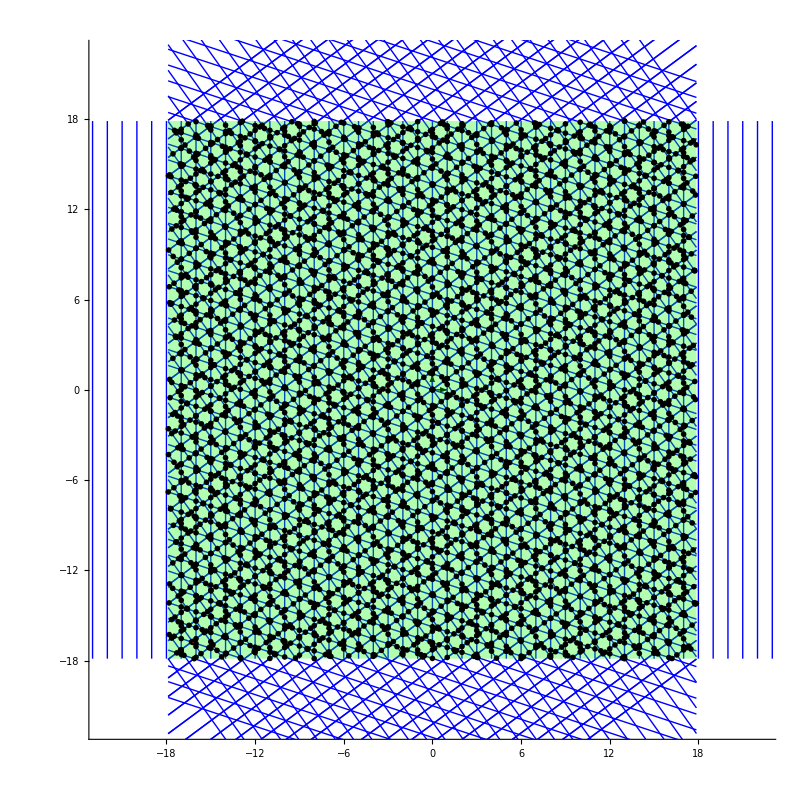

```mathematica
Show[xyBasis,
Table[Plot[-starvectors[[i,1]]/starvectors[[i,2]]*x+ShiftedSpacings[[i,j]]/starvectors[[i,2]],{x,-maxlength,maxlength},PlotStyle->{Blue,Thin}],{i,Range[2,5]},{j,Range[numlines+1]}],
Table[Graphics[{Blue,Thin,Line[{{x,-maxlength},{x,maxlength}}]}],{x,ShiftedSpacings[[1]]}],
Graphics[{Green,Opacity[0.3],Polygon[{{-maxlength,-maxlength},{-maxlength,maxlength},{maxlength,maxlength},{maxlength,-maxlength},{-maxlength,-maxlength}}]}],
Graphics[{PointSize[0.005],Point[UniqueGridVertices[[All,3,{1,2}]]]}](*option here gets rid of indeterminate values*),
Graphics[{PointSize[0.001],Red,Point[UniqueGridVertices[[186,3,{1,2}]]]}],
AspectRatio->1,PlotRange->{{-1.25maxlength,1.25maxlength},{-1.25maxlength,1.25maxlength}}
]
```

```mathematica
(*translate vertices and tiles so that COM is at origin*)
CalculateCOM[pts_]:=Module[
{x,y},
x=0;y=0;
Do[
x+=pt[[1]];y+=pt[[2]];,
{pt,pts}];
{x,y}/Length[pts]
]
com=CalculateCOM[Flatten[tiles[[All,2,1,1]],2]];
tiles2=tiles;
tiles2[[All,1]]=Table[x-com,{x,tiles2[[All,1,{1,2}]]}];
translate={com,com};
Do[
tiles2[[i,2,1,1]]=Table[x-translate,{x,tiles2[[i,2,1,1,All]]}];
,{i,Length[tiles2]}
]
```

```mathematica
allvertices=Module[
{list,n},
list={};
n=Length[tiles2];
Do[
list=Join[list,Flatten[tiles2[[i,2,1,1]],1]];
,{i,Range[n]}
];
list
];
```

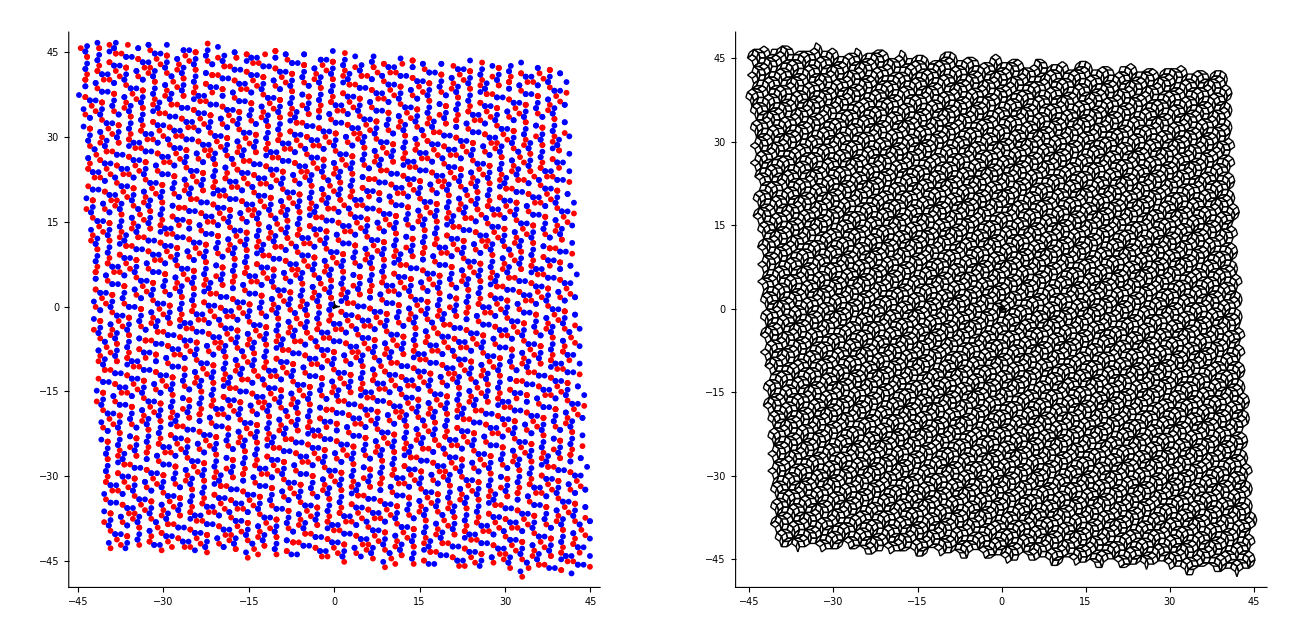

```mathematica
g=GraphicsRow[
{
Show[xyBasis,
(*tiles2[[All,2]],*)
(*Graphics[{PointSize[0.01],Blue,Point[allvertices]}],*)
Graphics[{
(*{PointSize[0.01],Red,Point[tiles2[[All,1]]]},*)
{PointSize[.007],Red,Point[tiles2[[Flatten[Position[tiles2[[All,3]],_?(Length[#]==2&)],2],1]]]},
{PointSize[.007],Blue,Point[tiles2[[Flatten[Position[tiles2[[All,3]],_?(Length[#]==3&)],2],1]]]},
{PointSize[.007],Green,Point[tiles2[[Flatten[Position[tiles2[[All,3]],_?(Length[#]==4&)],2],1]]]}
}],
AspectRatio->1,ImageSize->600
],
Show[xyBasis,
tiles2[[All,2]],
(*Graphics[{PointSize[0.008],Red,Point[tiles2[[All,1]]]}],
Graphics[{PointSize[Large],Blue,Point[tiles2[[Flatten[Position[tiles2[[All,3]],_?(Length[#]==3&)],2],1]]]}],*)
AspectRatio->1,ImageSize->600
]
}]
```

```mathematica
FOUTpts=StringJoin["2D_PA_","F2_F1_",ToString[F2],"_",ToString[F1],"__N",ToString[numlines+1],"_Len",ToString[Length[pts]],"_pts.txt"];
FOUTuniq=StringJoin["2D_PA_","F2_F1_",ToString[F2],"_",ToString[F1],"__N",ToString[numlines+1],"_Len",ToString[Length[UniqueGridVertices]],"_uniq.txt"];
FOUTtiles=StringJoin["2D_PA_","F2_F1_",ToString[F2],"_",ToString[F1],"__N",ToString[numlines+1],"_Len",ToString[Length[tiles2]],"_tiles.txt"];
FOUTtilesimg=StringJoin["2D_PA_","F2_F1_",ToString[F2],"_",ToString[F1],"__N",ToString[numlines+1],"_Len",ToString[Length[tiles2]],"_tiles.bmp"];
Export[FOUTpts,pts,"Table"]
Export[FOUTuniq,UniqueGridVertices,"Table"]
Export[FOUTtiles,tiles2,"Table"]
Export[FOUTtilesimg,g]
```

2D_PA_F2_F1_2_1__N51_Len11933_pts.txt

2D_PA_F2_F1_2_1__N51_Len6007_uniq.txt

2D_PA_F2_F1_2_1__N51_Len6006_tiles.txt

2D_PA_F2_F1_2_1__N51_Len6006_tiles.bmp